# The geographic distance on asteroids

## Introduction

Asteroids formed five billion years ago in the solar system. Having failed to integrate with planets, they are the largest space rocks orbiting the Sun. Their size ranges from a few meters to hundreds of kilometres across, and their weight is much less than the moon. As a result of their formation and impacts, they have irregular shapes. Their heterogeneous surfaces are also heavily cratered. What is the shortest path between two distinct points on the surface of the asteroid?

To find such a path, I start by uploading the asteroids’ data [1].

```mathematica
Atlas=Import["/Volumes/Space_E/ImperialCollege/PhD/WolframSummerSchool/Project/Atlas.obj","BoundaryMeshRegion"(*"GraphicsComplex"*)];
Lutetia=Import["/Volumes/Space_E/ImperialCollege/PhD/WolframSummerSchool/Project/21Lutetia.obj","BoundaryMeshRegion"(*"GraphicsComplex"*)];
Kleopatra=Import["/Volumes/Space_E/ImperialCollege/PhD/WolframSummerSchool/Project/216Kleopatra.obj"(*"GraphicsComplex"*)];

dataAtlas=Import["/Volumes/Space_E/ImperialCollege/PhD/WolframSummerSchool/Project/Atlas.obj","Table"];
dataLutetia=Import["/Volumes/Space_E/ImperialCollege/PhD/WolframSummerSchool/Project/21Lutetia.obj","Table"];
dataKleopatra=Import["/Volumes/Space_E/ImperialCollege/PhD/WolframSummerSchool/Project/216Kleopatra.obj","Table"];
```

```mathematica
{Graphics3D[Atlas,Boxed->False],Graphics3D[Lutetia,Boxed->False],Graphics3D[Kleopatra,Boxed->False]}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

The centre of these 3-dimensional objects is not usually at the origin of the Cartesian coordinate system. For example, the centre of the asteroid Lutetia is

```mathematica
{centreLutetia,centreAtlas,centreKleopatra}={RegionCentroid[Lutetia],RegionCentroid[Atlas],RegionCentroid[Kleopatra]}
```

{{1.61516,2.69139,0.94739},{-0.0687444,-0.0167443,-0.0472993},{0.545271,-0.0145182,-0.531176}}

It is convenient to express the Cartesian coordinates of the asteroid’s surface in Spherical coordinate. This function updates the coordinates so that the centre of the asteroid is at the origin of the Cartesian coordinate system. Then, it transforms the Cartesian coordinates into spherical coordinates.

```mathematica
findSphericalCoordinates[data_,centre_]:=Module[{vertices,r,θ,ϕ},
vertices=Map[#-centre &,Cases[data,{"v",x_,y_,z_}-> {x,y,z}]];
{r,θ,ϕ}=Transpose[ToSphericalCoordinates[vertices]];
Transpose[{θ,ϕ,r}]
]
```

```mathematica
coordSphLutetia=findSphericalCoordinates[dataLutetia,centreLutetia];
```

These spherical coordinates {r_i,θ_i,ϕ_i}_(i ∈ A), where A is the set containing all the spherical coordinates, are a discrete representation of the surface of the asteroid Lutetia.

To find the shortest path, I first calculate a smooth 2-dimensional curve for the surface of the asteroid. Then, I apply differential geometry to calculate the geodesic. This approach requires solving two second order partial differential equations.

## The surface of the asteroid

## Spherical harmonic approximation

In the spherical coordinate system, we have 0≤ θ≤π and -π<ϕ≤ π . Because the surface of the asteroid is irregular, the radius is a function of the polar angle and the azimuthal angle r=r(θ,ϕ). To calculate the radius r(θ,ϕ)of the asteroid, I use a linear superposition of spherical harmonics Y_l^m(θ,ϕ), where l≥0 is an integer and -l≤m≤l. This linear superposition will approximate the radius of the asteroid. As a result,  r(θ,ϕ)≃ ∑_(l=0)^l_Max ∑_(m=-l)^l a_(l m)Y_l^m(θ,ϕ), where l_Max is a given positive number defining the order of the approximation, and  a_(l m) is a constant coefficient for the linear superposition [2]. For any positive integer l_Max, the spherical harmonics are

```mathematica
findFormFit[lMax_]:=Assuming[{θ≥0,θ≤π,ϕ>-π,ϕ≤π},Flatten[Table[Table[If[m<0,(-1)^m √((2l+1)/(2π)((l-Abs[m])!)/((l+Abs[m])!))LegendreP[l,Abs[m],Cos[θ]]Sin[Abs[m] ϕ],If[m==0,√((2l+1)/(4π))LegendreP[l,m,Cos[θ]],(-1)^m √((2l+1)/(2π)((l-m)!)/((l+m)!))LegendreP[l,m,Cos[θ]]Cos[m ϕ]]],{m,-l,l}],{l,0,lMax}]]//Simplify]
```

.

```mathematica
With[{lMax=8},formFit=findFormFit[lMax]];
```

This list contains(l_Max+1)^2 spherical harmonics. The coefficients a_(l m) are found using the linear fit model.

## Plot of Lutetia’s surface

For the asteroid Lutetia, the coefficients a_(l m) are

```mathematica
rLinLutetia=LinearModelFit[coordSphLutetia,formFit,{θ,ϕ}]
```

FittedModel[48.2511+«115»+0.0687815 Cos[θ] Sin[θ]^7 Sin[7 ϕ]+0.314166 Sin[θ]^8 Sin[8 ϕ]]

. For l_Max=1,l_Max=3,l_Max=5, l_Max=8 and l_Max=15, the fitted radius are

```mathematica
Assuming[{θ≥0,θ≤π,ϕ>-π,ϕ≤π},rLinLutetia[θ,ϕ]//Chop//Simplify]
```

46.0153-55.5893 Cos[θ]^7+15.0221 Cos[θ]^8+1.5518 Cos[3 θ]+0.57852 Cos[4 θ]+0.387549 Cos[5 θ]+3.4834 Cos[ϕ] Sin[θ]+0.93258 Cos[3 θ] Cos[ϕ] Sin[θ]+2.3911 Cos[2 ϕ] Sin[θ]^2+1.10254 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2-1.42617 Cos[4 θ] Cos[2 ϕ] Sin[θ]^2-0.380005 Cos[5 θ] Cos[2 ϕ] Sin[θ]^2-0.884264 Cos[6 θ] Cos[2 ϕ] Sin[θ]^2+3.45513 Cos[3 ϕ] Sin[θ]^3+0.196605 Cos[3 θ] Cos[3 ϕ] Sin[θ]^3-4.09555 Cos[4 ϕ] Sin[θ]^4-4.35829 Cos[3 θ] Cos[4 ϕ] Sin[θ]^4+0.0736699 Cos[4 θ] Cos[4 ϕ] Sin[θ]^4+1.68933 Cos[5 ϕ] Sin[θ]^5-0.612983 Cos[3 θ] Cos[5 ϕ] Sin[θ]^5+0.832362 Cos[6 ϕ] Sin[θ]^6-0.0224802 Cos[7 ϕ] Sin[θ]^7+0.369867 Cos[8 ϕ] Sin[θ]^8+0.158702 Cos[4 θ] Cos[ϕ] Sin[2 θ]+0.396755 Cos[6 θ] Cos[ϕ] Sin[2 θ]+1.96343 Sin[θ] Sin[ϕ]-3.20155 Cos[3 θ] Sin[θ] Sin[ϕ]+9.41536 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+0.0038508 Cos[4 θ] Sin[2 θ] Sin[ϕ]+0.009627 Cos[6 θ] Sin[2 θ] Sin[ϕ]+0.00585025 Sin[4 θ] Sin[ϕ]+Cos[θ]^3 (-40.8173+32.4632 Cos[ϕ] Sin[θ]-33.1162 Cos[3 ϕ] Sin[θ]^3-30.1063 Sin[θ] Sin[ϕ])+Cos[θ]^6 (-42.5056-2.29415 Cos[ϕ] Sin[θ]-5.58993 Sin[θ] Sin[ϕ])-1.30494 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]-0.133337 Cos[4 θ] Sin[θ]^2 Sin[2 ϕ]-0.675337 Cos[5 θ] Sin[θ]^2 Sin[2 ϕ]-0.0296297 Cos[6 θ] Sin[θ]^2 Sin[2 ϕ]+3.25624 Sin[θ]^3 Sin[3 ϕ]+8.01032 Cos[3 θ] Sin[θ]^3 Sin[3 ϕ]+1.00792 Sin[2 θ]^3 Sin[3 ϕ]+Cos[θ]^4 (35.9018-7.79118 Cos[ϕ] Sin[θ]+6.94108 Cos[3 ϕ] Sin[θ]^3+14.6332 Sin[θ] Sin[ϕ]-15.6177 Sin[θ]^3 Sin[3 ϕ])+Cos[θ]^5 (89.7981-35.7096 Cos[ϕ] Sin[θ]+49.6742 Cos[3 ϕ] Sin[θ]^3+33.117 Sin[θ] Sin[ϕ]-12.095 Sin[θ]^3 Sin[3 ϕ])+Cos[θ]^2 (-9.51611+6.23692 Cos[ϕ] Sin[θ]-3.20358 Cos[3 ϕ] Sin[θ]^3-7.21461 Sin[θ] Sin[ϕ]+7.20815 Sin[θ]^3 Sin[3 ϕ])-1.8765 Sin[θ]^4 Sin[4 ϕ]-0.732017 Cos[3 θ] Sin[θ]^4 Sin[4 ϕ]+1.53251 Cos[4 θ] Sin[θ]^4 Sin[4 ϕ]-0.133949 Sin[θ]^5 Sin[5 ϕ]-3.06098 Cos[3 θ] Sin[θ]^5 Sin[5 ϕ]-0.628831 Sin[θ]^6 Sin[6 ϕ]+Cos[2 θ] (-8.00736+3.5375 Cos[2 ϕ] Sin[θ]^2+0.535125 Cos[3 ϕ] Sin[θ]^3-2.96094 Cos[4 ϕ] Sin[θ]^4+1.3039 Cos[5 ϕ] Sin[θ]^5+0.70769 Cos[6 ϕ] Sin[θ]^6+1.64304 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.70088+0.96442 Cos[θ]-1.97328 Sin[θ] Sin[ϕ])+3.46124 Sin[θ]^3 Sin[3 ϕ]-0.558268 Sin[θ]^4 Sin[4 ϕ]-1.55605 Sin[θ]^5 Sin[5 ϕ]-1.61471 Sin[θ]^6 Sin[6 ϕ])+0.306876 Sin[θ]^7 Sin[7 ϕ]+Cos[θ] (5.82504+3.58838 Cos[2 ϕ] Sin[θ]^2+0.47758 Cos[3 ϕ] Sin[θ]^3-11.2701 Cos[4 ϕ] Sin[θ]^4-1.4624 Cos[5 ϕ] Sin[θ]^5+1.92172 Cos[6 ϕ] Sin[θ]^6-1.71497 Cos[7 ϕ] Sin[θ]^7+0.157833 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (-2.32019-3.85196 Sin[θ] Sin[ϕ])+11.3364 Sin[θ]^3 Sin[3 ϕ]-2.26905 Sin[θ]^4 Sin[4 ϕ]-3.66664 Sin[θ]^5 Sin[5 ϕ]+0.5921 Sin[θ]^6 Sin[6 ϕ]+0.0687815 Sin[θ]^7 Sin[7 ϕ])+0.314166 Sin[θ]^8 Sin[8 ϕ]

l_Max=1

```mathematica
rFitLutetia[θ_,ϕ_]:=50.067111118223465+0.1551859396907776 Cos[θ]-0.1470732095804858 Cos[ϕ] Sin[θ]-0.24496950815814278 Sin[θ] Sin[ϕ]
```

l_Max=3

```mathematica
rFitLutetia[θ_,ϕ_]:=
```

l_Max=5

```mathematica
rFitLutetia[θ_,ϕ_]:=
```

l_Max=8

```mathematica
rFitLutetia[θ_,ϕ_]:=
```

l_Max=15

```mathematica
rFitLutetia[θ_,ϕ_]:=
```

. When l_Max=15, the surface of the asteroid is

```mathematica
plot3DFitLutetia=SphericalPlot3D[rFitLutetia[θ,ϕ],{θ,0,π},{ϕ,-π,π},MeshStyle->{{Black,Opacity[0.3]},{Black,Opacity[0.3]}},PlotStyle->{RGBColor[0.7333333333333333, 0.6, 0.4666666666666667],Opacity[0.6]}]
```

-Graphics3D-

.

## Percentage error

To calculate the error introduced by the linear expansion of the spherical harmonics, I calculate for each point (θ,ϕ) the percentage error between the fitted radius and the radius imported from the NASA’s data.

```mathematica
dataErrorL3=Map[100 Abs[(rFitLutetia[#[[1]],#[[2]]]-#[[3]])/(#[[3]])]&,coordSphLutetia];
plotErrL3=ListPlot[Transpose[{Range[dataErrorL3//Length],dataErrorL3}],];
```

```mathematica
dataErrorL8=Map[100 Abs[(rFitLutetia[#[[1]],#[[2]]]-#[[3]])/(#[[3]])]&,coordSphLutetia];
plotErrL8=ListPlot[Transpose[{Range[dataErrorL8//Length],dataErrorL8}],];
```

```mathematica
dataErrorL15=Map[100 Abs[(rFitLutetia[#[[1]],#[[2]]]-#[[3]])/(#[[3]])]&,coordSphLutetia];
plotErrL15=ListPlot[Transpose[{Range[dataErrorL15//Length],dataErrorL15}],];
```

The plot shows the percentage error for three different linear approximations, namely l_Max=3, l_Max=8 and l_Max=15 .

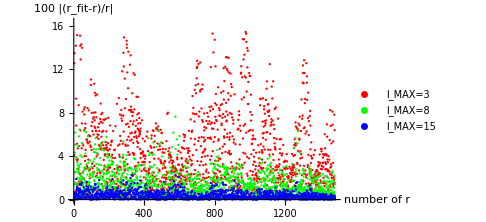

```mathematica
plotErrorsLutetia=Show[{plotErrL3,plotErrL8,plotErrL15}]
```

```mathematica
(*Export["/Volumes/Space_E/ImperialCollege/PhD/WolframSummerSchool/Project/FitLutetia.eps",plotFitLutetia]*)
```

/Volumes/Space_E/ImperialCollege/PhD/WolframSummerSchool/Project/FitLutetia.eps

```mathematica
(*Export["/Volumes/Space_E/ImperialCollege/PhD/WolframSummerSchool/Project/ErrorFitLutetia.eps",plotErrorsLutetia]*)
```

/Volumes/Space_E/ImperialCollege/PhD/WolframSummerSchool/Project/ErrorFitLutetia.eps

## The geodesic

## Metric tensor

To calculate the geodesic, I will solve the differential equation of the geodesic [3]. The geodesic is a line on the surface of the asteroid. This surface is a 2-dimensional curved space embedded in a 3-dimensional space. As a result, the base vectors of the surface change for different locations on the surface. The metric is the second rank tensor which depends on base vectors. It is g_αβ=(r^2+((∂r)/(∂θ))^2 | (∂r)/(∂θ)(∂r)/(∂ϕ)
(∂r)/(∂θ)(∂r)/(∂ϕ) | r^2 Sin(θ)^2+((∂r)/(∂ϕ))^2), where the Greek indices  α,β∈{θ,ϕ}. 

The operational form of the metric tensor is

```mathematica
Og[θ_,ϕ_]={{#^2+D[#,θ]^2,D[#,θ]D[#,ϕ]},{D[#,θ]D[#,ϕ],#^2 Sin[θ]^2+D[#,ϕ]^2}}&
```

{{#1^2+(∂_θ #1)^2,∂_θ #1 ∂_ϕ #1},{∂_θ #1 ∂_ϕ #1,#1^2 Sin[θ]^2+(∂_ϕ #1)^2}}&

. This operator acts on any radial function r(θ,ϕ). The inverse of the matric tensor is g^αβ. Its functional form is

```mathematica
OgInv[θ_,ϕ_]=1/(#^2 Sin[θ]^2+Sin[θ]^2 D[#,θ]^2+D[#,ϕ]^2){{Sin[θ]^2+D[#,ϕ]^2/#^2,-(D[#,θ] D[#,ϕ])/#^2},{-(D[#,θ] D[#,ϕ])/#^2,1+D[#,θ]^2/#^2}}&
```

{{Sin[θ]^2+(∂_ϕ #1)^2/#1^2,-(∂_θ #1 ∂_ϕ #1)/#1^2},{-(∂_θ #1 ∂_ϕ #1)/#1^2,1+(∂_θ #1)^2/#1^2}}/(#1^2 Sin[θ]^2+Sin[θ]^2 (∂_θ #1)^2+(∂_ϕ #1)^2)&

For l_Max=5 the metric tensor and the inverse metric tensor are respectively

```mathematica
Assuming[{θ≥0,θ≤π,ϕ>-π,ϕ≤π},Og[θ,ϕ][rFitLutetia[θ,ϕ]]//Chop//Simplify]
```

{{(45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+(-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))^2,Sin[θ] (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))},{Sin[θ] (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ]))),Sin[θ]^2 ((1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])^2+(45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2)}}

```mathematica
gFit[θ_,ϕ_]:=
```

```mathematica
Assuming[{θ≥0,θ≤π,ϕ>-π,ϕ≤π},OgInv[θ,ϕ][rFitLutetia[θ,ϕ]]//Chop//Simplify]
```

{{(1+(1. ((19.4461+1. Cos[θ]-2.39921 Cos[2 θ]) Cos[ϕ]^2 Sin[θ]+20.9864 Cos[3 ϕ] Sin[θ]^2-22.5649 Cos[θ] Cos[3 ϕ] Sin[θ]^2+20.4276 Cos[2 θ] Cos[3 ϕ] Sin[θ]^2-5.57261 Cos[4 ϕ] Sin[θ]^3-5.12583 Cos[θ] Cos[4 ϕ] Sin[θ]^3+11.4943 Cos[5 ϕ] Sin[θ]^4+Cos[3 θ] (0.652898 Cos[2 ϕ] Sin[θ]-2.79463 Sin[ϕ])-6.73361 Sin[ϕ]-7.02145 Cos[θ] Sin[ϕ]-12.9069 Cos[θ]^2 Sin[ϕ]+19.3604 Cos[θ]^4 Sin[ϕ]-11.0654 Cos[2 θ] Sin[ϕ]-19.4461 Sin[θ] Sin[ϕ]^2-1. Cos[θ] Sin[θ] Sin[ϕ]^2+2.39921 Cos[2 θ] Sin[θ] Sin[ϕ]^2+Cos[ϕ] (3.87098-10.8002 Cos[θ]^2+16.2003 Cos[θ]^4+3.26168 Cos[2 θ]-6.50301 Cos[3 θ]-24.1337 Sin[θ] Sin[ϕ]-15.0141 Cos[3 θ] Sin[θ] Sin[ϕ]+Cos[θ] (-9.55589-34.8687 Sin[θ] Sin[ϕ]))-19.9048 Cos[2 θ] Sin[θ] Sin[2 ϕ]-18.7758 Sin[θ]^2 Sin[3 ϕ]+20.1351 Cos[θ] Sin[θ]^2 Sin[3 ϕ]-2.199 Cos[2 θ] Sin[θ]^2 Sin[3 ϕ]+11.3131 Sin[θ]^3 Sin[4 ϕ]+14.5096 Cos[θ] Sin[θ]^3 Sin[4 ϕ]-5.81006 Sin[θ]^4 Sin[5 ϕ])^2)/(89.6633+3.12438 Cos[3 θ]+1.18038 Cos[4 θ]+1.00025 Cos[5 θ]+6.73361 Cos[ϕ] Sin[θ]+2.79463 Cos[3 θ] Cos[ϕ] Sin[θ]+6.03342 Cos[2 ϕ] Sin[θ]^2+3.75353 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+6.2586 Cos[3 ϕ] Sin[θ]^3-2.82828 Cos[4 ϕ] Sin[θ]^4+1.16201 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (12.9069 Cos[ϕ]-10.8002 Sin[ϕ])+3.87098 Sin[θ] Sin[ϕ]-6.50301 Cos[3 θ] Sin[θ] Sin[ϕ]+19.4461 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-19.3604 Cos[ϕ]+16.2003 Sin[ϕ])+0.326449 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+6.99548 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-15.7123+9.9524 Cos[2 ϕ] Sin[θ]^2+0.732999 Cos[3 ϕ] Sin[θ]^3+3.26168 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (11.0654-2.39921 Sin[θ] Sin[ϕ])+6.8092 Sin[θ]^3 Sin[3 ϕ])-1.39315 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (2.74563+8.71719 Cos[2 ϕ] Sin[θ]^2-6.71171 Cos[3 ϕ] Sin[θ]^3-3.62739 Cos[4 ϕ] Sin[θ]^4-9.55589 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (7.02145+1. Sin[θ] Sin[ϕ])-7.52165 Sin[θ]^3 Sin[3 ϕ]-1.28146 Sin[θ]^4 Sin[4 ϕ])+2.29885 Sin[θ]^5 Sin[5 ϕ])^2)/((1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])^2+(45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+(-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))^2),-((Csc[θ] (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ]))))/((45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2 ((1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])^2+(45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+(-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))^2)))},{-((Csc[θ] (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ]))))/((45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2 ((1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])^2+(45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+(-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))^2))),(Csc[θ]^2 (1+(1. (0.484141 Sin[3 θ]+0.243875 Sin[4 θ]+0.258325 Sin[5 θ]+Cos[θ]^5 (1. Cos[ϕ]-0.836774 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (-0.666667-4. Sin[θ]^2)+(0.557849+3.3471 Sin[θ]^2) Sin[ϕ])+0.030981 Sin[4 θ] Sin[2 ϕ]+Sin[θ]^2 (0.362671 Cos[ϕ]+0.581631 Cos[2 ϕ] Sin[3 θ]-0.49358 Sin[ϕ]+0.0505851 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (-0.346673 Cos[3 ϕ]-0.388507 Sin[3 ϕ])+0.29138 Sin[2 θ]^2 Sin[3 ϕ]+Sin[θ]^3 (0.450259 Cos[2 ϕ]+0.0757216 Cos[3 ϕ] Sin[2 θ]+0.0516519 Cos[ϕ] Sin[ϕ]+0.703416 Sin[2 θ] Sin[3 ϕ])+Sin[θ] (0.141817+0.433044 Cos[ϕ] Sin[3 θ]-1.00768 Sin[3 θ] Sin[ϕ]-0.263781 Sin[4 θ] Sin[3 ϕ])+Sin[θ]^5 (-0.187361 Cos[4 ϕ]-0.0661897 Sin[4 ϕ])+Cos[θ]^2 (-0.900518 Cos[2 ϕ] Sin[θ]+1.04002 Cos[3 ϕ] Sin[θ]^2+0.749446 Cos[4 ϕ] Sin[θ]^3+0.49358 Sin[ϕ]+Cos[ϕ] (-0.362671-0.103304 Sin[θ] Sin[ϕ])+0.264759 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((-0.199944-0.168472 Cos[2 θ]+0.335893 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (-0.347804-0.57155 Cos[2 θ]-0.144348 Cos[3 θ]+3.61953 Sin[θ]^2-2.00885 Sin[θ] Sin[ϕ]-0.495696 Sin[θ]^3 Sin[ϕ])+Sin[θ] (-3.24628+(-0.623275-1.02812 Cos[2 θ]-0.387754 Cos[3 θ]) Cos[2 ϕ]-0.0337234 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((-0.969805-0.113582 Cos[2 θ]) Cos[3 ϕ]-0.441812 Sin[ϕ]-1.08399 Sin[3 ϕ])+Sin[θ]^3 (2.05624 Cos[2 ϕ]+0.584345 Cos[4 ϕ]+0.287836 Sin[4 ϕ])+Sin[θ]^4 (-0.300101 Cos[5 ϕ]-0.5937 Sin[5 ϕ])))^2)/(-4.63128-0.16138 Cos[3 θ]-0.0609688 Cos[4 θ]-0.051665 Cos[5 θ]-0.347804 Cos[ϕ] Sin[θ]-0.144348 Cos[3 θ] Cos[ϕ] Sin[θ]-0.311638 Cos[2 ϕ] Sin[θ]^2-0.193877 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2-0.323268 Cos[3 ϕ] Sin[θ]^3+0.146086 Cos[4 ϕ] Sin[θ]^4-0.0600201 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^4 Sin[θ] (1. Cos[ϕ]-0.836774 Sin[ϕ])+Cos[θ]^2 Sin[θ] (-0.666667 Cos[ϕ]+0.557849 Sin[ϕ])-0.199944 Sin[θ] Sin[ϕ]+0.335893 Cos[3 θ] Sin[θ] Sin[ϕ]-1.00443 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-0.0168617 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]-0.36133 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (0.811569-0.51406 Cos[2 ϕ] Sin[θ]^2-0.0378608 Cos[3 ϕ] Sin[θ]^3-0.168472 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (-0.57155+0.123924 Sin[θ] Sin[ϕ])-0.351708 Sin[θ]^3 Sin[3 ϕ])+0.0719589 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (-0.141817-0.450259 Cos[2 ϕ] Sin[θ]^2+0.346673 Cos[3 ϕ] Sin[θ]^3+0.187361 Cos[4 ϕ] Sin[θ]^4+0.49358 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (-0.362671-0.0516519 Sin[θ] Sin[ϕ])+0.388507 Sin[θ]^3 Sin[3 ϕ]+0.0661897 Sin[θ]^4 Sin[4 ϕ])-0.11874 Sin[θ]^5 Sin[5 ϕ])^2))/((1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])^2+(45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+(-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))^2)}}

```mathematica
gInvFit[θ_,ϕ_]:=
```

It is convenient to calculate the partial derivatives of the metric tensor. The partial derivative (∂g_αβ)/(∂θ), which is usually written using the compact notation g_(αβ,θ) , is

```mathematica
Assuming[{θ≥0,θ≤π,ϕ>-π,ϕ≤π},D[gFit[θ,ϕ],θ]//Chop//Simplify]
```

{{2 (45.7325-12.7487 Cos[3 θ]-9.03074 Cos[4 θ]-12.2443 Cos[5 θ]-12.8286 Cos[3 θ] Cos[ϕ] Sin[θ]-32.0561 Sin[θ]^2-3.07733 Cos[2 ϕ] Sin[θ]^2-19.1448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+35.7419 Cos[ϕ] Sin[θ]^3-6.38437 Cos[3 ϕ] Sin[θ]^3+20.3048 Cos[2 ϕ] Sin[θ]^4+4.32768 Cos[4 ϕ] Sin[θ]^4-2.37073 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^4 Sin[θ] (118.497 Cos[ϕ]-99.1549 Sin[ϕ])-2.22045×10^-16 Sin[θ] Sin[ϕ]+29.8516 Cos[3 θ] Sin[θ] Sin[ϕ]-9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.6631 Cos[3 θ] Cos[ϕ] Sin[θ]^2 Sin[ϕ]-4.36277 Sin[θ]^3 Sin[ϕ]-4.89485 Cos[ϕ] Sin[θ]^4 Sin[ϕ]+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.05928 Sin[2 θ]^2 Sin[2 ϕ]-7.13605 Sin[θ]^3 Sin[3 ϕ]-20.8381 Sin[θ] Sin[2 θ]^2 Sin[3 ϕ]+Cos[2 θ] (-8.01402-5.0762 Cos[2 ϕ] Sin[θ]^2-2.24319 Cos[3 ϕ] Sin[θ]^3+2.22045×10^-16 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (-8.88178×10^-16+1.22371 Sin[θ] Sin[ϕ])-20.8381 Sin[θ]^3 Sin[3 ϕ])+2.13172 Sin[θ]^4 Sin[4 ϕ]-2.13172 Sin[2 θ]^2 Sin[4 ϕ]+Cos[θ]^3 (8.89236 Cos[2 ϕ]-20.5398 Cos[3 ϕ] Sin[θ]-22.2017 Cos[4 ϕ] Sin[θ]^2+1.0201 Cos[ϕ] Sin[ϕ]-23.0184 Sin[θ] Sin[3 ϕ]-7.84325 Sin[θ]^2 Sin[4 ϕ])+Cos[θ] (30.8096 Cos[3 ϕ] Sin[θ]^3+22.2017 Cos[4 ϕ] Sin[θ]^4-4.48637 Cos[3 ϕ] Sin[θ]^2 Sin[2 θ]+Cos[2 ϕ] Sin[θ] (-26.6771 Sin[θ]-22.9738 Sin[3 θ])+14.6219 Sin[θ] Sin[ϕ]+19.9011 Sin[3 θ] Sin[ϕ]+Cos[ϕ] (-10.7438 Sin[θ]-8.55238 Sin[3 θ]-3.06029 Sin[θ]^2 Sin[ϕ])-1.99806 Sin[θ] Sin[3 θ] Sin[2 ϕ]+34.5276 Sin[θ]^3 Sin[3 ϕ]+7.84325 Sin[θ]^4 Sin[4 ϕ])-4.6901 Sin[θ]^5 Sin[5 ϕ]+Cos[θ]^2 (32.0561+19.1531 Cos[3 ϕ] Sin[θ]+2.24319 Cos[2 θ] Cos[3 ϕ] Sin[θ]-17.3107 Cos[4 ϕ] Sin[θ]^2+11.8536 Cos[5 ϕ] Sin[θ]^3+Cos[2 ϕ] (6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]-101.524 Sin[θ]^2)+13.0883 Sin[θ] Sin[ϕ]+99.1549 Sin[θ]^3 Sin[ϕ]+Cos[ϕ] (-107.226 Sin[θ]-118.497 Sin[θ]^3+(19.8369-2.44743 Cos[2 θ]) Sin[ϕ])+0.333009 Cos[3 θ] Sin[2 ϕ]+21.4082 Sin[θ] Sin[3 ϕ]+20.8381 Cos[2 θ] Sin[θ] Sin[3 ϕ]+23.4505 Sin[θ]^3 Sin[5 ϕ])) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ]))),Sin[θ] (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) (-9.63279 Cos[4 θ]-12.7544 Cos[5 θ]-3.43446 Cos[ϕ] Sin[θ]-5.64389 Cos[2 θ] Cos[ϕ] Sin[θ]-32.0561 Sin[θ]^2-6.15466 Cos[2 ϕ] Sin[θ]^2-10.1524 Cos[2 θ] Cos[2 ϕ] Sin[θ]^2+35.7419 Cos[ϕ] Sin[θ]^3-9.57655 Cos[3 ϕ] Sin[θ]^3-2.61705 Cos[2 θ] Cos[3 ϕ] Sin[θ]^3+20.3048 Cos[2 ϕ] Sin[θ]^4+5.77024 Cos[4 ϕ] Sin[θ]^4-2.96341 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^4 Sin[θ] (128.371 Cos[ϕ]-107.418 Sin[ϕ])-1.97439 Sin[θ] Sin[ϕ]-1.66361 Cos[2 θ] Sin[θ] Sin[ϕ]-19.8369 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+2.44743 Cos[2 θ] Cos[ϕ] Sin[θ]^2 Sin[ϕ]-4.36277 Sin[θ]^3 Sin[ϕ]-4.89485 Cos[ϕ] Sin[θ]^4 Sin[ϕ]+Cos[3 θ] (-14.3423-21.0593 Cos[2 ϕ] Sin[θ]^2+33.1685 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (-14.254-3.6631 Sin[θ] Sin[ϕ]))+3.05928 Sin[2 θ]^2 Sin[2 ϕ]-10.7041 Sin[θ]^3 Sin[3 ϕ]-24.3111 Cos[2 θ] Sin[θ]^3 Sin[3 ϕ]-20.8381 Sin[θ] Sin[2 θ]^2 Sin[3 ϕ]+2.84229 Sin[θ]^4 Sin[4 ϕ]-2.13172 Sin[2 θ]^2 Sin[4 ϕ]+Cos[θ]^3 (8.89236 Cos[2 ϕ]-20.5398 Cos[3 ϕ] Sin[θ]-22.2017 Cos[4 ϕ] Sin[θ]^2+1.0201 Cos[ϕ] Sin[ϕ]-23.0184 Sin[θ] Sin[3 ϕ]-7.84325 Sin[θ]^2 Sin[4 ϕ])+Cos[θ] (-1.4004+34.2329 Cos[3 ϕ] Sin[θ]^3+24.0518 Cos[4 ϕ] Sin[θ]^4-4.48637 Cos[3 ϕ] Sin[θ]^2 Sin[2 θ]+Cos[2 ϕ] Sin[θ] ((-31.1233-40.6096 Cos[θ]) Sin[θ]-22.9738 Sin[3 θ])+19.4958 Sin[θ] Sin[ϕ]+19.9011 Sin[3 θ] Sin[ϕ]+Cos[ϕ] (-14.3251 Sin[θ]-8.55238 Sin[3 θ]-3.57033 Sin[θ]^2 Sin[ϕ])-1.99806 Sin[θ] Sin[3 θ] Sin[2 ϕ]+38.364 Sin[θ]^3 Sin[3 ϕ]+8.49686 Sin[θ]^4 Sin[4 ϕ])-5.86262 Sin[θ]^5 Sin[5 ϕ]+Cos[θ]^2 (32.0561+19.1531 Cos[3 ϕ] Sin[θ]+2.24319 Cos[2 θ] Cos[3 ϕ] Sin[θ]-17.3107 Cos[4 ϕ] Sin[θ]^2+11.8536 Cos[5 ϕ] Sin[θ]^3+Cos[2 ϕ] (6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]-60.9144 Sin[θ]^2)+18.5969 Sin[θ] Sin[ϕ]+99.1549 Sin[θ]^3 Sin[ϕ]+Cos[ϕ] (-113.809 Sin[θ]-118.497 Sin[θ]^3+(19.8369-2.44743 Cos[2 θ]) Sin[ϕ])+0.333009 Cos[3 θ] Sin[2 ϕ]+21.4082 Sin[θ] Sin[3 ϕ]+20.8381 Cos[2 θ] Sin[θ] Sin[3 ϕ]+23.4505 Sin[θ]^3 Sin[5 ϕ]))+Cos[θ] (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))+Sin[θ] (-0.510048 Cos[ϕ]^2 Sin[θ]^2+11.5092 Cos[3 ϕ] Sin[θ]^3+2.61442 Cos[4 ϕ] Sin[θ]^4-20.8381 Cos[3 ϕ] Sin[θ]^2 Sin[2 θ]-0.999028 Cos[2 ϕ] Sin[θ] Sin[3 θ]+Cos[θ]^3 Sin[θ] (-33.0516 Cos[ϕ]-39.4989 Sin[ϕ])+3.58127 Sin[θ] Sin[ϕ]+4.27619 Sin[3 θ] Sin[ϕ]+0.510048 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (4.87396 Sin[θ]+9.95054 Sin[3 θ]+17.7847 Sin[θ]^2 Sin[ϕ])+11.4869 Sin[θ] Sin[3 θ] Sin[2 ϕ]-10.2699 Sin[θ]^3 Sin[3 ϕ]+2.24319 Sin[θ]^2 Sin[2 θ] Sin[3 ϕ]-7.40056 Sin[θ]^4 Sin[4 ϕ]+Cos[θ]^2 (0.510048 Cos[ϕ]^2-23.0184 Cos[3 ϕ] Sin[θ]-7.84325 Cos[4 ϕ] Sin[θ]^2-17.7847 Cos[ϕ] Sin[ϕ]-0.510048 Sin[ϕ]^2+20.5398 Sin[θ] Sin[3 ϕ]+22.2017 Sin[θ]^2 Sin[4 ϕ])+Cos[θ] (0.333009 Cos[3 θ] Cos[2 ϕ]+21.4082 Cos[3 ϕ] Sin[θ]+20.8381 Cos[2 θ] Cos[3 ϕ] Sin[θ]-8.52688 Cos[4 ϕ] Sin[θ]^2+23.4505 Cos[5 ϕ] Sin[θ]^3+Cos[ϕ]^2 (9.91843-1.22371 Cos[2 θ]+4.89485 Sin[θ]^2)+35.7419 Sin[θ] Sin[ϕ]-9.91843 Sin[ϕ]^2+1.22371 Cos[2 θ] Sin[ϕ]^2-4.89485 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (4.36277 Sin[θ]+(-12.3093-20.3048 Cos[2 θ]-7.65793 Cos[3 θ]) Sin[ϕ]+81.2192 Sin[θ]^2 Sin[ϕ])-19.1531 Sin[θ] Sin[3 ϕ]-2.24319 Cos[2 θ] Sin[θ] Sin[3 ϕ]+17.3107 Sin[θ]^2 Sin[4 ϕ]-11.8536 Sin[θ]^3 Sin[5 ϕ])) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))},{Sin[θ] (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) (-9.63279 Cos[4 θ]-12.7544 Cos[5 θ]-3.43446 Cos[ϕ] Sin[θ]-5.64389 Cos[2 θ] Cos[ϕ] Sin[θ]-32.0561 Sin[θ]^2-6.15466 Cos[2 ϕ] Sin[θ]^2-10.1524 Cos[2 θ] Cos[2 ϕ] Sin[θ]^2+35.7419 Cos[ϕ] Sin[θ]^3-9.57655 Cos[3 ϕ] Sin[θ]^3-2.61705 Cos[2 θ] Cos[3 ϕ] Sin[θ]^3+20.3048 Cos[2 ϕ] Sin[θ]^4+5.77024 Cos[4 ϕ] Sin[θ]^4-2.96341 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^4 Sin[θ] (128.371 Cos[ϕ]-107.418 Sin[ϕ])-1.97439 Sin[θ] Sin[ϕ]-1.66361 Cos[2 θ] Sin[θ] Sin[ϕ]-19.8369 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+2.44743 Cos[2 θ] Cos[ϕ] Sin[θ]^2 Sin[ϕ]-4.36277 Sin[θ]^3 Sin[ϕ]-4.89485 Cos[ϕ] Sin[θ]^4 Sin[ϕ]+Cos[3 θ] (-14.3423-21.0593 Cos[2 ϕ] Sin[θ]^2+33.1685 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (-14.254-3.6631 Sin[θ] Sin[ϕ]))+3.05928 Sin[2 θ]^2 Sin[2 ϕ]-10.7041 Sin[θ]^3 Sin[3 ϕ]-24.3111 Cos[2 θ] Sin[θ]^3 Sin[3 ϕ]-20.8381 Sin[θ] Sin[2 θ]^2 Sin[3 ϕ]+2.84229 Sin[θ]^4 Sin[4 ϕ]-2.13172 Sin[2 θ]^2 Sin[4 ϕ]+Cos[θ]^3 (8.89236 Cos[2 ϕ]-20.5398 Cos[3 ϕ] Sin[θ]-22.2017 Cos[4 ϕ] Sin[θ]^2+1.0201 Cos[ϕ] Sin[ϕ]-23.0184 Sin[θ] Sin[3 ϕ]-7.84325 Sin[θ]^2 Sin[4 ϕ])+Cos[θ] (-1.4004+34.2329 Cos[3 ϕ] Sin[θ]^3+24.0518 Cos[4 ϕ] Sin[θ]^4-4.48637 Cos[3 ϕ] Sin[θ]^2 Sin[2 θ]+Cos[2 ϕ] Sin[θ] ((-31.1233-40.6096 Cos[θ]) Sin[θ]-22.9738 Sin[3 θ])+19.4958 Sin[θ] Sin[ϕ]+19.9011 Sin[3 θ] Sin[ϕ]+Cos[ϕ] (-14.3251 Sin[θ]-8.55238 Sin[3 θ]-3.57033 Sin[θ]^2 Sin[ϕ])-1.99806 Sin[θ] Sin[3 θ] Sin[2 ϕ]+38.364 Sin[θ]^3 Sin[3 ϕ]+8.49686 Sin[θ]^4 Sin[4 ϕ])-5.86262 Sin[θ]^5 Sin[5 ϕ]+Cos[θ]^2 (32.0561+19.1531 Cos[3 ϕ] Sin[θ]+2.24319 Cos[2 θ] Cos[3 ϕ] Sin[θ]-17.3107 Cos[4 ϕ] Sin[θ]^2+11.8536 Cos[5 ϕ] Sin[θ]^3+Cos[2 ϕ] (6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]-60.9144 Sin[θ]^2)+18.5969 Sin[θ] Sin[ϕ]+99.1549 Sin[θ]^3 Sin[ϕ]+Cos[ϕ] (-113.809 Sin[θ]-118.497 Sin[θ]^3+(19.8369-2.44743 Cos[2 θ]) Sin[ϕ])+0.333009 Cos[3 θ] Sin[2 ϕ]+21.4082 Sin[θ] Sin[3 ϕ]+20.8381 Cos[2 θ] Sin[θ] Sin[3 ϕ]+23.4505 Sin[θ]^3 Sin[5 ϕ]))+Cos[θ] (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))+Sin[θ] (-0.510048 Cos[ϕ]^2 Sin[θ]^2+11.5092 Cos[3 ϕ] Sin[θ]^3+2.61442 Cos[4 ϕ] Sin[θ]^4-20.8381 Cos[3 ϕ] Sin[θ]^2 Sin[2 θ]-0.999028 Cos[2 ϕ] Sin[θ] Sin[3 θ]+Cos[θ]^3 Sin[θ] (-33.0516 Cos[ϕ]-39.4989 Sin[ϕ])+3.58127 Sin[θ] Sin[ϕ]+4.27619 Sin[3 θ] Sin[ϕ]+0.510048 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (4.87396 Sin[θ]+9.95054 Sin[3 θ]+17.7847 Sin[θ]^2 Sin[ϕ])+11.4869 Sin[θ] Sin[3 θ] Sin[2 ϕ]-10.2699 Sin[θ]^3 Sin[3 ϕ]+2.24319 Sin[θ]^2 Sin[2 θ] Sin[3 ϕ]-7.40056 Sin[θ]^4 Sin[4 ϕ]+Cos[θ]^2 (0.510048 Cos[ϕ]^2-23.0184 Cos[3 ϕ] Sin[θ]-7.84325 Cos[4 ϕ] Sin[θ]^2-17.7847 Cos[ϕ] Sin[ϕ]-0.510048 Sin[ϕ]^2+20.5398 Sin[θ] Sin[3 ϕ]+22.2017 Sin[θ]^2 Sin[4 ϕ])+Cos[θ] (0.333009 Cos[3 θ] Cos[2 ϕ]+21.4082 Cos[3 ϕ] Sin[θ]+20.8381 Cos[2 θ] Cos[3 ϕ] Sin[θ]-8.52688 Cos[4 ϕ] Sin[θ]^2+23.4505 Cos[5 ϕ] Sin[θ]^3+Cos[ϕ]^2 (9.91843-1.22371 Cos[2 θ]+4.89485 Sin[θ]^2)+35.7419 Sin[θ] Sin[ϕ]-9.91843 Sin[ϕ]^2+1.22371 Cos[2 θ] Sin[ϕ]^2-4.89485 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (4.36277 Sin[θ]+(-12.3093-20.3048 Cos[2 θ]-7.65793 Cos[3 θ]) Sin[ϕ]+81.2192 Sin[θ]^2 Sin[ϕ])-19.1531 Sin[θ] Sin[3 ϕ]-2.24319 Cos[2 θ] Sin[θ] Sin[3 ϕ]+17.3107 Sin[θ]^2 Sin[4 ϕ]-11.8536 Sin[θ]^3 Sin[5 ϕ])) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ]))),Sin[θ] (2 Cos[θ] ((1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])^2+(45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2)+Sin[θ] (2 (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) (-0.510048 Cos[ϕ]^2 Sin[θ]^2+11.5092 Cos[3 ϕ] Sin[θ]^3+2.61442 Cos[4 ϕ] Sin[θ]^4-20.8381 Cos[3 ϕ] Sin[θ]^2 Sin[2 θ]-0.999028 Cos[2 ϕ] Sin[θ] Sin[3 θ]+Cos[θ]^3 Sin[θ] (-33.0516 Cos[ϕ]-39.4989 Sin[ϕ])+3.58127 Sin[θ] Sin[ϕ]+4.27619 Sin[3 θ] Sin[ϕ]+0.510048 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (4.87396 Sin[θ]+9.95054 Sin[3 θ]+17.7847 Sin[θ]^2 Sin[ϕ])+11.4869 Sin[θ] Sin[3 θ] Sin[2 ϕ]-10.2699 Sin[θ]^3 Sin[3 ϕ]+2.24319 Sin[θ]^2 Sin[2 θ] Sin[3 ϕ]-7.40056 Sin[θ]^4 Sin[4 ϕ]+Cos[θ]^2 (0.510048 Cos[ϕ]^2-23.0184 Cos[3 ϕ] Sin[θ]-7.84325 Cos[4 ϕ] Sin[θ]^2-17.7847 Cos[ϕ] Sin[ϕ]-0.510048 Sin[ϕ]^2+20.5398 Sin[θ] Sin[3 ϕ]+22.2017 Sin[θ]^2 Sin[4 ϕ])+Cos[θ] (0.333009 Cos[3 θ] Cos[2 ϕ]+21.4082 Cos[3 ϕ] Sin[θ]+20.8381 Cos[2 θ] Cos[3 ϕ] Sin[θ]-8.52688 Cos[4 ϕ] Sin[θ]^2+23.4505 Cos[5 ϕ] Sin[θ]^3+Cos[ϕ]^2 (9.91843-1.22371 Cos[2 θ]+4.89485 Sin[θ]^2)+35.7419 Sin[θ] Sin[ϕ]-9.91843 Sin[ϕ]^2+1.22371 Cos[2 θ] Sin[ϕ]^2-4.89485 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (4.36277 Sin[θ]+(-12.3093-20.3048 Cos[2 θ]-7.65793 Cos[3 θ]) Sin[ϕ]+81.2192 Sin[θ]^2 Sin[ϕ])-19.1531 Sin[θ] Sin[3 ϕ]-2.24319 Cos[2 θ] Sin[θ] Sin[3 ϕ]+17.3107 Sin[θ]^2 Sin[4 ϕ]-11.8536 Sin[θ]^3 Sin[5 ϕ]))+2 (45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ]) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))))}}

```mathematica
dgFitθ[θ_,ϕ_]:=
```

Finally, the partial derivative (∂g_αβ)/(∂ϕ), which is usually written using the compact notation g_(αβ,ϕ) , is

```mathematica
Assuming[{θ≥0,θ≤π,ϕ>-π,ϕ≤π},D[gFit[θ,ϕ],ϕ]//Simplify]
```

{{2 Sin[θ] (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) (45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])+2 (Sin[θ] Sin[3 θ] (9.95054 Cos[ϕ]+4.27619 Sin[ϕ])+Cos[θ]^5 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (-5.5086-33.0516 Sin[θ]^2)+(-6.58314-39.4989 Sin[θ]^2) Sin[ϕ])+Sin[θ]^2 (4.87396 Cos[ϕ]-0.999028 Cos[2 ϕ] Sin[3 θ]+3.58127 Sin[ϕ]+11.4869 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (11.5092 Cos[3 ϕ]-10.2699 Sin[3 ϕ])+Sin[θ]^3 (-0.510048 Cos[ϕ]^2-20.8381 Cos[3 ϕ] Sin[2 θ]+17.7847 Cos[ϕ] Sin[ϕ]+0.510048 Sin[ϕ]^2+2.24319 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (2.61442 Cos[4 ϕ]-7.40056 Sin[4 ϕ])+Cos[θ]^2 (1.0201 Cos[ϕ]^2 Sin[θ]-34.5276 Cos[3 ϕ] Sin[θ]^2-10.4577 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-1.0201 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-35.5694 Sin[θ] Sin[ϕ])+30.8096 Sin[θ]^2 Sin[3 ϕ]+29.6023 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Cos[ϕ]+Cos[ϕ]^2 Sin[θ] (19.8369-2.44743 Cos[2 θ]+4.89485 Sin[θ]^2)-Sin[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (Cos[3 θ] (0.666019 Cos[2 ϕ]-15.3159 Cos[ϕ] Sin[ϕ])+(-12.3093-20.3048 Cos[2 θ]) Sin[2 ϕ])+Sin[θ]^2 (4.36277 Cos[ϕ]+(32.1122+31.2571 Cos[2 θ]) Cos[3 ϕ]+(-28.7296-3.36478 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-11.3692 Cos[4 ϕ]+81.2192 Cos[ϕ] Sin[ϕ]+23.0809 Sin[4 ϕ])+Sin[θ]^4 (29.3131 Cos[5 ϕ]-14.817 Sin[5 ϕ]))) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ]))),Sin[θ] ((Sin[θ] Sin[3 θ] (9.95054 Cos[ϕ]+4.27619 Sin[ϕ])+Cos[θ]^5 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (-5.5086-33.0516 Sin[θ]^2)+(-6.58314-39.4989 Sin[θ]^2) Sin[ϕ])+Sin[θ]^2 (4.87396 Cos[ϕ]-0.999028 Cos[2 ϕ] Sin[3 θ]+3.58127 Sin[ϕ]+11.4869 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (11.5092 Cos[3 ϕ]-10.2699 Sin[3 ϕ])+Sin[θ]^3 (-0.510048 Cos[ϕ]^2-20.8381 Cos[3 ϕ] Sin[2 θ]+17.7847 Cos[ϕ] Sin[ϕ]+0.510048 Sin[ϕ]^2+2.24319 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (2.61442 Cos[4 ϕ]-7.40056 Sin[4 ϕ])+Cos[θ]^2 (1.0201 Cos[ϕ]^2 Sin[θ]-34.5276 Cos[3 ϕ] Sin[θ]^2-10.4577 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-1.0201 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-35.5694 Sin[θ] Sin[ϕ])+30.8096 Sin[θ]^2 Sin[3 ϕ]+29.6023 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Cos[ϕ]+Cos[ϕ]^2 Sin[θ] (19.8369-2.44743 Cos[2 θ]+4.89485 Sin[θ]^2)-Sin[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (Cos[3 θ] (0.666019 Cos[2 ϕ]-15.3159 Cos[ϕ] Sin[ϕ])+(-12.3093-20.3048 Cos[2 θ]) Sin[2 ϕ])+Sin[θ]^2 (4.36277 Cos[ϕ]+(32.1122+31.2571 Cos[2 θ]) Cos[3 ϕ]+(-28.7296-3.36478 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-11.3692 Cos[4 ϕ]+81.2192 Cos[ϕ] Sin[ϕ]+23.0809 Sin[4 ϕ])+Sin[θ]^4 (29.3131 Cos[5 ϕ]-14.817 Sin[5 ϕ]))) (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])+(-3.43446 Cos[ϕ]-1.4254 Cos[3 θ] Cos[ϕ]-12.3093 Cos[ϕ]^2 Sin[θ]-7.65793 Cos[3 θ] Cos[2 ϕ] Sin[θ]-28.7296 Cos[3 ϕ] Sin[θ]^2+23.0809 Cos[4 ϕ] Sin[θ]^3-14.817 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^4 (9.87472 Cos[ϕ]-8.2629 Sin[ϕ])-1.97439 Sin[ϕ]+3.31685 Cos[3 θ] Sin[ϕ]-39.6737 Cos[ϕ] Sin[θ] Sin[ϕ]+12.3093 Sin[θ] Sin[ϕ]^2+Cos[θ]^2 (-6.58314 Cos[ϕ]+5.5086 Sin[ϕ])-0.666019 Cos[3 θ] Sin[θ] Sin[2 ϕ]-32.1122 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-20.3048 Cos[ϕ]^2 Sin[θ]-3.36478 Cos[3 ϕ] Sin[θ]^2-1.66361 Sin[ϕ]+20.3048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-5.64389+4.89485 Sin[θ] Sin[ϕ])-31.2571 Sin[θ]^2 Sin[3 ϕ])+11.3692 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (-17.7847 Cos[ϕ]^2 Sin[θ]+30.8096 Cos[3 ϕ] Sin[θ]^2+29.6023 Cos[4 ϕ] Sin[θ]^3+4.87396 Sin[ϕ]+17.7847 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-3.58127-2.04019 Sin[θ] Sin[ϕ])+34.5276 Sin[θ]^2 Sin[3 ϕ]+10.4577 Sin[θ]^3 Sin[4 ϕ])-29.3131 Sin[θ]^4 Sin[5 ϕ]) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ]))))},{Sin[θ] ((Sin[θ] Sin[3 θ] (9.95054 Cos[ϕ]+4.27619 Sin[ϕ])+Cos[θ]^5 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (-5.5086-33.0516 Sin[θ]^2)+(-6.58314-39.4989 Sin[θ]^2) Sin[ϕ])+Sin[θ]^2 (4.87396 Cos[ϕ]-0.999028 Cos[2 ϕ] Sin[3 θ]+3.58127 Sin[ϕ]+11.4869 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (11.5092 Cos[3 ϕ]-10.2699 Sin[3 ϕ])+Sin[θ]^3 (-0.510048 Cos[ϕ]^2-20.8381 Cos[3 ϕ] Sin[2 θ]+17.7847 Cos[ϕ] Sin[ϕ]+0.510048 Sin[ϕ]^2+2.24319 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (2.61442 Cos[4 ϕ]-7.40056 Sin[4 ϕ])+Cos[θ]^2 (1.0201 Cos[ϕ]^2 Sin[θ]-34.5276 Cos[3 ϕ] Sin[θ]^2-10.4577 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-1.0201 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-35.5694 Sin[θ] Sin[ϕ])+30.8096 Sin[θ]^2 Sin[3 ϕ]+29.6023 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Cos[ϕ]+Cos[ϕ]^2 Sin[θ] (19.8369-2.44743 Cos[2 θ]+4.89485 Sin[θ]^2)-Sin[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (Cos[3 θ] (0.666019 Cos[2 ϕ]-15.3159 Cos[ϕ] Sin[ϕ])+(-12.3093-20.3048 Cos[2 θ]) Sin[2 ϕ])+Sin[θ]^2 (4.36277 Cos[ϕ]+(32.1122+31.2571 Cos[2 θ]) Cos[3 ϕ]+(-28.7296-3.36478 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-11.3692 Cos[4 ϕ]+81.2192 Cos[ϕ] Sin[ϕ]+23.0809 Sin[4 ϕ])+Sin[θ]^4 (29.3131 Cos[5 ϕ]-14.817 Sin[5 ϕ]))) (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])+(-3.43446 Cos[ϕ]-1.4254 Cos[3 θ] Cos[ϕ]-12.3093 Cos[ϕ]^2 Sin[θ]-7.65793 Cos[3 θ] Cos[2 ϕ] Sin[θ]-28.7296 Cos[3 ϕ] Sin[θ]^2+23.0809 Cos[4 ϕ] Sin[θ]^3-14.817 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^4 (9.87472 Cos[ϕ]-8.2629 Sin[ϕ])-1.97439 Sin[ϕ]+3.31685 Cos[3 θ] Sin[ϕ]-39.6737 Cos[ϕ] Sin[θ] Sin[ϕ]+12.3093 Sin[θ] Sin[ϕ]^2+Cos[θ]^2 (-6.58314 Cos[ϕ]+5.5086 Sin[ϕ])-0.666019 Cos[3 θ] Sin[θ] Sin[2 ϕ]-32.1122 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-20.3048 Cos[ϕ]^2 Sin[θ]-3.36478 Cos[3 ϕ] Sin[θ]^2-1.66361 Sin[ϕ]+20.3048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-5.64389+4.89485 Sin[θ] Sin[ϕ])-31.2571 Sin[θ]^2 Sin[3 ϕ])+11.3692 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (-17.7847 Cos[ϕ]^2 Sin[θ]+30.8096 Cos[3 ϕ] Sin[θ]^2+29.6023 Cos[4 ϕ] Sin[θ]^3+4.87396 Sin[ϕ]+17.7847 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-3.58127-2.04019 Sin[θ] Sin[ϕ])+34.5276 Sin[θ]^2 Sin[3 ϕ]+10.4577 Sin[θ]^3 Sin[4 ϕ])-29.3131 Sin[θ]^4 Sin[5 ϕ]) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))),2 Sin[θ]^2 (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) ((-12.3093-17.7847 Cos[θ]-20.3048 Cos[2 θ]) Cos[ϕ]^2 Sin[θ]+(-1.97439+4.87396 Cos[θ]+5.5086 Cos[θ]^2-8.2629 Cos[θ]^4-1.66361 Cos[2 θ]+3.31685 Cos[3 θ]-1.37715 Sin[2 θ]^2) Sin[ϕ]+Cos[ϕ] (-3.43446-6.58314 Cos[θ]^2-1.4254 Cos[3 θ]+3.43446 Sin[θ]^2+1.4254 Cos[3 θ] Sin[θ]^2+Cos[θ]^4 (9.87472-9.87472 Sin[θ]^2)+1.64579 Sin[2 θ]^2-39.6737 Sin[θ] Sin[ϕ]+9.91843 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (-5.64389+5.64389 Sin[θ]^2+4.89485 Sin[θ] Sin[ϕ]-1.22371 Sin[θ]^3 Sin[ϕ])+Cos[θ] (-3.58127+3.58127 Sin[θ]^2-2.04019 Sin[θ] Sin[ϕ]+0.510048 Sin[θ]^3 Sin[ϕ]))+Sin[θ] (45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]-7.65793 Cos[3 θ] Cos[2 ϕ]+12.3093 Sin[ϕ]^2+Cos[θ] (1.4004+17.7847 Sin[ϕ]^2)+Cos[2 θ] (-8.01402+20.3048 Sin[ϕ]^2)-0.666019 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((-28.7296+30.8096 Cos[θ]-3.36478 Cos[2 θ]) Cos[3 ϕ]+(1.97439-4.87396 Cos[θ]+8.2629 Cos[θ]^4+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+(-32.1122+34.5276 Cos[θ]-31.2571 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^5 ((-1.44256-1.85014 Cos[θ]) Cos[4 ϕ]+(-0.710574-0.653604 Cos[θ]) Sin[4 ϕ])+Sin[θ]^3 ((3.07733+4.44618 Cos[θ]+5.0762 Cos[2 θ]+1.91448 Cos[3 θ]) Cos[2 ϕ]+(23.0809+29.6023 Cos[θ]) Cos[4 ϕ]+0.166505 Cos[3 θ] Sin[2 ϕ]+11.3692 Sin[4 ϕ]+10.4577 Cos[θ] Sin[4 ϕ])+Sin[θ]^4 ((3.19218-3.42329 Cos[θ]+0.373865 Cos[2 θ]) Cos[3 ϕ]-14.817 Cos[5 ϕ]+3.56803 Sin[3 ϕ]-3.8364 Cos[θ] Sin[3 ϕ]+3.47302 Cos[2 θ] Sin[3 ϕ]-29.3131 Sin[5 ϕ])+Sin[θ]^6 (0.592682 Cos[5 ϕ]+1.17252 Sin[5 ϕ]))}}

```mathematica
dgFitϕ[θ_,ϕ_]:=
```

## Christoffel symbol

The Christoffel symbols provide the change of the base vectors over the smooth surface. They are  Γ_βμ^γ=1/2 g^αγ(g_(αβ,μ)+g_(αμ,β)-g_(βμ,α)).  To calculate the Christoffel symbols, I first consider six contributions, namely 1/2 g^αθ g_(αβ,μ), 1/2 g^αθ g_(αμ,β) , 1/2 g^αθ g_(βμ,α), 1/2 g^αϕ g_(αβ,μ),  1/2 g^αϕ g_(αμ,β) and 1/2 g^αϕ g_(βμ,α) . Then, I calculate the two symmetric tensors Γ_βμ^θ and Γ_βμ^ϕ.

#### Calculating 1/2 g^αθ g_(αβ,μ)

```mathematica
ΓθPartA=1/2{{gInvFit[θ,ϕ][[1,1]]dgFitθ[θ,ϕ][[1,1]]+gInvFit[θ,ϕ][[2,1]]dgFitθ[θ,ϕ][[2,1]],gInvFit[θ,ϕ][[1,1]]dgFitϕ[θ,ϕ][[1,1]]+gInvFit[θ,ϕ][[2,1]]dgFitϕ[θ,ϕ][[2,1]]},{gInvFit[θ,ϕ][[1,1]]dgFitθ[θ,ϕ][[1,2]]+gInvFit[θ,ϕ][[2,1]]dgFitθ[θ,ϕ][[2,2]],gInvFit[θ,ϕ][[1,1]]dgFitϕ[θ,ϕ][[1,2]]+gInvFit[θ,ϕ][[2,1]]dgFitϕ[θ,ϕ][[2,2]]}}(*//Simplify*);
```

#### Calculating 1/2 g^αθ g_(αμ,β)

```mathematica
ΓθPartB=Transpose[ΓθPartA];
```

#### Calculating 1/2 g^αθ g_(βμ,α)

```mathematica
ΓθPartC=1/2{{gInvFit[θ,ϕ][[1,1]]dgFitθ[θ,ϕ][[1,1]]+gInvFit[θ,ϕ][[2,1]]dgFitϕ[θ,ϕ][[1,1]],gInvFit[θ,ϕ][[1,1]]dgFitθ[θ,ϕ][[1,2]]+gInvFit[θ,ϕ][[2,1]]dgFitϕ[θ,ϕ][[1,2]]},{gInvFit[θ,ϕ][[1,1]]dgFitθ[θ,ϕ][[2,1]]+gInvFit[θ,ϕ][[2,1]]dgFitϕ[θ,ϕ][[2,1]],gInvFit[θ,ϕ][[1,1]]dgFitθ[θ,ϕ][[2,2]]+gInvFit[θ,ϕ][[2,1]]dgFitϕ[θ,ϕ][[2,2]]}}(*//Simplify*);
```

#### Calculating Γ_βμ^θ

```mathematica
ΓθPartA+ΓθPartB-ΓθPartC
```

{{(2 (45.7325-12.7487 Cos[3 θ]-9.03074 Cos[4 θ]-12.2443 Cos[5 θ]-12.8286 Cos[3 θ] Cos[ϕ] Sin[θ]-32.0561 Sin[θ]^2-3.07733 Cos[2 ϕ] Sin[θ]^2-19.1448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+35.7419 Cos[ϕ] Sin[θ]^3-6.38437 Cos[3 ϕ] Sin[θ]^3+20.3048 Cos[2 ϕ] Sin[θ]^4+4.32768 Cos[4 ϕ] Sin[θ]^4-2.37073 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^4 Sin[θ] (118.497 Cos[ϕ]-99.1549 Sin[ϕ])-2.22045×10^-16 Sin[θ] Sin[ϕ]+29.8516 Cos[3 θ] Sin[θ] Sin[ϕ]-9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.6631 Cos[3 θ] Cos[ϕ] Sin[θ]^2 Sin[ϕ]-4.36277 Sin[θ]^3 Sin[ϕ]-4.89485 Cos[ϕ] Sin[θ]^4 Sin[ϕ]+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.05928 Sin[2 θ]^2 Sin[2 ϕ]-7.13605 Sin[θ]^3 Sin[3 ϕ]-20.8381 Sin[θ] Sin[2 θ]^2 Sin[3 ϕ]+Cos[2 θ] (-8.01402-5.0762 Cos[2 ϕ] Sin[θ]^2-2.24319 Cos[3 ϕ] Sin[θ]^3+2.22045×10^-16 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (-8.88178×10^-16+1.22371 Sin[θ] Sin[ϕ])-20.8381 Sin[θ]^3 Sin[3 ϕ])+2.13172 Sin[θ]^4 Sin[4 ϕ]-2.13172 Sin[2 θ]^2 Sin[4 ϕ]+Cos[θ]^3 (8.89236 Cos[2 ϕ]-20.5398 Cos[3 ϕ] Sin[θ]-22.2017 Cos[4 ϕ] Sin[θ]^2+1.0201 Cos[ϕ] Sin[ϕ]-23.0184 Sin[θ] Sin[3 ϕ]-7.84325 Sin[θ]^2 Sin[4 ϕ])+Cos[θ] (30.8096 Cos[3 ϕ] Sin[θ]^3+22.2017 Cos[4 ϕ] Sin[θ]^4-4.48637 Cos[3 ϕ] Sin[θ]^2 Sin[2 θ]+Cos[2 ϕ] Sin[θ] (-26.6771 Sin[θ]-22.9738 Sin[3 θ])+14.6219 Sin[θ] Sin[ϕ]+19.9011 Sin[3 θ] Sin[ϕ]+Cos[ϕ] (-10.7438 Sin[θ]-8.55238 Sin[3 θ]-3.06029 Sin[θ]^2 Sin[ϕ])-1.99806 Sin[θ] Sin[3 θ] Sin[2 ϕ]+34.5276 Sin[θ]^3 Sin[3 ϕ]+7.84325 Sin[θ]^4 Sin[4 ϕ])-4.6901 Sin[θ]^5 Sin[5 ϕ]+Cos[θ]^2 (32.0561+19.1531 Cos[3 ϕ] Sin[θ]+2.24319 Cos[2 θ] Cos[3 ϕ] Sin[θ]-17.3107 Cos[4 ϕ] Sin[θ]^2+11.8536 Cos[5 ϕ] Sin[θ]^3+Cos[2 ϕ] (6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]-101.524 Sin[θ]^2)+13.0883 Sin[θ] Sin[ϕ]+99.1549 Sin[θ]^3 Sin[ϕ]+Cos[ϕ] (-107.226 Sin[θ]-118.497 Sin[θ]^3+(19.8369-2.44743 Cos[2 θ]) Sin[ϕ])+0.333009 Cos[3 θ] Sin[2 ϕ]+21.4082 Sin[θ] Sin[3 ϕ]+20.8381 Cos[2 θ] Sin[θ] Sin[3 ϕ]+23.4505 Sin[θ]^3 Sin[5 ϕ])) (1+(1. ((19.4461+1. Cos[θ]-2.39921 Cos[2 θ]) Cos[ϕ]^2 Sin[θ]+20.9864 Cos[3 ϕ] Sin[θ]^2-22.5649 Cos[θ] Cos[3 ϕ] Sin[θ]^2+20.4276 Cos[2 θ] Cos[3 ϕ] Sin[θ]^2-5.57261 Cos[4 ϕ] Sin[θ]^3-5.12583 Cos[θ] Cos[4 ϕ] Sin[θ]^3+11.4943 Cos[5 ϕ] Sin[θ]^4+Cos[3 θ] (0.652898 Cos[2 ϕ] Sin[θ]-2.79463 Sin[ϕ])-6.73361 Sin[ϕ]-7.02145 Cos[θ] Sin[ϕ]-12.9069 Cos[θ]^2 Sin[ϕ]+19.3604 Cos[θ]^4 Sin[ϕ]-11.0654 Cos[2 θ] Sin[ϕ]-19.4461 Sin[θ] Sin[ϕ]^2-1. Cos[θ] Sin[θ] Sin[ϕ]^2+2.39921 Cos[2 θ] Sin[θ] Sin[ϕ]^2+Cos[ϕ] (3.87098-10.8002 Cos[θ]^2+16.2003 Cos[θ]^4+3.26168 Cos[2 θ]-6.50301 Cos[3 θ]-24.1337 Sin[θ] Sin[ϕ]-15.0141 Cos[3 θ] Sin[θ] Sin[ϕ]+Cos[θ] (-9.55589-34.8687 Sin[θ] Sin[ϕ]))-19.9048 Cos[2 θ] Sin[θ] Sin[2 ϕ]-18.7758 Sin[θ]^2 Sin[3 ϕ]+20.1351 Cos[θ] Sin[θ]^2 Sin[3 ϕ]-2.199 Cos[2 θ] Sin[θ]^2 Sin[3 ϕ]+11.3131 Sin[θ]^3 Sin[4 ϕ]+14.5096 Cos[θ] Sin[θ]^3 Sin[4 ϕ]-5.81006 Sin[θ]^4 Sin[5 ϕ])^2)/(89.6633+3.12438 Cos[3 θ]+1.18038 Cos[4 θ]+1.00025 Cos[5 θ]+6.73361 Cos[ϕ] Sin[θ]+2.79463 Cos[3 θ] Cos[ϕ] Sin[θ]+6.03342 Cos[2 ϕ] Sin[θ]^2+3.75353 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+6.2586 Cos[3 ϕ] Sin[θ]^3-2.82828 Cos[4 ϕ] Sin[θ]^4+1.16201 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (12.9069 Cos[ϕ]-10.8002 Sin[ϕ])+3.87098 Sin[θ] Sin[ϕ]-6.50301 Cos[3 θ] Sin[θ] Sin[ϕ]+19.4461 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-19.3604 Cos[ϕ]+16.2003 Sin[ϕ])+0.326449 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+6.99548 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-15.7123+9.9524 Cos[2 ϕ] Sin[θ]^2+0.732999 Cos[3 ϕ] Sin[θ]^3+3.26168 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (11.0654-2.39921 Sin[θ] Sin[ϕ])+6.8092 Sin[θ]^3 Sin[3 ϕ])-1.39315 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (2.74563+8.71719 Cos[2 ϕ] Sin[θ]^2-6.71171 Cos[3 ϕ] Sin[θ]^3-3.62739 Cos[4 ϕ] Sin[θ]^4-9.55589 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (7.02145+1. Sin[θ] Sin[ϕ])-7.52165 Sin[θ]^3 Sin[3 ϕ]-1.28146 Sin[θ]^4 Sin[4 ϕ])+2.29885 Sin[θ]^5 Sin[5 ϕ])^2) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ]))))/((1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])^2+(45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+(-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))^2)-(Csc[θ] (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ]))) (Sin[θ] (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) (-9.63279 Cos[4 θ]-12.7544 Cos[5 θ]-3.43446 Cos[ϕ] Sin[θ]-5.64389 Cos[2 θ] Cos[ϕ] Sin[θ]-32.0561 Sin[θ]^2-6.15466 Cos[2 ϕ] Sin[θ]^2-10.1524 Cos[2 θ] Cos[2 ϕ] Sin[θ]^2+35.7419 Cos[ϕ] Sin[θ]^3-9.57655 Cos[3 ϕ] Sin[θ]^3-2.61705 Cos[2 θ] Cos[3 ϕ] Sin[θ]^3+20.3048 Cos[2 ϕ] Sin[θ]^4+5.77024 Cos[4 ϕ] Sin[θ]^4-2.96341 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^4 Sin[θ] (128.371 Cos[ϕ]-107.418 Sin[ϕ])-1.97439 Sin[θ] Sin[ϕ]-1.66361 Cos[2 θ] Sin[θ] Sin[ϕ]-19.8369 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+2.44743 Cos[2 θ] Cos[ϕ] Sin[θ]^2 Sin[ϕ]-4.36277 Sin[θ]^3 Sin[ϕ]-4.89485 Cos[ϕ] Sin[θ]^4 Sin[ϕ]+Cos[3 θ] (-14.3423-21.0593 Cos[2 ϕ] Sin[θ]^2+33.1685 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (-14.254-3.6631 Sin[θ] Sin[ϕ]))+3.05928 Sin[2 θ]^2 Sin[2 ϕ]-10.7041 Sin[θ]^3 Sin[3 ϕ]-24.3111 Cos[2 θ] Sin[θ]^3 Sin[3 ϕ]-20.8381 Sin[θ] Sin[2 θ]^2 Sin[3 ϕ]+2.84229 Sin[θ]^4 Sin[4 ϕ]-2.13172 Sin[2 θ]^2 Sin[4 ϕ]+Cos[θ]^3 (8.89236 Cos[2 ϕ]-20.5398 Cos[3 ϕ] Sin[θ]-22.2017 Cos[4 ϕ] Sin[θ]^2+1.0201 Cos[ϕ] Sin[ϕ]-23.0184 Sin[θ] Sin[3 ϕ]-7.84325 Sin[θ]^2 Sin[4 ϕ])+Cos[θ] (-1.4004+34.2329 Cos[3 ϕ] Sin[θ]^3+24.0518 Cos[4 ϕ] Sin[θ]^4-4.48637 Cos[3 ϕ] Sin[θ]^2 Sin[2 θ]+Cos[2 ϕ] Sin[θ] ((-31.1233-40.6096 Cos[θ]) Sin[θ]-22.9738 Sin[3 θ])+19.4958 Sin[θ] Sin[ϕ]+19.9011 Sin[3 θ] Sin[ϕ]+Cos[ϕ] (-14.3251 Sin[θ]-8.55238 Sin[3 θ]-3.57033 Sin[θ]^2 Sin[ϕ])-1.99806 Sin[θ] Sin[3 θ] Sin[2 ϕ]+38.364 Sin[θ]^3 Sin[3 ϕ]+8.49686 Sin[θ]^4 Sin[4 ϕ])-5.86262 Sin[θ]^5 Sin[5 ϕ]+Cos[θ]^2 (32.0561+19.1531 Cos[3 ϕ] Sin[θ]+2.24319 Cos[2 θ] Cos[3 ϕ] Sin[θ]-17.3107 Cos[4 ϕ] Sin[θ]^2+11.8536 Cos[5 ϕ] Sin[θ]^3+Cos[2 ϕ] (6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]-60.9144 Sin[θ]^2)+18.5969 Sin[θ] Sin[ϕ]+99.1549 Sin[θ]^3 Sin[ϕ]+Cos[ϕ] (-113.809 Sin[θ]-118.497 Sin[θ]^3+(19.8369-2.44743 Cos[2 θ]) Sin[ϕ])+0.333009 Cos[3 θ] Sin[2 ϕ]+21.4082 Sin[θ] Sin[3 ϕ]+20.8381 Cos[2 θ] Sin[θ] Sin[3 ϕ]+23.4505 Sin[θ]^3 Sin[5 ϕ]))+Cos[θ] (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))+Sin[θ] (-0.510048 Cos[ϕ]^2 Sin[θ]^2+11.5092 Cos[3 ϕ] Sin[θ]^3+2.61442 Cos[4 ϕ] Sin[θ]^4-20.8381 Cos[3 ϕ] Sin[θ]^2 Sin[2 θ]-0.999028 Cos[2 ϕ] Sin[θ] Sin[3 θ]+Cos[θ]^3 Sin[θ] (-33.0516 Cos[ϕ]-39.4989 Sin[ϕ])+3.58127 Sin[θ] Sin[ϕ]+4.27619 Sin[3 θ] Sin[ϕ]+0.510048 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (4.87396 Sin[θ]+9.95054 Sin[3 θ]+17.7847 Sin[θ]^2 Sin[ϕ])+11.4869 Sin[θ] Sin[3 θ] Sin[2 ϕ]-10.2699 Sin[θ]^3 Sin[3 ϕ]+2.24319 Sin[θ]^2 Sin[2 θ] Sin[3 ϕ]-7.40056 Sin[θ]^4 Sin[4 ϕ]+Cos[θ]^2 (0.510048 Cos[ϕ]^2-23.0184 Cos[3 ϕ] Sin[θ]-7.84325 Cos[4 ϕ] Sin[θ]^2-17.7847 Cos[ϕ] Sin[ϕ]-0.510048 Sin[ϕ]^2+20.5398 Sin[θ] Sin[3 ϕ]+22.2017 Sin[θ]^2 Sin[4 ϕ])+Cos[θ] (0.333009 Cos[3 θ] Cos[2 ϕ]+21.4082 Cos[3 ϕ] Sin[θ]+20.8381 Cos[2 θ] Cos[3 ϕ] Sin[θ]-8.52688 Cos[4 ϕ] Sin[θ]^2+23.4505 Cos[5 ϕ] Sin[θ]^3+Cos[ϕ]^2 (9.91843-1.22371 Cos[2 θ]+4.89485 Sin[θ]^2)+35.7419 Sin[θ] Sin[ϕ]-9.91843 Sin[ϕ]^2+1.22371 Cos[2 θ] Sin[ϕ]^2-4.89485 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (4.36277 Sin[θ]+(-12.3093-20.3048 Cos[2 θ]-7.65793 Cos[3 θ]) Sin[ϕ]+81.2192 Sin[θ]^2 Sin[ϕ])-19.1531 Sin[θ] Sin[3 ϕ]-2.24319 Cos[2 θ] Sin[θ] Sin[3 ϕ]+17.3107 Sin[θ]^2 Sin[4 ϕ]-11.8536 Sin[θ]^3 Sin[5 ϕ])) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))))/((45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2 ((1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])^2+(45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+(-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))^2))+1/2 (-((2 (45.7325-12.7487 Cos[3 θ]-9.03074 Cos[4 θ]-12.2443 Cos[5 θ]-12.8286 Cos[3 θ] Cos[ϕ] Sin[θ]-32.0561 Sin[θ]^2-3.07733 Cos[2 ϕ] Sin[θ]^2-19.1448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+35.7419 Cos[ϕ] Sin[θ]^3-6.38437 Cos[3 ϕ] Sin[θ]^3+20.3048 Cos[2 ϕ] Sin[θ]^4+4.32768 Cos[4 ϕ] Sin[θ]^4-2.37073 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^4 Sin[θ] (118.497 Cos[ϕ]-99.1549 Sin[ϕ])-2.22045×10^-16 Sin[θ] Sin[ϕ]+29.8516 Cos[3 θ] Sin[θ] Sin[ϕ]-9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.6631 Cos[3 θ] Cos[ϕ] Sin[θ]^2 Sin[ϕ]-4.36277 Sin[θ]^3 Sin[ϕ]-4.89485 Cos[ϕ] Sin[θ]^4 Sin[ϕ]+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.05928 Sin[2 θ]^2 Sin[2 ϕ]-7.13605 Sin[θ]^3 Sin[3 ϕ]-20.8381 Sin[θ] Sin[2 θ]^2 Sin[3 ϕ]+Cos[2 θ] (-8.01402-5.0762 Cos[2 ϕ] Sin[θ]^2-2.24319 Cos[3 ϕ] Sin[θ]^3+2.22045×10^-16 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (-8.88178×10^-16+1.22371 Sin[θ] Sin[ϕ])-20.8381 Sin[θ]^3 Sin[3 ϕ])+2.13172 Sin[θ]^4 Sin[4 ϕ]-2.13172 Sin[2 θ]^2 Sin[4 ϕ]+Cos[θ]^3 (8.89236 Cos[2 ϕ]-20.5398 Cos[3 ϕ] Sin[θ]-22.2017 Cos[4 ϕ] Sin[θ]^2+1.0201 Cos[ϕ] Sin[ϕ]-23.0184 Sin[θ] Sin[3 ϕ]-7.84325 Sin[θ]^2 Sin[4 ϕ])+Cos[θ] (30.8096 Cos[3 ϕ] Sin[θ]^3+22.2017 Cos[4 ϕ] Sin[θ]^4-4.48637 Cos[3 ϕ] Sin[θ]^2 Sin[2 θ]+Cos[2 ϕ] Sin[θ] (-26.6771 Sin[θ]-22.9738 Sin[3 θ])+14.6219 Sin[θ] Sin[ϕ]+19.9011 Sin[3 θ] Sin[ϕ]+Cos[ϕ] (-10.7438 Sin[θ]-8.55238 Sin[3 θ]-3.06029 Sin[θ]^2 Sin[ϕ])-1.99806 Sin[θ] Sin[3 θ] Sin[2 ϕ]+34.5276 Sin[θ]^3 Sin[3 ϕ]+7.84325 Sin[θ]^4 Sin[4 ϕ])-4.6901 Sin[θ]^5 Sin[5 ϕ]+Cos[θ]^2 (32.0561+19.1531 Cos[3 ϕ] Sin[θ]+2.24319 Cos[2 θ] Cos[3 ϕ] Sin[θ]-17.3107 Cos[4 ϕ] Sin[θ]^2+11.8536 Cos[5 ϕ] Sin[θ]^3+Cos[2 ϕ] (6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]-101.524 Sin[θ]^2)+13.0883 Sin[θ] Sin[ϕ]+99.1549 Sin[θ]^3 Sin[ϕ]+Cos[ϕ] (-107.226 Sin[θ]-118.497 Sin[θ]^3+(19.8369-2.44743 Cos[2 θ]) Sin[ϕ])+0.333009 Cos[3 θ] Sin[2 ϕ]+21.4082 Sin[θ] Sin[3 ϕ]+20.8381 Cos[2 θ] Sin[θ] Sin[3 ϕ]+23.4505 Sin[θ]^3 Sin[5 ϕ])) (1+(1. ((19.4461+1. Cos[θ]-2.39921 Cos[2 θ]) Cos[ϕ]^2 Sin[θ]+20.9864 Cos[3 ϕ] Sin[θ]^2-22.5649 Cos[θ] Cos[3 ϕ] Sin[θ]^2+20.4276 Cos[2 θ] Cos[3 ϕ] Sin[θ]^2-5.57261 Cos[4 ϕ] Sin[θ]^3-5.12583 Cos[θ] Cos[4 ϕ] Sin[θ]^3+11.4943 Cos[5 ϕ] Sin[θ]^4+Cos[3 θ] (0.652898 Cos[2 ϕ] Sin[θ]-2.79463 Sin[ϕ])-6.73361 Sin[ϕ]-7.02145 Cos[θ] Sin[ϕ]-12.9069 Cos[θ]^2 Sin[ϕ]+19.3604 Cos[θ]^4 Sin[ϕ]-11.0654 Cos[2 θ] Sin[ϕ]-19.4461 Sin[θ] Sin[ϕ]^2-1. Cos[θ] Sin[θ] Sin[ϕ]^2+2.39921 Cos[2 θ] Sin[θ] Sin[ϕ]^2+Cos[ϕ] (3.87098-10.8002 Cos[θ]^2+16.2003 Cos[θ]^4+3.26168 Cos[2 θ]-6.50301 Cos[3 θ]-24.1337 Sin[θ] Sin[ϕ]-15.0141 Cos[3 θ] Sin[θ] Sin[ϕ]+Cos[θ] (-9.55589-34.8687 Sin[θ] Sin[ϕ]))-19.9048 Cos[2 θ] Sin[θ] Sin[2 ϕ]-18.7758 Sin[θ]^2 Sin[3 ϕ]+20.1351 Cos[θ] Sin[θ]^2 Sin[3 ϕ]-2.199 Cos[2 θ] Sin[θ]^2 Sin[3 ϕ]+11.3131 Sin[θ]^3 Sin[4 ϕ]+14.5096 Cos[θ] Sin[θ]^3 Sin[4 ϕ]-5.81006 Sin[θ]^4 Sin[5 ϕ])^2)/(89.6633+3.12438 Cos[3 θ]+1.18038 Cos[4 θ]+1.00025 Cos[5 θ]+6.73361 Cos[ϕ] Sin[θ]+2.79463 Cos[3 θ] Cos[ϕ] Sin[θ]+6.03342 Cos[2 ϕ] Sin[θ]^2+3.75353 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+6.2586 Cos[3 ϕ] Sin[θ]^3-2.82828 Cos[4 ϕ] Sin[θ]^4+1.16201 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (12.9069 Cos[ϕ]-10.8002 Sin[ϕ])+3.87098 Sin[θ] Sin[ϕ]-6.50301 Cos[3 θ] Sin[θ] Sin[ϕ]+19.4461 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-19.3604 Cos[ϕ]+16.2003 Sin[ϕ])+0.326449 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+6.99548 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-15.7123+9.9524 Cos[2 ϕ] Sin[θ]^2+0.732999 Cos[3 ϕ] Sin[θ]^3+3.26168 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (11.0654-2.39921 Sin[θ] Sin[ϕ])+6.8092 Sin[θ]^3 Sin[3 ϕ])-1.39315 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (2.74563+8.71719 Cos[2 ϕ] Sin[θ]^2-6.71171 Cos[3 ϕ] Sin[θ]^3-3.62739 Cos[4 ϕ] Sin[θ]^4-9.55589 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (7.02145+1. Sin[θ] Sin[ϕ])-7.52165 Sin[θ]^3 Sin[3 ϕ]-1.28146 Sin[θ]^4 Sin[4 ϕ])+2.29885 Sin[θ]^5 Sin[5 ϕ])^2) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ]))))/((1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])^2+(45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+(-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))^2))+(Csc[θ] (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ]))) (2 Sin[θ] (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) (45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])+2 (Sin[θ] Sin[3 θ] (9.95054 Cos[ϕ]+4.27619 Sin[ϕ])+Cos[θ]^5 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (-5.5086-33.0516 Sin[θ]^2)+(-6.58314-39.4989 Sin[θ]^2) Sin[ϕ])+Sin[θ]^2 (4.87396 Cos[ϕ]-0.999028 Cos[2 ϕ] Sin[3 θ]+3.58127 Sin[ϕ]+11.4869 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (11.5092 Cos[3 ϕ]-10.2699 Sin[3 ϕ])+Sin[θ]^3 (-0.510048 Cos[ϕ]^2-20.8381 Cos[3 ϕ] Sin[2 θ]+17.7847 Cos[ϕ] Sin[ϕ]+0.510048 Sin[ϕ]^2+2.24319 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (2.61442 Cos[4 ϕ]-7.40056 Sin[4 ϕ])+Cos[θ]^2 (1.0201 Cos[ϕ]^2 Sin[θ]-34.5276 Cos[3 ϕ] Sin[θ]^2-10.4577 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-1.0201 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-35.5694 Sin[θ] Sin[ϕ])+30.8096 Sin[θ]^2 Sin[3 ϕ]+29.6023 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Cos[ϕ]+Cos[ϕ]^2 Sin[θ] (19.8369-2.44743 Cos[2 θ]+4.89485 Sin[θ]^2)-Sin[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (Cos[3 θ] (0.666019 Cos[2 ϕ]-15.3159 Cos[ϕ] Sin[ϕ])+(-12.3093-20.3048 Cos[2 θ]) Sin[2 ϕ])+Sin[θ]^2 (4.36277 Cos[ϕ]+(32.1122+31.2571 Cos[2 θ]) Cos[3 ϕ]+(-28.7296-3.36478 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-11.3692 Cos[4 ϕ]+81.2192 Cos[ϕ] Sin[ϕ]+23.0809 Sin[4 ϕ])+Sin[θ]^4 (29.3131 Cos[5 ϕ]-14.817 Sin[5 ϕ]))) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))))/((45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2 ((1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])^2+(45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+(-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))^2))),1/2 (((1+(1. ((19.4461+1. Cos[θ]-2.39921 Cos[2 θ]) Cos[ϕ]^2 Sin[θ]+20.9864 Cos[3 ϕ] Sin[θ]^2-22.5649 Cos[θ] Cos[3 ϕ] Sin[θ]^2+20.4276 Cos[2 θ] Cos[3 ϕ] Sin[θ]^2-5.57261 Cos[4 ϕ] Sin[θ]^3-5.12583 Cos[θ] Cos[4 ϕ] Sin[θ]^3+11.4943 Cos[5 ϕ] Sin[θ]^4+Cos[3 θ] (0.652898 Cos[2 ϕ] Sin[θ]-2.79463 Sin[ϕ])-6.73361 Sin[ϕ]-7.02145 Cos[θ] Sin[ϕ]-12.9069 Cos[θ]^2 Sin[ϕ]+19.3604 Cos[θ]^4 Sin[ϕ]-11.0654 Cos[2 θ] Sin[ϕ]-19.4461 Sin[θ] Sin[ϕ]^2-1. Cos[θ] Sin[θ] Sin[ϕ]^2+2.39921 Cos[2 θ] Sin[θ] Sin[ϕ]^2+Cos[ϕ] (3.87098-10.8002 Cos[θ]^2+16.2003 Cos[θ]^4+3.26168 Cos[2 θ]-6.50301 Cos[3 θ]-24.1337 Sin[θ] Sin[ϕ]-15.0141 Cos[3 θ] Sin[θ] Sin[ϕ]+Cos[θ] (-9.55589-34.8687 Sin[θ] Sin[ϕ]))-19.9048 Cos[2 θ] Sin[θ] Sin[2 ϕ]-18.7758 Sin[θ]^2 Sin[3 ϕ]+20.1351 Cos[θ] Sin[θ]^2 Sin[3 ϕ]-2.199 Cos[2 θ] Sin[θ]^2 Sin[3 ϕ]+11.3131 Sin[θ]^3 Sin[4 ϕ]+14.5096 Cos[θ] Sin[θ]^3 Sin[4 ϕ]-5.81006 Sin[θ]^4 Sin[5 ϕ])^2)/(89.6633+3.12438 Cos[3 θ]+1.18038 Cos[4 θ]+1.00025 Cos[5 θ]+6.73361 Cos[ϕ] Sin[θ]+2.79463 Cos[3 θ] Cos[ϕ] Sin[θ]+6.03342 Cos[2 ϕ] Sin[θ]^2+3.75353 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+6.2586 Cos[3 ϕ] Sin[θ]^3-2.82828 Cos[4 ϕ] Sin[θ]^4+1.16201 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (12.9069 Cos[ϕ]-10.8002 Sin[ϕ])+3.87098 Sin[θ] Sin[ϕ]-6.50301 Cos[3 θ] Sin[θ] Sin[ϕ]+19.4461 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-19.3604 Cos[ϕ]+16.2003 Sin[ϕ])+0.326449 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+6.99548 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-15.7123+9.9524 Cos[2 ϕ] Sin[θ]^2+0.732999 Cos[3 ϕ] Sin[θ]^3+3.26168 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (11.0654-2.39921 Sin[θ] Sin[ϕ])+6.8092 Sin[θ]^3 Sin[3 ϕ])-1.39315 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (2.74563+8.71719 Cos[2 ϕ] Sin[θ]^2-6.71171 Cos[3 ϕ] Sin[θ]^3-3.62739 Cos[4 ϕ] Sin[θ]^4-9.55589 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (7.02145+1. Sin[θ] Sin[ϕ])-7.52165 Sin[θ]^3 Sin[3 ϕ]-1.28146 Sin[θ]^4 Sin[4 ϕ])+2.29885 Sin[θ]^5 Sin[5 ϕ])^2) (2 Sin[θ] (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) (45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])+2 (Sin[θ] Sin[3 θ] (9.95054 Cos[ϕ]+4.27619 Sin[ϕ])+Cos[θ]^5 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (-5.5086-33.0516 Sin[θ]^2)+(-6.58314-39.4989 Sin[θ]^2) Sin[ϕ])+Sin[θ]^2 (4.87396 Cos[ϕ]-0.999028 Cos[2 ϕ] Sin[3 θ]+3.58127 Sin[ϕ]+11.4869 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (11.5092 Cos[3 ϕ]-10.2699 Sin[3 ϕ])+Sin[θ]^3 (-0.510048 Cos[ϕ]^2-20.8381 Cos[3 ϕ] Sin[2 θ]+17.7847 Cos[ϕ] Sin[ϕ]+0.510048 Sin[ϕ]^2+2.24319 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (2.61442 Cos[4 ϕ]-7.40056 Sin[4 ϕ])+Cos[θ]^2 (1.0201 Cos[ϕ]^2 Sin[θ]-34.5276 Cos[3 ϕ] Sin[θ]^2-10.4577 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-1.0201 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-35.5694 Sin[θ] Sin[ϕ])+30.8096 Sin[θ]^2 Sin[3 ϕ]+29.6023 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Cos[ϕ]+Cos[ϕ]^2 Sin[θ] (19.8369-2.44743 Cos[2 θ]+4.89485 Sin[θ]^2)-Sin[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (Cos[3 θ] (0.666019 Cos[2 ϕ]-15.3159 Cos[ϕ] Sin[ϕ])+(-12.3093-20.3048 Cos[2 θ]) Sin[2 ϕ])+Sin[θ]^2 (4.36277 Cos[ϕ]+(32.1122+31.2571 Cos[2 θ]) Cos[3 ϕ]+(-28.7296-3.36478 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-11.3692 Cos[4 ϕ]+81.2192 Cos[ϕ] Sin[ϕ]+23.0809 Sin[4 ϕ])+Sin[θ]^4 (29.3131 Cos[5 ϕ]-14.817 Sin[5 ϕ]))) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))))/((1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])^2+(45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+(-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))^2)-((1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ]))) ((Sin[θ] Sin[3 θ] (9.95054 Cos[ϕ]+4.27619 Sin[ϕ])+Cos[θ]^5 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (-5.5086-33.0516 Sin[θ]^2)+(-6.58314-39.4989 Sin[θ]^2) Sin[ϕ])+Sin[θ]^2 (4.87396 Cos[ϕ]-0.999028 Cos[2 ϕ] Sin[3 θ]+3.58127 Sin[ϕ]+11.4869 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (11.5092 Cos[3 ϕ]-10.2699 Sin[3 ϕ])+Sin[θ]^3 (-0.510048 Cos[ϕ]^2-20.8381 Cos[3 ϕ] Sin[2 θ]+17.7847 Cos[ϕ] Sin[ϕ]+0.510048 Sin[ϕ]^2+2.24319 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (2.61442 Cos[4 ϕ]-7.40056 Sin[4 ϕ])+Cos[θ]^2 (1.0201 Cos[ϕ]^2 Sin[θ]-34.5276 Cos[3 ϕ] Sin[θ]^2-10.4577 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-1.0201 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-35.5694 Sin[θ] Sin[ϕ])+30.8096 Sin[θ]^2 Sin[3 ϕ]+29.6023 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Cos[ϕ]+Cos[ϕ]^2 Sin[θ] (19.8369-2.44743 Cos[2 θ]+4.89485 Sin[θ]^2)-Sin[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (Cos[3 θ] (0.666019 Cos[2 ϕ]-15.3159 Cos[ϕ] Sin[ϕ])+(-12.3093-20.3048 Cos[2 θ]) Sin[2 ϕ])+Sin[θ]^2 (4.36277 Cos[ϕ]+(32.1122+31.2571 Cos[2 θ]) Cos[3 ϕ]+(-28.7296-3.36478 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-11.3692 Cos[4 ϕ]+81.2192 Cos[ϕ] Sin[ϕ]+23.0809 Sin[4 ϕ])+Sin[θ]^4 (29.3131 Cos[5 ϕ]-14.817 Sin[5 ϕ]))) (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])+(-3.43446 Cos[ϕ]-1.4254 Cos[3 θ] Cos[ϕ]-12.3093 Cos[ϕ]^2 Sin[θ]-7.65793 Cos[3 θ] Cos[2 ϕ] Sin[θ]-28.7296 Cos[3 ϕ] Sin[θ]^2+23.0809 Cos[4 ϕ] Sin[θ]^3-14.817 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^4 (9.87472 Cos[ϕ]-8.2629 Sin[ϕ])-1.97439 Sin[ϕ]+3.31685 Cos[3 θ] Sin[ϕ]-39.6737 Cos[ϕ] Sin[θ] Sin[ϕ]+12.3093 Sin[θ] Sin[ϕ]^2+Cos[θ]^2 (-6.58314 Cos[ϕ]+5.5086 Sin[ϕ])-0.666019 Cos[3 θ] Sin[θ] Sin[2 ϕ]-32.1122 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-20.3048 Cos[ϕ]^2 Sin[θ]-3.36478 Cos[3 ϕ] Sin[θ]^2-1.66361 Sin[ϕ]+20.3048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-5.64389+4.89485 Sin[θ] Sin[ϕ])-31.2571 Sin[θ]^2 Sin[3 ϕ])+11.3692 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (-17.7847 Cos[ϕ]^2 Sin[θ]+30.8096 Cos[3 ϕ] Sin[θ]^2+29.6023 Cos[4 ϕ] Sin[θ]^3+4.87396 Sin[ϕ]+17.7847 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-3.58127-2.04019 Sin[θ] Sin[ϕ])+34.5276 Sin[θ]^2 Sin[3 ϕ]+10.4577 Sin[θ]^3 Sin[4 ϕ])-29.3131 Sin[θ]^4 Sin[5 ϕ]) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))))/((45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2 ((1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])^2+(45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+(-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))^2)))+1/2 (((1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ]))) ((Sin[θ] Sin[3 θ] (9.95054 Cos[ϕ]+4.27619 Sin[ϕ])+Cos[θ]^5 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (-5.5086-33.0516 Sin[θ]^2)+(-6.58314-39.4989 Sin[θ]^2) Sin[ϕ])+Sin[θ]^2 (4.87396 Cos[ϕ]-0.999028 Cos[2 ϕ] Sin[3 θ]+3.58127 Sin[ϕ]+11.4869 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (11.5092 Cos[3 ϕ]-10.2699 Sin[3 ϕ])+Sin[θ]^3 (-0.510048 Cos[ϕ]^2-20.8381 Cos[3 ϕ] Sin[2 θ]+17.7847 Cos[ϕ] Sin[ϕ]+0.510048 Sin[ϕ]^2+2.24319 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (2.61442 Cos[4 ϕ]-7.40056 Sin[4 ϕ])+Cos[θ]^2 (1.0201 Cos[ϕ]^2 Sin[θ]-34.5276 Cos[3 ϕ] Sin[θ]^2-10.4577 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-1.0201 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-35.5694 Sin[θ] Sin[ϕ])+30.8096 Sin[θ]^2 Sin[3 ϕ]+29.6023 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Cos[ϕ]+Cos[ϕ]^2 Sin[θ] (19.8369-2.44743 Cos[2 θ]+4.89485 Sin[θ]^2)-Sin[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (Cos[3 θ] (0.666019 Cos[2 ϕ]-15.3159 Cos[ϕ] Sin[ϕ])+(-12.3093-20.3048 Cos[2 θ]) Sin[2 ϕ])+Sin[θ]^2 (4.36277 Cos[ϕ]+(32.1122+31.2571 Cos[2 θ]) Cos[3 ϕ]+(-28.7296-3.36478 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-11.3692 Cos[4 ϕ]+81.2192 Cos[ϕ] Sin[ϕ]+23.0809 Sin[4 ϕ])+Sin[θ]^4 (29.3131 Cos[5 ϕ]-14.817 Sin[5 ϕ]))) (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])+(-3.43446 Cos[ϕ]-1.4254 Cos[3 θ] Cos[ϕ]-12.3093 Cos[ϕ]^2 Sin[θ]-7.65793 Cos[3 θ] Cos[2 ϕ] Sin[θ]-28.7296 Cos[3 ϕ] Sin[θ]^2+23.0809 Cos[4 ϕ] Sin[θ]^3-14.817 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^4 (9.87472 Cos[ϕ]-8.2629 Sin[ϕ])-1.97439 Sin[ϕ]+3.31685 Cos[3 θ] Sin[ϕ]-39.6737 Cos[ϕ] Sin[θ] Sin[ϕ]+12.3093 Sin[θ] Sin[ϕ]^2+Cos[θ]^2 (-6.58314 Cos[ϕ]+5.5086 Sin[ϕ])-0.666019 Cos[3 θ] Sin[θ] Sin[2 ϕ]-32.1122 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-20.3048 Cos[ϕ]^2 Sin[θ]-3.36478 Cos[3 ϕ] Sin[θ]^2-1.66361 Sin[ϕ]+20.3048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-5.64389+4.89485 Sin[θ] Sin[ϕ])-31.2571 Sin[θ]^2 Sin[3 ϕ])+11.3692 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (-17.7847 Cos[ϕ]^2 Sin[θ]+30.8096 Cos[3 ϕ] Sin[θ]^2+29.6023 Cos[4 ϕ] Sin[θ]^3+4.87396 Sin[ϕ]+17.7847 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-3.58127-2.04019 Sin[θ] Sin[ϕ])+34.5276 Sin[θ]^2 Sin[3 ϕ]+10.4577 Sin[θ]^3 Sin[4 ϕ])-29.3131 Sin[θ]^4 Sin[5 ϕ]) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))))/((45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2 ((1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])^2+(45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+(-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))^2))-((1+(1. ((19.4461+1. Cos[θ]-2.39921 Cos[2 θ]) Cos[ϕ]^2 Sin[θ]+20.9864 Cos[3 ϕ] Sin[θ]^2-22.5649 Cos[θ] Cos[3 ϕ] Sin[θ]^2+20.4276 Cos[2 θ] Cos[3 ϕ] Sin[θ]^2-5.57261 Cos[4 ϕ] Sin[θ]^3-5.12583 Cos[θ] Cos[4 ϕ] Sin[θ]^3+11.4943 Cos[5 ϕ] Sin[θ]^4+Cos[3 θ] (0.652898 Cos[2 ϕ] Sin[θ]-2.79463 Sin[ϕ])-6.73361 Sin[ϕ]-7.02145 Cos[θ] Sin[ϕ]-12.9069 Cos[θ]^2 Sin[ϕ]+19.3604 Cos[θ]^4 Sin[ϕ]-11.0654 Cos[2 θ] Sin[ϕ]-19.4461 Sin[θ] Sin[ϕ]^2-1. Cos[θ] Sin[θ] Sin[ϕ]^2+2.39921 Cos[2 θ] Sin[θ] Sin[ϕ]^2+Cos[ϕ] (3.87098-10.8002 Cos[θ]^2+16.2003 Cos[θ]^4+3.26168 Cos[2 θ]-6.50301 Cos[3 θ]-24.1337 Sin[θ] Sin[ϕ]-15.0141 Cos[3 θ] Sin[θ] Sin[ϕ]+Cos[θ] (-9.55589-34.8687 Sin[θ] Sin[ϕ]))-19.9048 Cos[2 θ] Sin[θ] Sin[2 ϕ]-18.7758 Sin[θ]^2 Sin[3 ϕ]+20.1351 Cos[θ] Sin[θ]^2 Sin[3 ϕ]-2.199 Cos[2 θ] Sin[θ]^2 Sin[3 ϕ]+11.3131 Sin[θ]^3 Sin[4 ϕ]+14.5096 Cos[θ] Sin[θ]^3 Sin[4 ϕ]-5.81006 Sin[θ]^4 Sin[5 ϕ])^2)/(89.6633+3.12438 Cos[3 θ]+1.18038 Cos[4 θ]+1.00025 Cos[5 θ]+6.73361 Cos[ϕ] Sin[θ]+2.79463 Cos[3 θ] Cos[ϕ] Sin[θ]+6.03342 Cos[2 ϕ] Sin[θ]^2+3.75353 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+6.2586 Cos[3 ϕ] Sin[θ]^3-2.82828 Cos[4 ϕ] Sin[θ]^4+1.16201 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (12.9069 Cos[ϕ]-10.8002 Sin[ϕ])+3.87098 Sin[θ] Sin[ϕ]-6.50301 Cos[3 θ] Sin[θ] Sin[ϕ]+19.4461 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-19.3604 Cos[ϕ]+16.2003 Sin[ϕ])+0.326449 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+6.99548 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-15.7123+9.9524 Cos[2 ϕ] Sin[θ]^2+0.732999 Cos[3 ϕ] Sin[θ]^3+3.26168 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (11.0654-2.39921 Sin[θ] Sin[ϕ])+6.8092 Sin[θ]^3 Sin[3 ϕ])-1.39315 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (2.74563+8.71719 Cos[2 ϕ] Sin[θ]^2-6.71171 Cos[3 ϕ] Sin[θ]^3-3.62739 Cos[4 ϕ] Sin[θ]^4-9.55589 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (7.02145+1. Sin[θ] Sin[ϕ])-7.52165 Sin[θ]^3 Sin[3 ϕ]-1.28146 Sin[θ]^4 Sin[4 ϕ])+2.29885 Sin[θ]^5 Sin[5 ϕ])^2) (Sin[θ] (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) (-9.63279 Cos[4 θ]-12.7544 Cos[5 θ]-3.43446 Cos[ϕ] Sin[θ]-5.64389 Cos[2 θ] Cos[ϕ] Sin[θ]-32.0561 Sin[θ]^2-6.15466 Cos[2 ϕ] Sin[θ]^2-10.1524 Cos[2 θ] Cos[2 ϕ] Sin[θ]^2+35.7419 Cos[ϕ] Sin[θ]^3-9.57655 Cos[3 ϕ] Sin[θ]^3-2.61705 Cos[2 θ] Cos[3 ϕ] Sin[θ]^3+20.3048 Cos[2 ϕ] Sin[θ]^4+5.77024 Cos[4 ϕ] Sin[θ]^4-2.96341 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^4 Sin[θ] (128.371 Cos[ϕ]-107.418 Sin[ϕ])-1.97439 Sin[θ] Sin[ϕ]-1.66361 Cos[2 θ] Sin[θ] Sin[ϕ]-19.8369 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+2.44743 Cos[2 θ] Cos[ϕ] Sin[θ]^2 Sin[ϕ]-4.36277 Sin[θ]^3 Sin[ϕ]-4.89485 Cos[ϕ] Sin[θ]^4 Sin[ϕ]+Cos[3 θ] (-14.3423-21.0593 Cos[2 ϕ] Sin[θ]^2+33.1685 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (-14.254-3.6631 Sin[θ] Sin[ϕ]))+3.05928 Sin[2 θ]^2 Sin[2 ϕ]-10.7041 Sin[θ]^3 Sin[3 ϕ]-24.3111 Cos[2 θ] Sin[θ]^3 Sin[3 ϕ]-20.8381 Sin[θ] Sin[2 θ]^2 Sin[3 ϕ]+2.84229 Sin[θ]^4 Sin[4 ϕ]-2.13172 Sin[2 θ]^2 Sin[4 ϕ]+Cos[θ]^3 (8.89236 Cos[2 ϕ]-20.5398 Cos[3 ϕ] Sin[θ]-22.2017 Cos[4 ϕ] Sin[θ]^2+1.0201 Cos[ϕ] Sin[ϕ]-23.0184 Sin[θ] Sin[3 ϕ]-7.84325 Sin[θ]^2 Sin[4 ϕ])+Cos[θ] (-1.4004+34.2329 Cos[3 ϕ] Sin[θ]^3+24.0518 Cos[4 ϕ] Sin[θ]^4-4.48637 Cos[3 ϕ] Sin[θ]^2 Sin[2 θ]+Cos[2 ϕ] Sin[θ] ((-31.1233-40.6096 Cos[θ]) Sin[θ]-22.9738 Sin[3 θ])+19.4958 Sin[θ] Sin[ϕ]+19.9011 Sin[3 θ] Sin[ϕ]+Cos[ϕ] (-14.3251 Sin[θ]-8.55238 Sin[3 θ]-3.57033 Sin[θ]^2 Sin[ϕ])-1.99806 Sin[θ] Sin[3 θ] Sin[2 ϕ]+38.364 Sin[θ]^3 Sin[3 ϕ]+8.49686 Sin[θ]^4 Sin[4 ϕ])-5.86262 Sin[θ]^5 Sin[5 ϕ]+Cos[θ]^2 (32.0561+19.1531 Cos[3 ϕ] Sin[θ]+2.24319 Cos[2 θ] Cos[3 ϕ] Sin[θ]-17.3107 Cos[4 ϕ] Sin[θ]^2+11.8536 Cos[5 ϕ] Sin[θ]^3+Cos[2 ϕ] (6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]-60.9144 Sin[θ]^2)+18.5969 Sin[θ] Sin[ϕ]+99.1549 Sin[θ]^3 Sin[ϕ]+Cos[ϕ] (-113.809 Sin[θ]-118.497 Sin[θ]^3+(19.8369-2.44743 Cos[2 θ]) Sin[ϕ])+0.333009 Cos[3 θ] Sin[2 ϕ]+21.4082 Sin[θ] Sin[3 ϕ]+20.8381 Cos[2 θ] Sin[θ] Sin[3 ϕ]+23.4505 Sin[θ]^3 Sin[5 ϕ]))+Cos[θ] (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))+Sin[θ] (-0.510048 Cos[ϕ]^2 Sin[θ]^2+11.5092 Cos[3 ϕ] Sin[θ]^3+2.61442 Cos[4 ϕ] Sin[θ]^4-20.8381 Cos[3 ϕ] Sin[θ]^2 Sin[2 θ]-0.999028 Cos[2 ϕ] Sin[θ] Sin[3 θ]+Cos[θ]^3 Sin[θ] (-33.0516 Cos[ϕ]-39.4989 Sin[ϕ])+3.58127 Sin[θ] Sin[ϕ]+4.27619 Sin[3 θ] Sin[ϕ]+0.510048 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (4.87396 Sin[θ]+9.95054 Sin[3 θ]+17.7847 Sin[θ]^2 Sin[ϕ])+11.4869 Sin[θ] Sin[3 θ] Sin[2 ϕ]-10.2699 Sin[θ]^3 Sin[3 ϕ]+2.24319 Sin[θ]^2 Sin[2 θ] Sin[3 ϕ]-7.40056 Sin[θ]^4 Sin[4 ϕ]+Cos[θ]^2 (0.510048 Cos[ϕ]^2-23.0184 Cos[3 ϕ] Sin[θ]-7.84325 Cos[4 ϕ] Sin[θ]^2-17.7847 Cos[ϕ] Sin[ϕ]-0.510048 Sin[ϕ]^2+20.5398 Sin[θ] Sin[3 ϕ]+22.2017 Sin[θ]^2 Sin[4 ϕ])+Cos[θ] (0.333009 Cos[3 θ] Cos[2 ϕ]+21.4082 Cos[3 ϕ] Sin[θ]+20.8381 Cos[2 θ] Cos[3 ϕ] Sin[θ]-8.52688 Cos[4 ϕ] Sin[θ]^2+23.4505 Cos[5 ϕ] Sin[θ]^3+Cos[ϕ]^2 (9.91843-1.22371 Cos[2 θ]+4.89485 Sin[θ]^2)+35.7419 Sin[θ] Sin[ϕ]-9.91843 Sin[ϕ]^2+1.22371 Cos[2 θ] Sin[ϕ]^2-4.89485 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (4.36277 Sin[θ]+(-12.3093-20.3048 Cos[2 θ]-7.65793 Cos[3 θ]) Sin[ϕ]+81.2192 Sin[θ]^2 Sin[ϕ])-19.1531 Sin[θ] Sin[3 ϕ]-2.24319 Cos[2 θ] Sin[θ] Sin[3 ϕ]+17.3107 Sin[θ]^2 Sin[4 ϕ]-11.8536 Sin[θ]^3 Sin[5 ϕ])) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))))/((1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])^2+(45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+(-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))^2))+1/2 (((1+(1. ((19.4461+1. Cos[θ]-2.39921 Cos[2 θ]) Cos[ϕ]^2 Sin[θ]+20.9864 Cos[3 ϕ] Sin[θ]^2-22.5649 Cos[θ] Cos[3 ϕ] Sin[θ]^2+20.4276 Cos[2 θ] Cos[3 ϕ] Sin[θ]^2-5.57261 Cos[4 ϕ] Sin[θ]^3-5.12583 Cos[θ] Cos[4 ϕ] Sin[θ]^3+11.4943 Cos[5 ϕ] Sin[θ]^4+Cos[3 θ] (0.652898 Cos[2 ϕ] Sin[θ]-2.79463 Sin[ϕ])-6.73361 Sin[ϕ]-7.02145 Cos[θ] Sin[ϕ]-12.9069 Cos[θ]^2 Sin[ϕ]+19.3604 Cos[θ]^4 Sin[ϕ]-11.0654 Cos[2 θ] Sin[ϕ]-19.4461 Sin[θ] Sin[ϕ]^2-1. Cos[θ] Sin[θ] Sin[ϕ]^2+2.39921 Cos[2 θ] Sin[θ] Sin[ϕ]^2+Cos[ϕ] (3.87098-10.8002 Cos[θ]^2+16.2003 Cos[θ]^4+3.26168 Cos[2 θ]-6.50301 Cos[3 θ]-24.1337 Sin[θ] Sin[ϕ]-15.0141 Cos[3 θ] Sin[θ] Sin[ϕ]+Cos[θ] (-9.55589-34.8687 Sin[θ] Sin[ϕ]))-19.9048 Cos[2 θ] Sin[θ] Sin[2 ϕ]-18.7758 Sin[θ]^2 Sin[3 ϕ]+20.1351 Cos[θ] Sin[θ]^2 Sin[3 ϕ]-2.199 Cos[2 θ] Sin[θ]^2 Sin[3 ϕ]+11.3131 Sin[θ]^3 Sin[4 ϕ]+14.5096 Cos[θ] Sin[θ]^3 Sin[4 ϕ]-5.81006 Sin[θ]^4 Sin[5 ϕ])^2)/(89.6633+3.12438 Cos[3 θ]+1.18038 Cos[4 θ]+1.00025 Cos[5 θ]+6.73361 Cos[ϕ] Sin[θ]+2.79463 Cos[3 θ] Cos[ϕ] Sin[θ]+6.03342 Cos[2 ϕ] Sin[θ]^2+3.75353 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+6.2586 Cos[3 ϕ] Sin[θ]^3-2.82828 Cos[4 ϕ] Sin[θ]^4+1.16201 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (12.9069 Cos[ϕ]-10.8002 Sin[ϕ])+3.87098 Sin[θ] Sin[ϕ]-6.50301 Cos[3 θ] Sin[θ] Sin[ϕ]+19.4461 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-19.3604 Cos[ϕ]+16.2003 Sin[ϕ])+0.326449 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+6.99548 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-15.7123+9.9524 Cos[2 ϕ] Sin[θ]^2+0.732999 Cos[3 ϕ] Sin[θ]^3+3.26168 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (11.0654-2.39921 Sin[θ] Sin[ϕ])+6.8092 Sin[θ]^3 Sin[3 ϕ])-1.39315 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (2.74563+8.71719 Cos[2 ϕ] Sin[θ]^2-6.71171 Cos[3 ϕ] Sin[θ]^3-3.62739 Cos[4 ϕ] Sin[θ]^4-9.55589 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (7.02145+1. Sin[θ] Sin[ϕ])-7.52165 Sin[θ]^3 Sin[3 ϕ]-1.28146 Sin[θ]^4 Sin[4 ϕ])+2.29885 Sin[θ]^5 Sin[5 ϕ])^2) (Sin[θ] (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) (-9.63279 Cos[4 θ]-12.7544 Cos[5 θ]-3.43446 Cos[ϕ] Sin[θ]-5.64389 Cos[2 θ] Cos[ϕ] Sin[θ]-32.0561 Sin[θ]^2-6.15466 Cos[2 ϕ] Sin[θ]^2-10.1524 Cos[2 θ] Cos[2 ϕ] Sin[θ]^2+35.7419 Cos[ϕ] Sin[θ]^3-9.57655 Cos[3 ϕ] Sin[θ]^3-2.61705 Cos[2 θ] Cos[3 ϕ] Sin[θ]^3+20.3048 Cos[2 ϕ] Sin[θ]^4+5.77024 Cos[4 ϕ] Sin[θ]^4-2.96341 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^4 Sin[θ] (128.371 Cos[ϕ]-107.418 Sin[ϕ])-1.97439 Sin[θ] Sin[ϕ]-1.66361 Cos[2 θ] Sin[θ] Sin[ϕ]-19.8369 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+2.44743 Cos[2 θ] Cos[ϕ] Sin[θ]^2 Sin[ϕ]-4.36277 Sin[θ]^3 Sin[ϕ]-4.89485 Cos[ϕ] Sin[θ]^4 Sin[ϕ]+Cos[3 θ] (-14.3423-21.0593 Cos[2 ϕ] Sin[θ]^2+33.1685 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (-14.254-3.6631 Sin[θ] Sin[ϕ]))+3.05928 Sin[2 θ]^2 Sin[2 ϕ]-10.7041 Sin[θ]^3 Sin[3 ϕ]-24.3111 Cos[2 θ] Sin[θ]^3 Sin[3 ϕ]-20.8381 Sin[θ] Sin[2 θ]^2 Sin[3 ϕ]+2.84229 Sin[θ]^4 Sin[4 ϕ]-2.13172 Sin[2 θ]^2 Sin[4 ϕ]+Cos[θ]^3 (8.89236 Cos[2 ϕ]-20.5398 Cos[3 ϕ] Sin[θ]-22.2017 Cos[4 ϕ] Sin[θ]^2+1.0201 Cos[ϕ] Sin[ϕ]-23.0184 Sin[θ] Sin[3 ϕ]-7.84325 Sin[θ]^2 Sin[4 ϕ])+Cos[θ] (-1.4004+34.2329 Cos[3 ϕ] Sin[θ]^3+24.0518 Cos[4 ϕ] Sin[θ]^4-4.48637 Cos[3 ϕ] Sin[θ]^2 Sin[2 θ]+Cos[2 ϕ] Sin[θ] ((-31.1233-40.6096 Cos[θ]) Sin[θ]-22.9738 Sin[3 θ])+19.4958 Sin[θ] Sin[ϕ]+19.9011 Sin[3 θ] Sin[ϕ]+Cos[ϕ] (-14.3251 Sin[θ]-8.55238 Sin[3 θ]-3.57033 Sin[θ]^2 Sin[ϕ])-1.99806 Sin[θ] Sin[3 θ] Sin[2 ϕ]+38.364 Sin[θ]^3 Sin[3 ϕ]+8.49686 Sin[θ]^4 Sin[4 ϕ])-5.86262 Sin[θ]^5 Sin[5 ϕ]+Cos[θ]^2 (32.0561+19.1531 Cos[3 ϕ] Sin[θ]+2.24319 Cos[2 θ] Cos[3 ϕ] Sin[θ]-17.3107 Cos[4 ϕ] Sin[θ]^2+11.8536 Cos[5 ϕ] Sin[θ]^3+Cos[2 ϕ] (6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]-60.9144 Sin[θ]^2)+18.5969 Sin[θ] Sin[ϕ]+99.1549 Sin[θ]^3 Sin[ϕ]+Cos[ϕ] (-113.809 Sin[θ]-118.497 Sin[θ]^3+(19.8369-2.44743 Cos[2 θ]) Sin[ϕ])+0.333009 Cos[3 θ] Sin[2 ϕ]+21.4082 Sin[θ] Sin[3 ϕ]+20.8381 Cos[2 θ] Sin[θ] Sin[3 ϕ]+23.4505 Sin[θ]^3 Sin[5 ϕ]))+Cos[θ] (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))+Sin[θ] (-0.510048 Cos[ϕ]^2 Sin[θ]^2+11.5092 Cos[3 ϕ] Sin[θ]^3+2.61442 Cos[4 ϕ] Sin[θ]^4-20.8381 Cos[3 ϕ] Sin[θ]^2 Sin[2 θ]-0.999028 Cos[2 ϕ] Sin[θ] Sin[3 θ]+Cos[θ]^3 Sin[θ] (-33.0516 Cos[ϕ]-39.4989 Sin[ϕ])+3.58127 Sin[θ] Sin[ϕ]+4.27619 Sin[3 θ] Sin[ϕ]+0.510048 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (4.87396 Sin[θ]+9.95054 Sin[3 θ]+17.7847 Sin[θ]^2 Sin[ϕ])+11.4869 Sin[θ] Sin[3 θ] Sin[2 ϕ]-10.2699 Sin[θ]^3 Sin[3 ϕ]+2.24319 Sin[θ]^2 Sin[2 θ] Sin[3 ϕ]-7.40056 Sin[θ]^4 Sin[4 ϕ]+Cos[θ]^2 (0.510048 Cos[ϕ]^2-23.0184 Cos[3 ϕ] Sin[θ]-7.84325 Cos[4 ϕ] Sin[θ]^2-17.7847 Cos[ϕ] Sin[ϕ]-0.510048 Sin[ϕ]^2+20.5398 Sin[θ] Sin[3 ϕ]+22.2017 Sin[θ]^2 Sin[4 ϕ])+Cos[θ] (0.333009 Cos[3 θ] Cos[2 ϕ]+21.4082 Cos[3 ϕ] Sin[θ]+20.8381 Cos[2 θ] Cos[3 ϕ] Sin[θ]-8.52688 Cos[4 ϕ] Sin[θ]^2+23.4505 Cos[5 ϕ] Sin[θ]^3+Cos[ϕ]^2 (9.91843-1.22371 Cos[2 θ]+4.89485 Sin[θ]^2)+35.7419 Sin[θ] Sin[ϕ]-9.91843 Sin[ϕ]^2+1.22371 Cos[2 θ] Sin[ϕ]^2-4.89485 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (4.36277 Sin[θ]+(-12.3093-20.3048 Cos[2 θ]-7.65793 Cos[3 θ]) Sin[ϕ]+81.2192 Sin[θ]^2 Sin[ϕ])-19.1531 Sin[θ] Sin[3 ϕ]-2.24319 Cos[2 θ] Sin[θ] Sin[3 ϕ]+17.3107 Sin[θ]^2 Sin[4 ϕ]-11.8536 Sin[θ]^3 Sin[5 ϕ])) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))))/((1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])^2+(45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+(-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))^2)-((1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ]))) (2 Cos[θ] ((1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])^2+(45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2)+Sin[θ] (2 (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) (-0.510048 Cos[ϕ]^2 Sin[θ]^2+11.5092 Cos[3 ϕ] Sin[θ]^3+2.61442 Cos[4 ϕ] Sin[θ]^4-20.8381 Cos[3 ϕ] Sin[θ]^2 Sin[2 θ]-0.999028 Cos[2 ϕ] Sin[θ] Sin[3 θ]+Cos[θ]^3 Sin[θ] (-33.0516 Cos[ϕ]-39.4989 Sin[ϕ])+3.58127 Sin[θ] Sin[ϕ]+4.27619 Sin[3 θ] Sin[ϕ]+0.510048 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (4.87396 Sin[θ]+9.95054 Sin[3 θ]+17.7847 Sin[θ]^2 Sin[ϕ])+11.4869 Sin[θ] Sin[3 θ] Sin[2 ϕ]-10.2699 Sin[θ]^3 Sin[3 ϕ]+2.24319 Sin[θ]^2 Sin[2 θ] Sin[3 ϕ]-7.40056 Sin[θ]^4 Sin[4 ϕ]+Cos[θ]^2 (0.510048 Cos[ϕ]^2-23.0184 Cos[3 ϕ] Sin[θ]-7.84325 Cos[4 ϕ] Sin[θ]^2-17.7847 Cos[ϕ] Sin[ϕ]-0.510048 Sin[ϕ]^2+20.5398 Sin[θ] Sin[3 ϕ]+22.2017 Sin[θ]^2 Sin[4 ϕ])+Cos[θ] (0.333009 Cos[3 θ] Cos[2 ϕ]+21.4082 Cos[3 ϕ] Sin[θ]+20.8381 Cos[2 θ] Cos[3 ϕ] Sin[θ]-8.52688 Cos[4 ϕ] Sin[θ]^2+23.4505 Cos[5 ϕ] Sin[θ]^3+Cos[ϕ]^2 (9.91843-1.22371 Cos[2 θ]+4.89485 Sin[θ]^2)+35.7419 Sin[θ] Sin[ϕ]-9.91843 Sin[ϕ]^2+1.22371 Cos[2 θ] Sin[ϕ]^2-4.89485 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (4.36277 Sin[θ]+(-12.3093-20.3048 Cos[2 θ]-7.65793 Cos[3 θ]) Sin[ϕ]+81.2192 Sin[θ]^2 Sin[ϕ])-19.1531 Sin[θ] Sin[3 ϕ]-2.24319 Cos[2 θ] Sin[θ] Sin[3 ϕ]+17.3107 Sin[θ]^2 Sin[4 ϕ]-11.8536 Sin[θ]^3 Sin[5 ϕ]))+2 (45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ]) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ]))))))/((45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2 ((1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])^2+(45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+(-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))^2)))},{1/2 (((1+(1. ((19.4461+1. Cos[θ]-2.39921 Cos[2 θ]) Cos[ϕ]^2 Sin[θ]+20.9864 Cos[3 ϕ] Sin[θ]^2-22.5649 Cos[θ] Cos[3 ϕ] Sin[θ]^2+20.4276 Cos[2 θ] Cos[3 ϕ] Sin[θ]^2-5.57261 Cos[4 ϕ] Sin[θ]^3-5.12583 Cos[θ] Cos[4 ϕ] Sin[θ]^3+11.4943 Cos[5 ϕ] Sin[θ]^4+Cos[3 θ] (0.652898 Cos[2 ϕ] Sin[θ]-2.79463 Sin[ϕ])-6.73361 Sin[ϕ]-7.02145 Cos[θ] Sin[ϕ]-12.9069 Cos[θ]^2 Sin[ϕ]+19.3604 Cos[θ]^4 Sin[ϕ]-11.0654 Cos[2 θ] Sin[ϕ]-19.4461 Sin[θ] Sin[ϕ]^2-1. Cos[θ] Sin[θ] Sin[ϕ]^2+2.39921 Cos[2 θ] Sin[θ] Sin[ϕ]^2+Cos[ϕ] (3.87098-10.8002 Cos[θ]^2+16.2003 Cos[θ]^4+3.26168 Cos[2 θ]-6.50301 Cos[3 θ]-24.1337 Sin[θ] Sin[ϕ]-15.0141 Cos[3 θ] Sin[θ] Sin[ϕ]+Cos[θ] (-9.55589-34.8687 Sin[θ] Sin[ϕ]))-19.9048 Cos[2 θ] Sin[θ] Sin[2 ϕ]-18.7758 Sin[θ]^2 Sin[3 ϕ]+20.1351 Cos[θ] Sin[θ]^2 Sin[3 ϕ]-2.199 Cos[2 θ] Sin[θ]^2 Sin[3 ϕ]+11.3131 Sin[θ]^3 Sin[4 ϕ]+14.5096 Cos[θ] Sin[θ]^3 Sin[4 ϕ]-5.81006 Sin[θ]^4 Sin[5 ϕ])^2)/(89.6633+3.12438 Cos[3 θ]+1.18038 Cos[4 θ]+1.00025 Cos[5 θ]+6.73361 Cos[ϕ] Sin[θ]+2.79463 Cos[3 θ] Cos[ϕ] Sin[θ]+6.03342 Cos[2 ϕ] Sin[θ]^2+3.75353 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+6.2586 Cos[3 ϕ] Sin[θ]^3-2.82828 Cos[4 ϕ] Sin[θ]^4+1.16201 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (12.9069 Cos[ϕ]-10.8002 Sin[ϕ])+3.87098 Sin[θ] Sin[ϕ]-6.50301 Cos[3 θ] Sin[θ] Sin[ϕ]+19.4461 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-19.3604 Cos[ϕ]+16.2003 Sin[ϕ])+0.326449 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+6.99548 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-15.7123+9.9524 Cos[2 ϕ] Sin[θ]^2+0.732999 Cos[3 ϕ] Sin[θ]^3+3.26168 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (11.0654-2.39921 Sin[θ] Sin[ϕ])+6.8092 Sin[θ]^3 Sin[3 ϕ])-1.39315 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (2.74563+8.71719 Cos[2 ϕ] Sin[θ]^2-6.71171 Cos[3 ϕ] Sin[θ]^3-3.62739 Cos[4 ϕ] Sin[θ]^4-9.55589 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (7.02145+1. Sin[θ] Sin[ϕ])-7.52165 Sin[θ]^3 Sin[3 ϕ]-1.28146 Sin[θ]^4 Sin[4 ϕ])+2.29885 Sin[θ]^5 Sin[5 ϕ])^2) (2 Sin[θ] (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) (45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])+2 (Sin[θ] Sin[3 θ] (9.95054 Cos[ϕ]+4.27619 Sin[ϕ])+Cos[θ]^5 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (-5.5086-33.0516 Sin[θ]^2)+(-6.58314-39.4989 Sin[θ]^2) Sin[ϕ])+Sin[θ]^2 (4.87396 Cos[ϕ]-0.999028 Cos[2 ϕ] Sin[3 θ]+3.58127 Sin[ϕ]+11.4869 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (11.5092 Cos[3 ϕ]-10.2699 Sin[3 ϕ])+Sin[θ]^3 (-0.510048 Cos[ϕ]^2-20.8381 Cos[3 ϕ] Sin[2 θ]+17.7847 Cos[ϕ] Sin[ϕ]+0.510048 Sin[ϕ]^2+2.24319 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (2.61442 Cos[4 ϕ]-7.40056 Sin[4 ϕ])+Cos[θ]^2 (1.0201 Cos[ϕ]^2 Sin[θ]-34.5276 Cos[3 ϕ] Sin[θ]^2-10.4577 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-1.0201 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-35.5694 Sin[θ] Sin[ϕ])+30.8096 Sin[θ]^2 Sin[3 ϕ]+29.6023 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Cos[ϕ]+Cos[ϕ]^2 Sin[θ] (19.8369-2.44743 Cos[2 θ]+4.89485 Sin[θ]^2)-Sin[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (Cos[3 θ] (0.666019 Cos[2 ϕ]-15.3159 Cos[ϕ] Sin[ϕ])+(-12.3093-20.3048 Cos[2 θ]) Sin[2 ϕ])+Sin[θ]^2 (4.36277 Cos[ϕ]+(32.1122+31.2571 Cos[2 θ]) Cos[3 ϕ]+(-28.7296-3.36478 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-11.3692 Cos[4 ϕ]+81.2192 Cos[ϕ] Sin[ϕ]+23.0809 Sin[4 ϕ])+Sin[θ]^4 (29.3131 Cos[5 ϕ]-14.817 Sin[5 ϕ]))) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))))/((1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])^2+(45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+(-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))^2)-((1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ]))) ((Sin[θ] Sin[3 θ] (9.95054 Cos[ϕ]+4.27619 Sin[ϕ])+Cos[θ]^5 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (-5.5086-33.0516 Sin[θ]^2)+(-6.58314-39.4989 Sin[θ]^2) Sin[ϕ])+Sin[θ]^2 (4.87396 Cos[ϕ]-0.999028 Cos[2 ϕ] Sin[3 θ]+3.58127 Sin[ϕ]+11.4869 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (11.5092 Cos[3 ϕ]-10.2699 Sin[3 ϕ])+Sin[θ]^3 (-0.510048 Cos[ϕ]^2-20.8381 Cos[3 ϕ] Sin[2 θ]+17.7847 Cos[ϕ] Sin[ϕ]+0.510048 Sin[ϕ]^2+2.24319 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (2.61442 Cos[4 ϕ]-7.40056 Sin[4 ϕ])+Cos[θ]^2 (1.0201 Cos[ϕ]^2 Sin[θ]-34.5276 Cos[3 ϕ] Sin[θ]^2-10.4577 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-1.0201 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-35.5694 Sin[θ] Sin[ϕ])+30.8096 Sin[θ]^2 Sin[3 ϕ]+29.6023 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Cos[ϕ]+Cos[ϕ]^2 Sin[θ] (19.8369-2.44743 Cos[2 θ]+4.89485 Sin[θ]^2)-Sin[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (Cos[3 θ] (0.666019 Cos[2 ϕ]-15.3159 Cos[ϕ] Sin[ϕ])+(-12.3093-20.3048 Cos[2 θ]) Sin[2 ϕ])+Sin[θ]^2 (4.36277 Cos[ϕ]+(32.1122+31.2571 Cos[2 θ]) Cos[3 ϕ]+(-28.7296-3.36478 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-11.3692 Cos[4 ϕ]+81.2192 Cos[ϕ] Sin[ϕ]+23.0809 Sin[4 ϕ])+Sin[θ]^4 (29.3131 Cos[5 ϕ]-14.817 Sin[5 ϕ]))) (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])+(-3.43446 Cos[ϕ]-1.4254 Cos[3 θ] Cos[ϕ]-12.3093 Cos[ϕ]^2 Sin[θ]-7.65793 Cos[3 θ] Cos[2 ϕ] Sin[θ]-28.7296 Cos[3 ϕ] Sin[θ]^2+23.0809 Cos[4 ϕ] Sin[θ]^3-14.817 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^4 (9.87472 Cos[ϕ]-8.2629 Sin[ϕ])-1.97439 Sin[ϕ]+3.31685 Cos[3 θ] Sin[ϕ]-39.6737 Cos[ϕ] Sin[θ] Sin[ϕ]+12.3093 Sin[θ] Sin[ϕ]^2+Cos[θ]^2 (-6.58314 Cos[ϕ]+5.5086 Sin[ϕ])-0.666019 Cos[3 θ] Sin[θ] Sin[2 ϕ]-32.1122 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-20.3048 Cos[ϕ]^2 Sin[θ]-3.36478 Cos[3 ϕ] Sin[θ]^2-1.66361 Sin[ϕ]+20.3048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-5.64389+4.89485 Sin[θ] Sin[ϕ])-31.2571 Sin[θ]^2 Sin[3 ϕ])+11.3692 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (-17.7847 Cos[ϕ]^2 Sin[θ]+30.8096 Cos[3 ϕ] Sin[θ]^2+29.6023 Cos[4 ϕ] Sin[θ]^3+4.87396 Sin[ϕ]+17.7847 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-3.58127-2.04019 Sin[θ] Sin[ϕ])+34.5276 Sin[θ]^2 Sin[3 ϕ]+10.4577 Sin[θ]^3 Sin[4 ϕ])-29.3131 Sin[θ]^4 Sin[5 ϕ]) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))))/((45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2 ((1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])^2+(45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+(-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))^2)))+1/2 (((1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ]))) ((Sin[θ] Sin[3 θ] (9.95054 Cos[ϕ]+4.27619 Sin[ϕ])+Cos[θ]^5 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (-5.5086-33.0516 Sin[θ]^2)+(-6.58314-39.4989 Sin[θ]^2) Sin[ϕ])+Sin[θ]^2 (4.87396 Cos[ϕ]-0.999028 Cos[2 ϕ] Sin[3 θ]+3.58127 Sin[ϕ]+11.4869 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (11.5092 Cos[3 ϕ]-10.2699 Sin[3 ϕ])+Sin[θ]^3 (-0.510048 Cos[ϕ]^2-20.8381 Cos[3 ϕ] Sin[2 θ]+17.7847 Cos[ϕ] Sin[ϕ]+0.510048 Sin[ϕ]^2+2.24319 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (2.61442 Cos[4 ϕ]-7.40056 Sin[4 ϕ])+Cos[θ]^2 (1.0201 Cos[ϕ]^2 Sin[θ]-34.5276 Cos[3 ϕ] Sin[θ]^2-10.4577 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-1.0201 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-35.5694 Sin[θ] Sin[ϕ])+30.8096 Sin[θ]^2 Sin[3 ϕ]+29.6023 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Cos[ϕ]+Cos[ϕ]^2 Sin[θ] (19.8369-2.44743 Cos[2 θ]+4.89485 Sin[θ]^2)-Sin[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (Cos[3 θ] (0.666019 Cos[2 ϕ]-15.3159 Cos[ϕ] Sin[ϕ])+(-12.3093-20.3048 Cos[2 θ]) Sin[2 ϕ])+Sin[θ]^2 (4.36277 Cos[ϕ]+(32.1122+31.2571 Cos[2 θ]) Cos[3 ϕ]+(-28.7296-3.36478 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-11.3692 Cos[4 ϕ]+81.2192 Cos[ϕ] Sin[ϕ]+23.0809 Sin[4 ϕ])+Sin[θ]^4 (29.3131 Cos[5 ϕ]-14.817 Sin[5 ϕ]))) (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])+(-3.43446 Cos[ϕ]-1.4254 Cos[3 θ] Cos[ϕ]-12.3093 Cos[ϕ]^2 Sin[θ]-7.65793 Cos[3 θ] Cos[2 ϕ] Sin[θ]-28.7296 Cos[3 ϕ] Sin[θ]^2+23.0809 Cos[4 ϕ] Sin[θ]^3-14.817 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^4 (9.87472 Cos[ϕ]-8.2629 Sin[ϕ])-1.97439 Sin[ϕ]+3.31685 Cos[3 θ] Sin[ϕ]-39.6737 Cos[ϕ] Sin[θ] Sin[ϕ]+12.3093 Sin[θ] Sin[ϕ]^2+Cos[θ]^2 (-6.58314 Cos[ϕ]+5.5086 Sin[ϕ])-0.666019 Cos[3 θ] Sin[θ] Sin[2 ϕ]-32.1122 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-20.3048 Cos[ϕ]^2 Sin[θ]-3.36478 Cos[3 ϕ] Sin[θ]^2-1.66361 Sin[ϕ]+20.3048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-5.64389+4.89485 Sin[θ] Sin[ϕ])-31.2571 Sin[θ]^2 Sin[3 ϕ])+11.3692 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (-17.7847 Cos[ϕ]^2 Sin[θ]+30.8096 Cos[3 ϕ] Sin[θ]^2+29.6023 Cos[4 ϕ] Sin[θ]^3+4.87396 Sin[ϕ]+17.7847 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-3.58127-2.04019 Sin[θ] Sin[ϕ])+34.5276 Sin[θ]^2 Sin[3 ϕ]+10.4577 Sin[θ]^3 Sin[4 ϕ])-29.3131 Sin[θ]^4 Sin[5 ϕ]) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))))/((45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2 ((1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])^2+(45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+(-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))^2))-((1+(1. ((19.4461+1. Cos[θ]-2.39921 Cos[2 θ]) Cos[ϕ]^2 Sin[θ]+20.9864 Cos[3 ϕ] Sin[θ]^2-22.5649 Cos[θ] Cos[3 ϕ] Sin[θ]^2+20.4276 Cos[2 θ] Cos[3 ϕ] Sin[θ]^2-5.57261 Cos[4 ϕ] Sin[θ]^3-5.12583 Cos[θ] Cos[4 ϕ] Sin[θ]^3+11.4943 Cos[5 ϕ] Sin[θ]^4+Cos[3 θ] (0.652898 Cos[2 ϕ] Sin[θ]-2.79463 Sin[ϕ])-6.73361 Sin[ϕ]-7.02145 Cos[θ] Sin[ϕ]-12.9069 Cos[θ]^2 Sin[ϕ]+19.3604 Cos[θ]^4 Sin[ϕ]-11.0654 Cos[2 θ] Sin[ϕ]-19.4461 Sin[θ] Sin[ϕ]^2-1. Cos[θ] Sin[θ] Sin[ϕ]^2+2.39921 Cos[2 θ] Sin[θ] Sin[ϕ]^2+Cos[ϕ] (3.87098-10.8002 Cos[θ]^2+16.2003 Cos[θ]^4+3.26168 Cos[2 θ]-6.50301 Cos[3 θ]-24.1337 Sin[θ] Sin[ϕ]-15.0141 Cos[3 θ] Sin[θ] Sin[ϕ]+Cos[θ] (-9.55589-34.8687 Sin[θ] Sin[ϕ]))-19.9048 Cos[2 θ] Sin[θ] Sin[2 ϕ]-18.7758 Sin[θ]^2 Sin[3 ϕ]+20.1351 Cos[θ] Sin[θ]^2 Sin[3 ϕ]-2.199 Cos[2 θ] Sin[θ]^2 Sin[3 ϕ]+11.3131 Sin[θ]^3 Sin[4 ϕ]+14.5096 Cos[θ] Sin[θ]^3 Sin[4 ϕ]-5.81006 Sin[θ]^4 Sin[5 ϕ])^2)/(89.6633+3.12438 Cos[3 θ]+1.18038 Cos[4 θ]+1.00025 Cos[5 θ]+6.73361 Cos[ϕ] Sin[θ]+2.79463 Cos[3 θ] Cos[ϕ] Sin[θ]+6.03342 Cos[2 ϕ] Sin[θ]^2+3.75353 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+6.2586 Cos[3 ϕ] Sin[θ]^3-2.82828 Cos[4 ϕ] Sin[θ]^4+1.16201 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (12.9069 Cos[ϕ]-10.8002 Sin[ϕ])+3.87098 Sin[θ] Sin[ϕ]-6.50301 Cos[3 θ] Sin[θ] Sin[ϕ]+19.4461 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-19.3604 Cos[ϕ]+16.2003 Sin[ϕ])+0.326449 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+6.99548 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-15.7123+9.9524 Cos[2 ϕ] Sin[θ]^2+0.732999 Cos[3 ϕ] Sin[θ]^3+3.26168 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (11.0654-2.39921 Sin[θ] Sin[ϕ])+6.8092 Sin[θ]^3 Sin[3 ϕ])-1.39315 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (2.74563+8.71719 Cos[2 ϕ] Sin[θ]^2-6.71171 Cos[3 ϕ] Sin[θ]^3-3.62739 Cos[4 ϕ] Sin[θ]^4-9.55589 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (7.02145+1. Sin[θ] Sin[ϕ])-7.52165 Sin[θ]^3 Sin[3 ϕ]-1.28146 Sin[θ]^4 Sin[4 ϕ])+2.29885 Sin[θ]^5 Sin[5 ϕ])^2) (Sin[θ] (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) (-9.63279 Cos[4 θ]-12.7544 Cos[5 θ]-3.43446 Cos[ϕ] Sin[θ]-5.64389 Cos[2 θ] Cos[ϕ] Sin[θ]-32.0561 Sin[θ]^2-6.15466 Cos[2 ϕ] Sin[θ]^2-10.1524 Cos[2 θ] Cos[2 ϕ] Sin[θ]^2+35.7419 Cos[ϕ] Sin[θ]^3-9.57655 Cos[3 ϕ] Sin[θ]^3-2.61705 Cos[2 θ] Cos[3 ϕ] Sin[θ]^3+20.3048 Cos[2 ϕ] Sin[θ]^4+5.77024 Cos[4 ϕ] Sin[θ]^4-2.96341 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^4 Sin[θ] (128.371 Cos[ϕ]-107.418 Sin[ϕ])-1.97439 Sin[θ] Sin[ϕ]-1.66361 Cos[2 θ] Sin[θ] Sin[ϕ]-19.8369 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+2.44743 Cos[2 θ] Cos[ϕ] Sin[θ]^2 Sin[ϕ]-4.36277 Sin[θ]^3 Sin[ϕ]-4.89485 Cos[ϕ] Sin[θ]^4 Sin[ϕ]+Cos[3 θ] (-14.3423-21.0593 Cos[2 ϕ] Sin[θ]^2+33.1685 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (-14.254-3.6631 Sin[θ] Sin[ϕ]))+3.05928 Sin[2 θ]^2 Sin[2 ϕ]-10.7041 Sin[θ]^3 Sin[3 ϕ]-24.3111 Cos[2 θ] Sin[θ]^3 Sin[3 ϕ]-20.8381 Sin[θ] Sin[2 θ]^2 Sin[3 ϕ]+2.84229 Sin[θ]^4 Sin[4 ϕ]-2.13172 Sin[2 θ]^2 Sin[4 ϕ]+Cos[θ]^3 (8.89236 Cos[2 ϕ]-20.5398 Cos[3 ϕ] Sin[θ]-22.2017 Cos[4 ϕ] Sin[θ]^2+1.0201 Cos[ϕ] Sin[ϕ]-23.0184 Sin[θ] Sin[3 ϕ]-7.84325 Sin[θ]^2 Sin[4 ϕ])+Cos[θ] (-1.4004+34.2329 Cos[3 ϕ] Sin[θ]^3+24.0518 Cos[4 ϕ] Sin[θ]^4-4.48637 Cos[3 ϕ] Sin[θ]^2 Sin[2 θ]+Cos[2 ϕ] Sin[θ] ((-31.1233-40.6096 Cos[θ]) Sin[θ]-22.9738 Sin[3 θ])+19.4958 Sin[θ] Sin[ϕ]+19.9011 Sin[3 θ] Sin[ϕ]+Cos[ϕ] (-14.3251 Sin[θ]-8.55238 Sin[3 θ]-3.57033 Sin[θ]^2 Sin[ϕ])-1.99806 Sin[θ] Sin[3 θ] Sin[2 ϕ]+38.364 Sin[θ]^3 Sin[3 ϕ]+8.49686 Sin[θ]^4 Sin[4 ϕ])-5.86262 Sin[θ]^5 Sin[5 ϕ]+Cos[θ]^2 (32.0561+19.1531 Cos[3 ϕ] Sin[θ]+2.24319 Cos[2 θ] Cos[3 ϕ] Sin[θ]-17.3107 Cos[4 ϕ] Sin[θ]^2+11.8536 Cos[5 ϕ] Sin[θ]^3+Cos[2 ϕ] (6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]-60.9144 Sin[θ]^2)+18.5969 Sin[θ] Sin[ϕ]+99.1549 Sin[θ]^3 Sin[ϕ]+Cos[ϕ] (-113.809 Sin[θ]-118.497 Sin[θ]^3+(19.8369-2.44743 Cos[2 θ]) Sin[ϕ])+0.333009 Cos[3 θ] Sin[2 ϕ]+21.4082 Sin[θ] Sin[3 ϕ]+20.8381 Cos[2 θ] Sin[θ] Sin[3 ϕ]+23.4505 Sin[θ]^3 Sin[5 ϕ]))+Cos[θ] (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))+Sin[θ] (-0.510048 Cos[ϕ]^2 Sin[θ]^2+11.5092 Cos[3 ϕ] Sin[θ]^3+2.61442 Cos[4 ϕ] Sin[θ]^4-20.8381 Cos[3 ϕ] Sin[θ]^2 Sin[2 θ]-0.999028 Cos[2 ϕ] Sin[θ] Sin[3 θ]+Cos[θ]^3 Sin[θ] (-33.0516 Cos[ϕ]-39.4989 Sin[ϕ])+3.58127 Sin[θ] Sin[ϕ]+4.27619 Sin[3 θ] Sin[ϕ]+0.510048 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (4.87396 Sin[θ]+9.95054 Sin[3 θ]+17.7847 Sin[θ]^2 Sin[ϕ])+11.4869 Sin[θ] Sin[3 θ] Sin[2 ϕ]-10.2699 Sin[θ]^3 Sin[3 ϕ]+2.24319 Sin[θ]^2 Sin[2 θ] Sin[3 ϕ]-7.40056 Sin[θ]^4 Sin[4 ϕ]+Cos[θ]^2 (0.510048 Cos[ϕ]^2-23.0184 Cos[3 ϕ] Sin[θ]-7.84325 Cos[4 ϕ] Sin[θ]^2-17.7847 Cos[ϕ] Sin[ϕ]-0.510048 Sin[ϕ]^2+20.5398 Sin[θ] Sin[3 ϕ]+22.2017 Sin[θ]^2 Sin[4 ϕ])+Cos[θ] (0.333009 Cos[3 θ] Cos[2 ϕ]+21.4082 Cos[3 ϕ] Sin[θ]+20.8381 Cos[2 θ] Cos[3 ϕ] Sin[θ]-8.52688 Cos[4 ϕ] Sin[θ]^2+23.4505 Cos[5 ϕ] Sin[θ]^3+Cos[ϕ]^2 (9.91843-1.22371 Cos[2 θ]+4.89485 Sin[θ]^2)+35.7419 Sin[θ] Sin[ϕ]-9.91843 Sin[ϕ]^2+1.22371 Cos[2 θ] Sin[ϕ]^2-4.89485 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (4.36277 Sin[θ]+(-12.3093-20.3048 Cos[2 θ]-7.65793 Cos[3 θ]) Sin[ϕ]+81.2192 Sin[θ]^2 Sin[ϕ])-19.1531 Sin[θ] Sin[3 ϕ]-2.24319 Cos[2 θ] Sin[θ] Sin[3 ϕ]+17.3107 Sin[θ]^2 Sin[4 ϕ]-11.8536 Sin[θ]^3 Sin[5 ϕ])) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))))/((1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])^2+(45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+(-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))^2))+1/2 (((1+(1. ((19.4461+1. Cos[θ]-2.39921 Cos[2 θ]) Cos[ϕ]^2 Sin[θ]+20.9864 Cos[3 ϕ] Sin[θ]^2-22.5649 Cos[θ] Cos[3 ϕ] Sin[θ]^2+20.4276 Cos[2 θ] Cos[3 ϕ] Sin[θ]^2-5.57261 Cos[4 ϕ] Sin[θ]^3-5.12583 Cos[θ] Cos[4 ϕ] Sin[θ]^3+11.4943 Cos[5 ϕ] Sin[θ]^4+Cos[3 θ] (0.652898 Cos[2 ϕ] Sin[θ]-2.79463 Sin[ϕ])-6.73361 Sin[ϕ]-7.02145 Cos[θ] Sin[ϕ]-12.9069 Cos[θ]^2 Sin[ϕ]+19.3604 Cos[θ]^4 Sin[ϕ]-11.0654 Cos[2 θ] Sin[ϕ]-19.4461 Sin[θ] Sin[ϕ]^2-1. Cos[θ] Sin[θ] Sin[ϕ]^2+2.39921 Cos[2 θ] Sin[θ] Sin[ϕ]^2+Cos[ϕ] (3.87098-10.8002 Cos[θ]^2+16.2003 Cos[θ]^4+3.26168 Cos[2 θ]-6.50301 Cos[3 θ]-24.1337 Sin[θ] Sin[ϕ]-15.0141 Cos[3 θ] Sin[θ] Sin[ϕ]+Cos[θ] (-9.55589-34.8687 Sin[θ] Sin[ϕ]))-19.9048 Cos[2 θ] Sin[θ] Sin[2 ϕ]-18.7758 Sin[θ]^2 Sin[3 ϕ]+20.1351 Cos[θ] Sin[θ]^2 Sin[3 ϕ]-2.199 Cos[2 θ] Sin[θ]^2 Sin[3 ϕ]+11.3131 Sin[θ]^3 Sin[4 ϕ]+14.5096 Cos[θ] Sin[θ]^3 Sin[4 ϕ]-5.81006 Sin[θ]^4 Sin[5 ϕ])^2)/(89.6633+3.12438 Cos[3 θ]+1.18038 Cos[4 θ]+1.00025 Cos[5 θ]+6.73361 Cos[ϕ] Sin[θ]+2.79463 Cos[3 θ] Cos[ϕ] Sin[θ]+6.03342 Cos[2 ϕ] Sin[θ]^2+3.75353 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+6.2586 Cos[3 ϕ] Sin[θ]^3-2.82828 Cos[4 ϕ] Sin[θ]^4+1.16201 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (12.9069 Cos[ϕ]-10.8002 Sin[ϕ])+3.87098 Sin[θ] Sin[ϕ]-6.50301 Cos[3 θ] Sin[θ] Sin[ϕ]+19.4461 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-19.3604 Cos[ϕ]+16.2003 Sin[ϕ])+0.326449 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+6.99548 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-15.7123+9.9524 Cos[2 ϕ] Sin[θ]^2+0.732999 Cos[3 ϕ] Sin[θ]^3+3.26168 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (11.0654-2.39921 Sin[θ] Sin[ϕ])+6.8092 Sin[θ]^3 Sin[3 ϕ])-1.39315 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (2.74563+8.71719 Cos[2 ϕ] Sin[θ]^2-6.71171 Cos[3 ϕ] Sin[θ]^3-3.62739 Cos[4 ϕ] Sin[θ]^4-9.55589 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (7.02145+1. Sin[θ] Sin[ϕ])-7.52165 Sin[θ]^3 Sin[3 ϕ]-1.28146 Sin[θ]^4 Sin[4 ϕ])+2.29885 Sin[θ]^5 Sin[5 ϕ])^2) (Sin[θ] (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) (-9.63279 Cos[4 θ]-12.7544 Cos[5 θ]-3.43446 Cos[ϕ] Sin[θ]-5.64389 Cos[2 θ] Cos[ϕ] Sin[θ]-32.0561 Sin[θ]^2-6.15466 Cos[2 ϕ] Sin[θ]^2-10.1524 Cos[2 θ] Cos[2 ϕ] Sin[θ]^2+35.7419 Cos[ϕ] Sin[θ]^3-9.57655 Cos[3 ϕ] Sin[θ]^3-2.61705 Cos[2 θ] Cos[3 ϕ] Sin[θ]^3+20.3048 Cos[2 ϕ] Sin[θ]^4+5.77024 Cos[4 ϕ] Sin[θ]^4-2.96341 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^4 Sin[θ] (128.371 Cos[ϕ]-107.418 Sin[ϕ])-1.97439 Sin[θ] Sin[ϕ]-1.66361 Cos[2 θ] Sin[θ] Sin[ϕ]-19.8369 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+2.44743 Cos[2 θ] Cos[ϕ] Sin[θ]^2 Sin[ϕ]-4.36277 Sin[θ]^3 Sin[ϕ]-4.89485 Cos[ϕ] Sin[θ]^4 Sin[ϕ]+Cos[3 θ] (-14.3423-21.0593 Cos[2 ϕ] Sin[θ]^2+33.1685 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (-14.254-3.6631 Sin[θ] Sin[ϕ]))+3.05928 Sin[2 θ]^2 Sin[2 ϕ]-10.7041 Sin[θ]^3 Sin[3 ϕ]-24.3111 Cos[2 θ] Sin[θ]^3 Sin[3 ϕ]-20.8381 Sin[θ] Sin[2 θ]^2 Sin[3 ϕ]+2.84229 Sin[θ]^4 Sin[4 ϕ]-2.13172 Sin[2 θ]^2 Sin[4 ϕ]+Cos[θ]^3 (8.89236 Cos[2 ϕ]-20.5398 Cos[3 ϕ] Sin[θ]-22.2017 Cos[4 ϕ] Sin[θ]^2+1.0201 Cos[ϕ] Sin[ϕ]-23.0184 Sin[θ] Sin[3 ϕ]-7.84325 Sin[θ]^2 Sin[4 ϕ])+Cos[θ] (-1.4004+34.2329 Cos[3 ϕ] Sin[θ]^3+24.0518 Cos[4 ϕ] Sin[θ]^4-4.48637 Cos[3 ϕ] Sin[θ]^2 Sin[2 θ]+Cos[2 ϕ] Sin[θ] ((-31.1233-40.6096 Cos[θ]) Sin[θ]-22.9738 Sin[3 θ])+19.4958 Sin[θ] Sin[ϕ]+19.9011 Sin[3 θ] Sin[ϕ]+Cos[ϕ] (-14.3251 Sin[θ]-8.55238 Sin[3 θ]-3.57033 Sin[θ]^2 Sin[ϕ])-1.99806 Sin[θ] Sin[3 θ] Sin[2 ϕ]+38.364 Sin[θ]^3 Sin[3 ϕ]+8.49686 Sin[θ]^4 Sin[4 ϕ])-5.86262 Sin[θ]^5 Sin[5 ϕ]+Cos[θ]^2 (32.0561+19.1531 Cos[3 ϕ] Sin[θ]+2.24319 Cos[2 θ] Cos[3 ϕ] Sin[θ]-17.3107 Cos[4 ϕ] Sin[θ]^2+11.8536 Cos[5 ϕ] Sin[θ]^3+Cos[2 ϕ] (6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]-60.9144 Sin[θ]^2)+18.5969 Sin[θ] Sin[ϕ]+99.1549 Sin[θ]^3 Sin[ϕ]+Cos[ϕ] (-113.809 Sin[θ]-118.497 Sin[θ]^3+(19.8369-2.44743 Cos[2 θ]) Sin[ϕ])+0.333009 Cos[3 θ] Sin[2 ϕ]+21.4082 Sin[θ] Sin[3 ϕ]+20.8381 Cos[2 θ] Sin[θ] Sin[3 ϕ]+23.4505 Sin[θ]^3 Sin[5 ϕ]))+Cos[θ] (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))+Sin[θ] (-0.510048 Cos[ϕ]^2 Sin[θ]^2+11.5092 Cos[3 ϕ] Sin[θ]^3+2.61442 Cos[4 ϕ] Sin[θ]^4-20.8381 Cos[3 ϕ] Sin[θ]^2 Sin[2 θ]-0.999028 Cos[2 ϕ] Sin[θ] Sin[3 θ]+Cos[θ]^3 Sin[θ] (-33.0516 Cos[ϕ]-39.4989 Sin[ϕ])+3.58127 Sin[θ] Sin[ϕ]+4.27619 Sin[3 θ] Sin[ϕ]+0.510048 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (4.87396 Sin[θ]+9.95054 Sin[3 θ]+17.7847 Sin[θ]^2 Sin[ϕ])+11.4869 Sin[θ] Sin[3 θ] Sin[2 ϕ]-10.2699 Sin[θ]^3 Sin[3 ϕ]+2.24319 Sin[θ]^2 Sin[2 θ] Sin[3 ϕ]-7.40056 Sin[θ]^4 Sin[4 ϕ]+Cos[θ]^2 (0.510048 Cos[ϕ]^2-23.0184 Cos[3 ϕ] Sin[θ]-7.84325 Cos[4 ϕ] Sin[θ]^2-17.7847 Cos[ϕ] Sin[ϕ]-0.510048 Sin[ϕ]^2+20.5398 Sin[θ] Sin[3 ϕ]+22.2017 Sin[θ]^2 Sin[4 ϕ])+Cos[θ] (0.333009 Cos[3 θ] Cos[2 ϕ]+21.4082 Cos[3 ϕ] Sin[θ]+20.8381 Cos[2 θ] Cos[3 ϕ] Sin[θ]-8.52688 Cos[4 ϕ] Sin[θ]^2+23.4505 Cos[5 ϕ] Sin[θ]^3+Cos[ϕ]^2 (9.91843-1.22371 Cos[2 θ]+4.89485 Sin[θ]^2)+35.7419 Sin[θ] Sin[ϕ]-9.91843 Sin[ϕ]^2+1.22371 Cos[2 θ] Sin[ϕ]^2-4.89485 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (4.36277 Sin[θ]+(-12.3093-20.3048 Cos[2 θ]-7.65793 Cos[3 θ]) Sin[ϕ]+81.2192 Sin[θ]^2 Sin[ϕ])-19.1531 Sin[θ] Sin[3 ϕ]-2.24319 Cos[2 θ] Sin[θ] Sin[3 ϕ]+17.3107 Sin[θ]^2 Sin[4 ϕ]-11.8536 Sin[θ]^3 Sin[5 ϕ])) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))))/((1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])^2+(45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+(-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))^2)-((1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ]))) (2 Cos[θ] ((1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])^2+(45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2)+Sin[θ] (2 (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) (-0.510048 Cos[ϕ]^2 Sin[θ]^2+11.5092 Cos[3 ϕ] Sin[θ]^3+2.61442 Cos[4 ϕ] Sin[θ]^4-20.8381 Cos[3 ϕ] Sin[θ]^2 Sin[2 θ]-0.999028 Cos[2 ϕ] Sin[θ] Sin[3 θ]+Cos[θ]^3 Sin[θ] (-33.0516 Cos[ϕ]-39.4989 Sin[ϕ])+3.58127 Sin[θ] Sin[ϕ]+4.27619 Sin[3 θ] Sin[ϕ]+0.510048 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (4.87396 Sin[θ]+9.95054 Sin[3 θ]+17.7847 Sin[θ]^2 Sin[ϕ])+11.4869 Sin[θ] Sin[3 θ] Sin[2 ϕ]-10.2699 Sin[θ]^3 Sin[3 ϕ]+2.24319 Sin[θ]^2 Sin[2 θ] Sin[3 ϕ]-7.40056 Sin[θ]^4 Sin[4 ϕ]+Cos[θ]^2 (0.510048 Cos[ϕ]^2-23.0184 Cos[3 ϕ] Sin[θ]-7.84325 Cos[4 ϕ] Sin[θ]^2-17.7847 Cos[ϕ] Sin[ϕ]-0.510048 Sin[ϕ]^2+20.5398 Sin[θ] Sin[3 ϕ]+22.2017 Sin[θ]^2 Sin[4 ϕ])+Cos[θ] (0.333009 Cos[3 θ] Cos[2 ϕ]+21.4082 Cos[3 ϕ] Sin[θ]+20.8381 Cos[2 θ] Cos[3 ϕ] Sin[θ]-8.52688 Cos[4 ϕ] Sin[θ]^2+23.4505 Cos[5 ϕ] Sin[θ]^3+Cos[ϕ]^2 (9.91843-1.22371 Cos[2 θ]+4.89485 Sin[θ]^2)+35.7419 Sin[θ] Sin[ϕ]-9.91843 Sin[ϕ]^2+1.22371 Cos[2 θ] Sin[ϕ]^2-4.89485 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (4.36277 Sin[θ]+(-12.3093-20.3048 Cos[2 θ]-7.65793 Cos[3 θ]) Sin[ϕ]+81.2192 Sin[θ]^2 Sin[ϕ])-19.1531 Sin[θ] Sin[3 ϕ]-2.24319 Cos[2 θ] Sin[θ] Sin[3 ϕ]+17.3107 Sin[θ]^2 Sin[4 ϕ]-11.8536 Sin[θ]^3 Sin[5 ϕ]))+2 (45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ]) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ]))))))/((45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2 ((1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])^2+(45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+(-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))^2))),-((2 Sin[θ] (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])^2 ((-12.3093-17.7847 Cos[θ]-20.3048 Cos[2 θ]) Cos[ϕ]^2 Sin[θ]+(-1.97439+4.87396 Cos[θ]+5.5086 Cos[θ]^2-8.2629 Cos[θ]^4-1.66361 Cos[2 θ]+3.31685 Cos[3 θ]-1.37715 Sin[2 θ]^2) Sin[ϕ]+Cos[ϕ] (-3.43446-6.58314 Cos[θ]^2-1.4254 Cos[3 θ]+3.43446 Sin[θ]^2+1.4254 Cos[3 θ] Sin[θ]^2+Cos[θ]^4 (9.87472-9.87472 Sin[θ]^2)+1.64579 Sin[2 θ]^2-39.6737 Sin[θ] Sin[ϕ]+9.91843 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (-5.64389+5.64389 Sin[θ]^2+4.89485 Sin[θ] Sin[ϕ]-1.22371 Sin[θ]^3 Sin[ϕ])+Cos[θ] (-3.58127+3.58127 Sin[θ]^2-2.04019 Sin[θ] Sin[ϕ]+0.510048 Sin[θ]^3 Sin[ϕ]))+Sin[θ] (45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]-7.65793 Cos[3 θ] Cos[2 ϕ]+12.3093 Sin[ϕ]^2+Cos[θ] (1.4004+17.7847 Sin[ϕ]^2)+Cos[2 θ] (-8.01402+20.3048 Sin[ϕ]^2)-0.666019 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((-28.7296+30.8096 Cos[θ]-3.36478 Cos[2 θ]) Cos[3 ϕ]+(1.97439-4.87396 Cos[θ]+8.2629 Cos[θ]^4+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+(-32.1122+34.5276 Cos[θ]-31.2571 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^5 ((-1.44256-1.85014 Cos[θ]) Cos[4 ϕ]+(-0.710574-0.653604 Cos[θ]) Sin[4 ϕ])+Sin[θ]^3 ((3.07733+4.44618 Cos[θ]+5.0762 Cos[2 θ]+1.91448 Cos[3 θ]) Cos[2 ϕ]+(23.0809+29.6023 Cos[θ]) Cos[4 ϕ]+0.166505 Cos[3 θ] Sin[2 ϕ]+11.3692 Sin[4 ϕ]+10.4577 Cos[θ] Sin[4 ϕ])+Sin[θ]^4 ((3.19218-3.42329 Cos[θ]+0.373865 Cos[2 θ]) Cos[3 ϕ]-14.817 Cos[5 ϕ]+3.56803 Sin[3 ϕ]-3.8364 Cos[θ] Sin[3 ϕ]+3.47302 Cos[2 θ] Sin[3 ϕ]-29.3131 Sin[5 ϕ])+Sin[θ]^6 (0.592682 Cos[5 ϕ]+1.17252 Sin[5 ϕ])) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ]))))/((45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2 ((1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])^2+(45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+(-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))^2)))+(Sin[θ] (1+(1. ((19.4461+1. Cos[θ]-2.39921 Cos[2 θ]) Cos[ϕ]^2 Sin[θ]+20.9864 Cos[3 ϕ] Sin[θ]^2-22.5649 Cos[θ] Cos[3 ϕ] Sin[θ]^2+20.4276 Cos[2 θ] Cos[3 ϕ] Sin[θ]^2-5.57261 Cos[4 ϕ] Sin[θ]^3-5.12583 Cos[θ] Cos[4 ϕ] Sin[θ]^3+11.4943 Cos[5 ϕ] Sin[θ]^4+Cos[3 θ] (0.652898 Cos[2 ϕ] Sin[θ]-2.79463 Sin[ϕ])-6.73361 Sin[ϕ]-7.02145 Cos[θ] Sin[ϕ]-12.9069 Cos[θ]^2 Sin[ϕ]+19.3604 Cos[θ]^4 Sin[ϕ]-11.0654 Cos[2 θ] Sin[ϕ]-19.4461 Sin[θ] Sin[ϕ]^2-1. Cos[θ] Sin[θ] Sin[ϕ]^2+2.39921 Cos[2 θ] Sin[θ] Sin[ϕ]^2+Cos[ϕ] (3.87098-10.8002 Cos[θ]^2+16.2003 Cos[θ]^4+3.26168 Cos[2 θ]-6.50301 Cos[3 θ]-24.1337 Sin[θ] Sin[ϕ]-15.0141 Cos[3 θ] Sin[θ] Sin[ϕ]+Cos[θ] (-9.55589-34.8687 Sin[θ] Sin[ϕ]))-19.9048 Cos[2 θ] Sin[θ] Sin[2 ϕ]-18.7758 Sin[θ]^2 Sin[3 ϕ]+20.1351 Cos[θ] Sin[θ]^2 Sin[3 ϕ]-2.199 Cos[2 θ] Sin[θ]^2 Sin[3 ϕ]+11.3131 Sin[θ]^3 Sin[4 ϕ]+14.5096 Cos[θ] Sin[θ]^3 Sin[4 ϕ]-5.81006 Sin[θ]^4 Sin[5 ϕ])^2)/(89.6633+3.12438 Cos[3 θ]+1.18038 Cos[4 θ]+1.00025 Cos[5 θ]+6.73361 Cos[ϕ] Sin[θ]+2.79463 Cos[3 θ] Cos[ϕ] Sin[θ]+6.03342 Cos[2 ϕ] Sin[θ]^2+3.75353 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+6.2586 Cos[3 ϕ] Sin[θ]^3-2.82828 Cos[4 ϕ] Sin[θ]^4+1.16201 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (12.9069 Cos[ϕ]-10.8002 Sin[ϕ])+3.87098 Sin[θ] Sin[ϕ]-6.50301 Cos[3 θ] Sin[θ] Sin[ϕ]+19.4461 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-19.3604 Cos[ϕ]+16.2003 Sin[ϕ])+0.326449 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+6.99548 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-15.7123+9.9524 Cos[2 ϕ] Sin[θ]^2+0.732999 Cos[3 ϕ] Sin[θ]^3+3.26168 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (11.0654-2.39921 Sin[θ] Sin[ϕ])+6.8092 Sin[θ]^3 Sin[3 ϕ])-1.39315 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (2.74563+8.71719 Cos[2 ϕ] Sin[θ]^2-6.71171 Cos[3 ϕ] Sin[θ]^3-3.62739 Cos[4 ϕ] Sin[θ]^4-9.55589 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (7.02145+1. Sin[θ] Sin[ϕ])-7.52165 Sin[θ]^3 Sin[3 ϕ]-1.28146 Sin[θ]^4 Sin[4 ϕ])+2.29885 Sin[θ]^5 Sin[5 ϕ])^2) ((Sin[θ] Sin[3 θ] (9.95054 Cos[ϕ]+4.27619 Sin[ϕ])+Cos[θ]^5 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (-5.5086-33.0516 Sin[θ]^2)+(-6.58314-39.4989 Sin[θ]^2) Sin[ϕ])+Sin[θ]^2 (4.87396 Cos[ϕ]-0.999028 Cos[2 ϕ] Sin[3 θ]+3.58127 Sin[ϕ]+11.4869 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (11.5092 Cos[3 ϕ]-10.2699 Sin[3 ϕ])+Sin[θ]^3 (-0.510048 Cos[ϕ]^2-20.8381 Cos[3 ϕ] Sin[2 θ]+17.7847 Cos[ϕ] Sin[ϕ]+0.510048 Sin[ϕ]^2+2.24319 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (2.61442 Cos[4 ϕ]-7.40056 Sin[4 ϕ])+Cos[θ]^2 (1.0201 Cos[ϕ]^2 Sin[θ]-34.5276 Cos[3 ϕ] Sin[θ]^2-10.4577 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-1.0201 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-35.5694 Sin[θ] Sin[ϕ])+30.8096 Sin[θ]^2 Sin[3 ϕ]+29.6023 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Cos[ϕ]+Cos[ϕ]^2 Sin[θ] (19.8369-2.44743 Cos[2 θ]+4.89485 Sin[θ]^2)-Sin[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (Cos[3 θ] (0.666019 Cos[2 ϕ]-15.3159 Cos[ϕ] Sin[ϕ])+(-12.3093-20.3048 Cos[2 θ]) Sin[2 ϕ])+Sin[θ]^2 (4.36277 Cos[ϕ]+(32.1122+31.2571 Cos[2 θ]) Cos[3 ϕ]+(-28.7296-3.36478 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-11.3692 Cos[4 ϕ]+81.2192 Cos[ϕ] Sin[ϕ]+23.0809 Sin[4 ϕ])+Sin[θ]^4 (29.3131 Cos[5 ϕ]-14.817 Sin[5 ϕ]))) (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])+(-3.43446 Cos[ϕ]-1.4254 Cos[3 θ] Cos[ϕ]-12.3093 Cos[ϕ]^2 Sin[θ]-7.65793 Cos[3 θ] Cos[2 ϕ] Sin[θ]-28.7296 Cos[3 ϕ] Sin[θ]^2+23.0809 Cos[4 ϕ] Sin[θ]^3-14.817 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^4 (9.87472 Cos[ϕ]-8.2629 Sin[ϕ])-1.97439 Sin[ϕ]+3.31685 Cos[3 θ] Sin[ϕ]-39.6737 Cos[ϕ] Sin[θ] Sin[ϕ]+12.3093 Sin[θ] Sin[ϕ]^2+Cos[θ]^2 (-6.58314 Cos[ϕ]+5.5086 Sin[ϕ])-0.666019 Cos[3 θ] Sin[θ] Sin[2 ϕ]-32.1122 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-20.3048 Cos[ϕ]^2 Sin[θ]-3.36478 Cos[3 ϕ] Sin[θ]^2-1.66361 Sin[ϕ]+20.3048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-5.64389+4.89485 Sin[θ] Sin[ϕ])-31.2571 Sin[θ]^2 Sin[3 ϕ])+11.3692 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (-17.7847 Cos[ϕ]^2 Sin[θ]+30.8096 Cos[3 ϕ] Sin[θ]^2+29.6023 Cos[4 ϕ] Sin[θ]^3+4.87396 Sin[ϕ]+17.7847 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-3.58127-2.04019 Sin[θ] Sin[ϕ])+34.5276 Sin[θ]^2 Sin[3 ϕ]+10.4577 Sin[θ]^3 Sin[4 ϕ])-29.3131 Sin[θ]^4 Sin[5 ϕ]) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))))/((1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])^2+(45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+(-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))^2)+1/2 ((2 Sin[θ] (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])^2 ((-12.3093-17.7847 Cos[θ]-20.3048 Cos[2 θ]) Cos[ϕ]^2 Sin[θ]+(-1.97439+4.87396 Cos[θ]+5.5086 Cos[θ]^2-8.2629 Cos[θ]^4-1.66361 Cos[2 θ]+3.31685 Cos[3 θ]-1.37715 Sin[2 θ]^2) Sin[ϕ]+Cos[ϕ] (-3.43446-6.58314 Cos[θ]^2-1.4254 Cos[3 θ]+3.43446 Sin[θ]^2+1.4254 Cos[3 θ] Sin[θ]^2+Cos[θ]^4 (9.87472-9.87472 Sin[θ]^2)+1.64579 Sin[2 θ]^2-39.6737 Sin[θ] Sin[ϕ]+9.91843 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (-5.64389+5.64389 Sin[θ]^2+4.89485 Sin[θ] Sin[ϕ]-1.22371 Sin[θ]^3 Sin[ϕ])+Cos[θ] (-3.58127+3.58127 Sin[θ]^2-2.04019 Sin[θ] Sin[ϕ]+0.510048 Sin[θ]^3 Sin[ϕ]))+Sin[θ] (45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]-7.65793 Cos[3 θ] Cos[2 ϕ]+12.3093 Sin[ϕ]^2+Cos[θ] (1.4004+17.7847 Sin[ϕ]^2)+Cos[2 θ] (-8.01402+20.3048 Sin[ϕ]^2)-0.666019 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((-28.7296+30.8096 Cos[θ]-3.36478 Cos[2 θ]) Cos[3 ϕ]+(1.97439-4.87396 Cos[θ]+8.2629 Cos[θ]^4+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+(-32.1122+34.5276 Cos[θ]-31.2571 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^5 ((-1.44256-1.85014 Cos[θ]) Cos[4 ϕ]+(-0.710574-0.653604 Cos[θ]) Sin[4 ϕ])+Sin[θ]^3 ((3.07733+4.44618 Cos[θ]+5.0762 Cos[2 θ]+1.91448 Cos[3 θ]) Cos[2 ϕ]+(23.0809+29.6023 Cos[θ]) Cos[4 ϕ]+0.166505 Cos[3 θ] Sin[2 ϕ]+11.3692 Sin[4 ϕ]+10.4577 Cos[θ] Sin[4 ϕ])+Sin[θ]^4 ((3.19218-3.42329 Cos[θ]+0.373865 Cos[2 θ]) Cos[3 ϕ]-14.817 Cos[5 ϕ]+3.56803 Sin[3 ϕ]-3.8364 Cos[θ] Sin[3 ϕ]+3.47302 Cos[2 θ] Sin[3 ϕ]-29.3131 Sin[5 ϕ])+Sin[θ]^6 (0.592682 Cos[5 ϕ]+1.17252 Sin[5 ϕ])) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ]))))/((45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2 ((1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])^2+(45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+(-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))^2))-(Sin[θ] (1+(1. ((19.4461+1. Cos[θ]-2.39921 Cos[2 θ]) Cos[ϕ]^2 Sin[θ]+20.9864 Cos[3 ϕ] Sin[θ]^2-22.5649 Cos[θ] Cos[3 ϕ] Sin[θ]^2+20.4276 Cos[2 θ] Cos[3 ϕ] Sin[θ]^2-5.57261 Cos[4 ϕ] Sin[θ]^3-5.12583 Cos[θ] Cos[4 ϕ] Sin[θ]^3+11.4943 Cos[5 ϕ] Sin[θ]^4+Cos[3 θ] (0.652898 Cos[2 ϕ] Sin[θ]-2.79463 Sin[ϕ])-6.73361 Sin[ϕ]-7.02145 Cos[θ] Sin[ϕ]-12.9069 Cos[θ]^2 Sin[ϕ]+19.3604 Cos[θ]^4 Sin[ϕ]-11.0654 Cos[2 θ] Sin[ϕ]-19.4461 Sin[θ] Sin[ϕ]^2-1. Cos[θ] Sin[θ] Sin[ϕ]^2+2.39921 Cos[2 θ] Sin[θ] Sin[ϕ]^2+Cos[ϕ] (3.87098-10.8002 Cos[θ]^2+16.2003 Cos[θ]^4+3.26168 Cos[2 θ]-6.50301 Cos[3 θ]-24.1337 Sin[θ] Sin[ϕ]-15.0141 Cos[3 θ] Sin[θ] Sin[ϕ]+Cos[θ] (-9.55589-34.8687 Sin[θ] Sin[ϕ]))-19.9048 Cos[2 θ] Sin[θ] Sin[2 ϕ]-18.7758 Sin[θ]^2 Sin[3 ϕ]+20.1351 Cos[θ] Sin[θ]^2 Sin[3 ϕ]-2.199 Cos[2 θ] Sin[θ]^2 Sin[3 ϕ]+11.3131 Sin[θ]^3 Sin[4 ϕ]+14.5096 Cos[θ] Sin[θ]^3 Sin[4 ϕ]-5.81006 Sin[θ]^4 Sin[5 ϕ])^2)/(89.6633+3.12438 Cos[3 θ]+1.18038 Cos[4 θ]+1.00025 Cos[5 θ]+6.73361 Cos[ϕ] Sin[θ]+2.79463 Cos[3 θ] Cos[ϕ] Sin[θ]+6.03342 Cos[2 ϕ] Sin[θ]^2+3.75353 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+6.2586 Cos[3 ϕ] Sin[θ]^3-2.82828 Cos[4 ϕ] Sin[θ]^4+1.16201 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (12.9069 Cos[ϕ]-10.8002 Sin[ϕ])+3.87098 Sin[θ] Sin[ϕ]-6.50301 Cos[3 θ] Sin[θ] Sin[ϕ]+19.4461 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-19.3604 Cos[ϕ]+16.2003 Sin[ϕ])+0.326449 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+6.99548 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-15.7123+9.9524 Cos[2 ϕ] Sin[θ]^2+0.732999 Cos[3 ϕ] Sin[θ]^3+3.26168 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (11.0654-2.39921 Sin[θ] Sin[ϕ])+6.8092 Sin[θ]^3 Sin[3 ϕ])-1.39315 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (2.74563+8.71719 Cos[2 ϕ] Sin[θ]^2-6.71171 Cos[3 ϕ] Sin[θ]^3-3.62739 Cos[4 ϕ] Sin[θ]^4-9.55589 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (7.02145+1. Sin[θ] Sin[ϕ])-7.52165 Sin[θ]^3 Sin[3 ϕ]-1.28146 Sin[θ]^4 Sin[4 ϕ])+2.29885 Sin[θ]^5 Sin[5 ϕ])^2) (2 Cos[θ] ((1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])^2+(45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2)+Sin[θ] (2 (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) (-0.510048 Cos[ϕ]^2 Sin[θ]^2+11.5092 Cos[3 ϕ] Sin[θ]^3+2.61442 Cos[4 ϕ] Sin[θ]^4-20.8381 Cos[3 ϕ] Sin[θ]^2 Sin[2 θ]-0.999028 Cos[2 ϕ] Sin[θ] Sin[3 θ]+Cos[θ]^3 Sin[θ] (-33.0516 Cos[ϕ]-39.4989 Sin[ϕ])+3.58127 Sin[θ] Sin[ϕ]+4.27619 Sin[3 θ] Sin[ϕ]+0.510048 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (4.87396 Sin[θ]+9.95054 Sin[3 θ]+17.7847 Sin[θ]^2 Sin[ϕ])+11.4869 Sin[θ] Sin[3 θ] Sin[2 ϕ]-10.2699 Sin[θ]^3 Sin[3 ϕ]+2.24319 Sin[θ]^2 Sin[2 θ] Sin[3 ϕ]-7.40056 Sin[θ]^4 Sin[4 ϕ]+Cos[θ]^2 (0.510048 Cos[ϕ]^2-23.0184 Cos[3 ϕ] Sin[θ]-7.84325 Cos[4 ϕ] Sin[θ]^2-17.7847 Cos[ϕ] Sin[ϕ]-0.510048 Sin[ϕ]^2+20.5398 Sin[θ] Sin[3 ϕ]+22.2017 Sin[θ]^2 Sin[4 ϕ])+Cos[θ] (0.333009 Cos[3 θ] Cos[2 ϕ]+21.4082 Cos[3 ϕ] Sin[θ]+20.8381 Cos[2 θ] Cos[3 ϕ] Sin[θ]-8.52688 Cos[4 ϕ] Sin[θ]^2+23.4505 Cos[5 ϕ] Sin[θ]^3+Cos[ϕ]^2 (9.91843-1.22371 Cos[2 θ]+4.89485 Sin[θ]^2)+35.7419 Sin[θ] Sin[ϕ]-9.91843 Sin[ϕ]^2+1.22371 Cos[2 θ] Sin[ϕ]^2-4.89485 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (4.36277 Sin[θ]+(-12.3093-20.3048 Cos[2 θ]-7.65793 Cos[3 θ]) Sin[ϕ]+81.2192 Sin[θ]^2 Sin[ϕ])-19.1531 Sin[θ] Sin[3 ϕ]-2.24319 Cos[2 θ] Sin[θ] Sin[3 ϕ]+17.3107 Sin[θ]^2 Sin[4 ϕ]-11.8536 Sin[θ]^3 Sin[5 ϕ]))+2 (45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ]) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Si

```mathematica
ΓFitθ[θ_,ϕ_]:=
```

#### Calculating 1/2 g^αϕ g_(αβ,μ)

```mathematica
ΓϕPartA=1/2{{gInvFit[θ,ϕ][[1,2]]dgFitθ[θ,ϕ][[1,1]]+gInvFit[θ,ϕ][[2,2]]dgFitθ[θ,ϕ][[2,1]],gInvFit[θ,ϕ][[1,2]]dgFitϕ[θ,ϕ][[1,1]]+gInvFit[θ,ϕ][[2,2]]dgFitϕ[θ,ϕ][[2,1]]},{gInvFit[θ,ϕ][[1,2]]dgFitθ[θ,ϕ][[1,2]]+gInvFit[θ,ϕ][[2,2]]dgFitθ[θ,ϕ][[2,2]],gInvFit[θ,ϕ][[1,2]]dgFitϕ[θ,ϕ][[1,2]]+gInvFit[θ,ϕ][[2,2]]dgFitϕ[θ,ϕ][[2,2]]}}(*//Simplify*);
```

#### Calculating 1/2 g^αϕ g_(αμ,β)

```mathematica
ΓϕPartB=Transpose[ΓϕPartA];
```

#### Calculating 1/2 g^αϕ g_(βμ,α)

```mathematica
ΓϕPartC=1/2{{gInvFit[θ,ϕ][[1,2]]dgFitθ[θ,ϕ][[1,1]]+gInvFit[θ,ϕ][[2,2]]dgFitϕ[θ,ϕ][[1,1]],gInvFit[θ,ϕ][[1,2]]dgFitθ[θ,ϕ][[1,2]]+gInvFit[θ,ϕ][[2,2]]dgFitϕ[θ,ϕ][[1,2]]},{gInvFit[θ,ϕ][[1,2]]dgFitθ[θ,ϕ][[2,1]]+gInvFit[θ,ϕ][[2,2]]dgFitϕ[θ,ϕ][[2,1]],gInvFit[θ,ϕ][[1,2]]dgFitθ[θ,ϕ][[2,2]]+gInvFit[θ,ϕ][[2,2]]dgFitϕ[θ,ϕ][[2,2]]}}(*//Simplify*);
```

#### Calculating Γ_βμ^ϕ

```mathematica
ΓϕPartA+ΓϕPartB-ΓϕPartC
```

{{-((2 Csc[θ] (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) (45.7325-12.7487 Cos[3 θ]-9.03074 Cos[4 θ]-12.2443 Cos[5 θ]-12.8286 Cos[3 θ] Cos[ϕ] Sin[θ]-32.0561 Sin[θ]^2-3.07733 Cos[2 ϕ] Sin[θ]^2-19.1448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+35.7419 Cos[ϕ] Sin[θ]^3-6.38437 Cos[3 ϕ] Sin[θ]^3+20.3048 Cos[2 ϕ] Sin[θ]^4+4.32768 Cos[4 ϕ] Sin[θ]^4-2.37073 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^4 Sin[θ] (118.497 Cos[ϕ]-99.1549 Sin[ϕ])-2.22045×10^-16 Sin[θ] Sin[ϕ]+29.8516 Cos[3 θ] Sin[θ] Sin[ϕ]-9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.6631 Cos[3 θ] Cos[ϕ] Sin[θ]^2 Sin[ϕ]-4.36277 Sin[θ]^3 Sin[ϕ]-4.89485 Cos[ϕ] Sin[θ]^4 Sin[ϕ]+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.05928 Sin[2 θ]^2 Sin[2 ϕ]-7.13605 Sin[θ]^3 Sin[3 ϕ]-20.8381 Sin[θ] Sin[2 θ]^2 Sin[3 ϕ]+Cos[2 θ] (-8.01402-5.0762 Cos[2 ϕ] Sin[θ]^2-2.24319 Cos[3 ϕ] Sin[θ]^3+2.22045×10^-16 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (-8.88178×10^-16+1.22371 Sin[θ] Sin[ϕ])-20.8381 Sin[θ]^3 Sin[3 ϕ])+2.13172 Sin[θ]^4 Sin[4 ϕ]-2.13172 Sin[2 θ]^2 Sin[4 ϕ]+Cos[θ]^3 (8.89236 Cos[2 ϕ]-20.5398 Cos[3 ϕ] Sin[θ]-22.2017 Cos[4 ϕ] Sin[θ]^2+1.0201 Cos[ϕ] Sin[ϕ]-23.0184 Sin[θ] Sin[3 ϕ]-7.84325 Sin[θ]^2 Sin[4 ϕ])+Cos[θ] (30.8096 Cos[3 ϕ] Sin[θ]^3+22.2017 Cos[4 ϕ] Sin[θ]^4-4.48637 Cos[3 ϕ] Sin[θ]^2 Sin[2 θ]+Cos[2 ϕ] Sin[θ] (-26.6771 Sin[θ]-22.9738 Sin[3 θ])+14.6219 Sin[θ] Sin[ϕ]+19.9011 Sin[3 θ] Sin[ϕ]+Cos[ϕ] (-10.7438 Sin[θ]-8.55238 Sin[3 θ]-3.06029 Sin[θ]^2 Sin[ϕ])-1.99806 Sin[θ] Sin[3 θ] Sin[2 ϕ]+34.5276 Sin[θ]^3 Sin[3 ϕ]+7.84325 Sin[θ]^4 Sin[4 ϕ])-4.6901 Sin[θ]^5 Sin[5 ϕ]+Cos[θ]^2 (32.0561+19.1531 Cos[3 ϕ] Sin[θ]+2.24319 Cos[2 θ] Cos[3 ϕ] Sin[θ]-17.3107 Cos[4 ϕ] Sin[θ]^2+11.8536 Cos[5 ϕ] Sin[θ]^3+Cos[2 ϕ] (6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]-101.524 Sin[θ]^2)+13.0883 Sin[θ] Sin[ϕ]+99.1549 Sin[θ]^3 Sin[ϕ]+Cos[ϕ] (-107.226 Sin[θ]-118.497 Sin[θ]^3+(19.8369-2.44743 Cos[2 θ]) Sin[ϕ])+0.333009 Cos[3 θ] Sin[2 ϕ]+21.4082 Sin[θ] Sin[3 ϕ]+20.8381 Cos[2 θ] Sin[θ] Sin[3 ϕ]+23.4505 Sin[θ]^3 Sin[5 ϕ])) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))^2)/((45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2 ((1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])^2+(45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+(-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))^2)))+(Csc[θ]^2 (1+(1. (0.484141 Sin[3 θ]+0.243875 Sin[4 θ]+0.258325 Sin[5 θ]+Cos[θ]^5 (1. Cos[ϕ]-0.836774 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (-0.666667-4. Sin[θ]^2)+(0.557849+3.3471 Sin[θ]^2) Sin[ϕ])+0.030981 Sin[4 θ] Sin[2 ϕ]+Sin[θ]^2 (0.362671 Cos[ϕ]+0.581631 Cos[2 ϕ] Sin[3 θ]-0.49358 Sin[ϕ]+0.0505851 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (-0.346673 Cos[3 ϕ]-0.388507 Sin[3 ϕ])+0.29138 Sin[2 θ]^2 Sin[3 ϕ]+Sin[θ]^3 (0.450259 Cos[2 ϕ]+0.0757216 Cos[3 ϕ] Sin[2 θ]+0.0516519 Cos[ϕ] Sin[ϕ]+0.703416 Sin[2 θ] Sin[3 ϕ])+Sin[θ] (0.141817+0.433044 Cos[ϕ] Sin[3 θ]-1.00768 Sin[3 θ] Sin[ϕ]-0.263781 Sin[4 θ] Sin[3 ϕ])+Sin[θ]^5 (-0.187361 Cos[4 ϕ]-0.0661897 Sin[4 ϕ])+Cos[θ]^2 (-0.900518 Cos[2 ϕ] Sin[θ]+1.04002 Cos[3 ϕ] Sin[θ]^2+0.749446 Cos[4 ϕ] Sin[θ]^3+0.49358 Sin[ϕ]+Cos[ϕ] (-0.362671-0.103304 Sin[θ] Sin[ϕ])+0.264759 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((-0.199944-0.168472 Cos[2 θ]+0.335893 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (-0.347804-0.57155 Cos[2 θ]-0.144348 Cos[3 θ]+3.61953 Sin[θ]^2-2.00885 Sin[θ] Sin[ϕ]-0.495696 Sin[θ]^3 Sin[ϕ])+Sin[θ] (-3.24628+(-0.623275-1.02812 Cos[2 θ]-0.387754 Cos[3 θ]) Cos[2 ϕ]-0.0337234 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((-0.969805-0.113582 Cos[2 θ]) Cos[3 ϕ]-0.441812 Sin[ϕ]-1.08399 Sin[3 ϕ])+Sin[θ]^3 (2.05624 Cos[2 ϕ]+0.584345 Cos[4 ϕ]+0.287836 Sin[4 ϕ])+Sin[θ]^4 (-0.300101 Cos[5 ϕ]-0.5937 Sin[5 ϕ])))^2)/(-4.63128-0.16138 Cos[3 θ]-0.0609688 Cos[4 θ]-0.051665 Cos[5 θ]-0.347804 Cos[ϕ] Sin[θ]-0.144348 Cos[3 θ] Cos[ϕ] Sin[θ]-0.311638 Cos[2 ϕ] Sin[θ]^2-0.193877 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2-0.323268 Cos[3 ϕ] Sin[θ]^3+0.146086 Cos[4 ϕ] Sin[θ]^4-0.0600201 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^4 Sin[θ] (1. Cos[ϕ]-0.836774 Sin[ϕ])+Cos[θ]^2 Sin[θ] (-0.666667 Cos[ϕ]+0.557849 Sin[ϕ])-0.199944 Sin[θ] Sin[ϕ]+0.335893 Cos[3 θ] Sin[θ] Sin[ϕ]-1.00443 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-0.0168617 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]-0.36133 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (0.811569-0.51406 Cos[2 ϕ] Sin[θ]^2-0.0378608 Cos[3 ϕ] Sin[θ]^3-0.168472 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (-0.57155+0.123924 Sin[θ] Sin[ϕ])-0.351708 Sin[θ]^3 Sin[3 ϕ])+0.0719589 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (-0.141817-0.450259 Cos[2 ϕ] Sin[θ]^2+0.346673 Cos[3 ϕ] Sin[θ]^3+0.187361 Cos[4 ϕ] Sin[θ]^4+0.49358 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (-0.362671-0.0516519 Sin[θ] Sin[ϕ])+0.388507 Sin[θ]^3 Sin[3 ϕ]+0.0661897 Sin[θ]^4 Sin[4 ϕ])-0.11874 Sin[θ]^5 Sin[5 ϕ])^2) (Sin[θ] (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) (-9.63279 Cos[4 θ]-12.7544 Cos[5 θ]-3.43446 Cos[ϕ] Sin[θ]-5.64389 Cos[2 θ] Cos[ϕ] Sin[θ]-32.0561 Sin[θ]^2-6.15466 Cos[2 ϕ] Sin[θ]^2-10.1524 Cos[2 θ] Cos[2 ϕ] Sin[θ]^2+35.7419 Cos[ϕ] Sin[θ]^3-9.57655 Cos[3 ϕ] Sin[θ]^3-2.61705 Cos[2 θ] Cos[3 ϕ] Sin[θ]^3+20.3048 Cos[2 ϕ] Sin[θ]^4+5.77024 Cos[4 ϕ] Sin[θ]^4-2.96341 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^4 Sin[θ] (128.371 Cos[ϕ]-107.418 Sin[ϕ])-1.97439 Sin[θ] Sin[ϕ]-1.66361 Cos[2 θ] Sin[θ] Sin[ϕ]-19.8369 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+2.44743 Cos[2 θ] Cos[ϕ] Sin[θ]^2 Sin[ϕ]-4.36277 Sin[θ]^3 Sin[ϕ]-4.89485 Cos[ϕ] Sin[θ]^4 Sin[ϕ]+Cos[3 θ] (-14.3423-21.0593 Cos[2 ϕ] Sin[θ]^2+33.1685 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (-14.254-3.6631 Sin[θ] Sin[ϕ]))+3.05928 Sin[2 θ]^2 Sin[2 ϕ]-10.7041 Sin[θ]^3 Sin[3 ϕ]-24.3111 Cos[2 θ] Sin[θ]^3 Sin[3 ϕ]-20.8381 Sin[θ] Sin[2 θ]^2 Sin[3 ϕ]+2.84229 Sin[θ]^4 Sin[4 ϕ]-2.13172 Sin[2 θ]^2 Sin[4 ϕ]+Cos[θ]^3 (8.89236 Cos[2 ϕ]-20.5398 Cos[3 ϕ] Sin[θ]-22.2017 Cos[4 ϕ] Sin[θ]^2+1.0201 Cos[ϕ] Sin[ϕ]-23.0184 Sin[θ] Sin[3 ϕ]-7.84325 Sin[θ]^2 Sin[4 ϕ])+Cos[θ] (-1.4004+34.2329 Cos[3 ϕ] Sin[θ]^3+24.0518 Cos[4 ϕ] Sin[θ]^4-4.48637 Cos[3 ϕ] Sin[θ]^2 Sin[2 θ]+Cos[2 ϕ] Sin[θ] ((-31.1233-40.6096 Cos[θ]) Sin[θ]-22.9738 Sin[3 θ])+19.4958 Sin[θ] Sin[ϕ]+19.9011 Sin[3 θ] Sin[ϕ]+Cos[ϕ] (-14.3251 Sin[θ]-8.55238 Sin[3 θ]-3.57033 Sin[θ]^2 Sin[ϕ])-1.99806 Sin[θ] Sin[3 θ] Sin[2 ϕ]+38.364 Sin[θ]^3 Sin[3 ϕ]+8.49686 Sin[θ]^4 Sin[4 ϕ])-5.86262 Sin[θ]^5 Sin[5 ϕ]+Cos[θ]^2 (32.0561+19.1531 Cos[3 ϕ] Sin[θ]+2.24319 Cos[2 θ] Cos[3 ϕ] Sin[θ]-17.3107 Cos[4 ϕ] Sin[θ]^2+11.8536 Cos[5 ϕ] Sin[θ]^3+Cos[2 ϕ] (6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]-60.9144 Sin[θ]^2)+18.5969 Sin[θ] Sin[ϕ]+99.1549 Sin[θ]^3 Sin[ϕ]+Cos[ϕ] (-113.809 Sin[θ]-118.497 Sin[θ]^3+(19.8369-2.44743 Cos[2 θ]) Sin[ϕ])+0.333009 Cos[3 θ] Sin[2 ϕ]+21.4082 Sin[θ] Sin[3 ϕ]+20.8381 Cos[2 θ] Sin[θ] Sin[3 ϕ]+23.4505 Sin[θ]^3 Sin[5 ϕ]))+Cos[θ] (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))+Sin[θ] (-0.510048 Cos[ϕ]^2 Sin[θ]^2+11.5092 Cos[3 ϕ] Sin[θ]^3+2.61442 Cos[4 ϕ] Sin[θ]^4-20.8381 Cos[3 ϕ] Sin[θ]^2 Sin[2 θ]-0.999028 Cos[2 ϕ] Sin[θ] Sin[3 θ]+Cos[θ]^3 Sin[θ] (-33.0516 Cos[ϕ]-39.4989 Sin[ϕ])+3.58127 Sin[θ] Sin[ϕ]+4.27619 Sin[3 θ] Sin[ϕ]+0.510048 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (4.87396 Sin[θ]+9.95054 Sin[3 θ]+17.7847 Sin[θ]^2 Sin[ϕ])+11.4869 Sin[θ] Sin[3 θ] Sin[2 ϕ]-10.2699 Sin[θ]^3 Sin[3 ϕ]+2.24319 Sin[θ]^2 Sin[2 θ] Sin[3 ϕ]-7.40056 Sin[θ]^4 Sin[4 ϕ]+Cos[θ]^2 (0.510048 Cos[ϕ]^2-23.0184 Cos[3 ϕ] Sin[θ]-7.84325 Cos[4 ϕ] Sin[θ]^2-17.7847 Cos[ϕ] Sin[ϕ]-0.510048 Sin[ϕ]^2+20.5398 Sin[θ] Sin[3 ϕ]+22.2017 Sin[θ]^2 Sin[4 ϕ])+Cos[θ] (0.333009 Cos[3 θ] Cos[2 ϕ]+21.4082 Cos[3 ϕ] Sin[θ]+20.8381 Cos[2 θ] Cos[3 ϕ] Sin[θ]-8.52688 Cos[4 ϕ] Sin[θ]^2+23.4505 Cos[5 ϕ] Sin[θ]^3+Cos[ϕ]^2 (9.91843-1.22371 Cos[2 θ]+4.89485 Sin[θ]^2)+35.7419 Sin[θ] Sin[ϕ]-9.91843 Sin[ϕ]^2+1.22371 Cos[2 θ] Sin[ϕ]^2-4.89485 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (4.36277 Sin[θ]+(-12.3093-20.3048 Cos[2 θ]-7.65793 Cos[3 θ]) Sin[ϕ]+81.2192 Sin[θ]^2 Sin[ϕ])-19.1531 Sin[θ] Sin[3 ϕ]-2.24319 Cos[2 θ] Sin[θ] Sin[3 ϕ]+17.3107 Sin[θ]^2 Sin[4 ϕ]-11.8536 Sin[θ]^3 Sin[5 ϕ])) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))))/((1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])^2+(45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+(-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))^2)+1/2 ((2 Csc[θ] (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) (45.7325-12.7487 Cos[3 θ]-9.03074 Cos[4 θ]-12.2443 Cos[5 θ]-12.8286 Cos[3 θ] Cos[ϕ] Sin[θ]-32.0561 Sin[θ]^2-3.07733 Cos[2 ϕ] Sin[θ]^2-19.1448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+35.7419 Cos[ϕ] Sin[θ]^3-6.38437 Cos[3 ϕ] Sin[θ]^3+20.3048 Cos[2 ϕ] Sin[θ]^4+4.32768 Cos[4 ϕ] Sin[θ]^4-2.37073 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^4 Sin[θ] (118.497 Cos[ϕ]-99.1549 Sin[ϕ])-2.22045×10^-16 Sin[θ] Sin[ϕ]+29.8516 Cos[3 θ] Sin[θ] Sin[ϕ]-9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-3.6631 Cos[3 θ] Cos[ϕ] Sin[θ]^2 Sin[ϕ]-4.36277 Sin[θ]^3 Sin[ϕ]-4.89485 Cos[ϕ] Sin[θ]^4 Sin[ϕ]+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.05928 Sin[2 θ]^2 Sin[2 ϕ]-7.13605 Sin[θ]^3 Sin[3 ϕ]-20.8381 Sin[θ] Sin[2 θ]^2 Sin[3 ϕ]+Cos[2 θ] (-8.01402-5.0762 Cos[2 ϕ] Sin[θ]^2-2.24319 Cos[3 ϕ] Sin[θ]^3+2.22045×10^-16 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (-8.88178×10^-16+1.22371 Sin[θ] Sin[ϕ])-20.8381 Sin[θ]^3 Sin[3 ϕ])+2.13172 Sin[θ]^4 Sin[4 ϕ]-2.13172 Sin[2 θ]^2 Sin[4 ϕ]+Cos[θ]^3 (8.89236 Cos[2 ϕ]-20.5398 Cos[3 ϕ] Sin[θ]-22.2017 Cos[4 ϕ] Sin[θ]^2+1.0201 Cos[ϕ] Sin[ϕ]-23.0184 Sin[θ] Sin[3 ϕ]-7.84325 Sin[θ]^2 Sin[4 ϕ])+Cos[θ] (30.8096 Cos[3 ϕ] Sin[θ]^3+22.2017 Cos[4 ϕ] Sin[θ]^4-4.48637 Cos[3 ϕ] Sin[θ]^2 Sin[2 θ]+Cos[2 ϕ] Sin[θ] (-26.6771 Sin[θ]-22.9738 Sin[3 θ])+14.6219 Sin[θ] Sin[ϕ]+19.9011 Sin[3 θ] Sin[ϕ]+Cos[ϕ] (-10.7438 Sin[θ]-8.55238 Sin[3 θ]-3.06029 Sin[θ]^2 Sin[ϕ])-1.99806 Sin[θ] Sin[3 θ] Sin[2 ϕ]+34.5276 Sin[θ]^3 Sin[3 ϕ]+7.84325 Sin[θ]^4 Sin[4 ϕ])-4.6901 Sin[θ]^5 Sin[5 ϕ]+Cos[θ]^2 (32.0561+19.1531 Cos[3 ϕ] Sin[θ]+2.24319 Cos[2 θ] Cos[3 ϕ] Sin[θ]-17.3107 Cos[4 ϕ] Sin[θ]^2+11.8536 Cos[5 ϕ] Sin[θ]^3+Cos[2 ϕ] (6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]-101.524 Sin[θ]^2)+13.0883 Sin[θ] Sin[ϕ]+99.1549 Sin[θ]^3 Sin[ϕ]+Cos[ϕ] (-107.226 Sin[θ]-118.497 Sin[θ]^3+(19.8369-2.44743 Cos[2 θ]) Sin[ϕ])+0.333009 Cos[3 θ] Sin[2 ϕ]+21.4082 Sin[θ] Sin[3 ϕ]+20.8381 Cos[2 θ] Sin[θ] Sin[3 ϕ]+23.4505 Sin[θ]^3 Sin[5 ϕ])) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))^2)/((45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2 ((1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])^2+(45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+(-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))^2))-(Csc[θ]^2 (1+(1. (0.484141 Sin[3 θ]+0.243875 Sin[4 θ]+0.258325 Sin[5 θ]+Cos[θ]^5 (1. Cos[ϕ]-0.836774 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (-0.666667-4. Sin[θ]^2)+(0.557849+3.3471 Sin[θ]^2) Sin[ϕ])+0.030981 Sin[4 θ] Sin[2 ϕ]+Sin[θ]^2 (0.362671 Cos[ϕ]+0.581631 Cos[2 ϕ] Sin[3 θ]-0.49358 Sin[ϕ]+0.0505851 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (-0.346673 Cos[3 ϕ]-0.388507 Sin[3 ϕ])+0.29138 Sin[2 θ]^2 Sin[3 ϕ]+Sin[θ]^3 (0.450259 Cos[2 ϕ]+0.0757216 Cos[3 ϕ] Sin[2 θ]+0.0516519 Cos[ϕ] Sin[ϕ]+0.703416 Sin[2 θ] Sin[3 ϕ])+Sin[θ] (0.141817+0.433044 Cos[ϕ] Sin[3 θ]-1.00768 Sin[3 θ] Sin[ϕ]-0.263781 Sin[4 θ] Sin[3 ϕ])+Sin[θ]^5 (-0.187361 Cos[4 ϕ]-0.0661897 Sin[4 ϕ])+Cos[θ]^2 (-0.900518 Cos[2 ϕ] Sin[θ]+1.04002 Cos[3 ϕ] Sin[θ]^2+0.749446 Cos[4 ϕ] Sin[θ]^3+0.49358 Sin[ϕ]+Cos[ϕ] (-0.362671-0.103304 Sin[θ] Sin[ϕ])+0.264759 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((-0.199944-0.168472 Cos[2 θ]+0.335893 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (-0.347804-0.57155 Cos[2 θ]-0.144348 Cos[3 θ]+3.61953 Sin[θ]^2-2.00885 Sin[θ] Sin[ϕ]-0.495696 Sin[θ]^3 Sin[ϕ])+Sin[θ] (-3.24628+(-0.623275-1.02812 Cos[2 θ]-0.387754 Cos[3 θ]) Cos[2 ϕ]-0.0337234 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((-0.969805-0.113582 Cos[2 θ]) Cos[3 ϕ]-0.441812 Sin[ϕ]-1.08399 Sin[3 ϕ])+Sin[θ]^3 (2.05624 Cos[2 ϕ]+0.584345 Cos[4 ϕ]+0.287836 Sin[4 ϕ])+Sin[θ]^4 (-0.300101 Cos[5 ϕ]-0.5937 Sin[5 ϕ])))^2)/(-4.63128-0.16138 Cos[3 θ]-0.0609688 Cos[4 θ]-0.051665 Cos[5 θ]-0.347804 Cos[ϕ] Sin[θ]-0.144348 Cos[3 θ] Cos[ϕ] Sin[θ]-0.311638 Cos[2 ϕ] Sin[θ]^2-0.193877 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2-0.323268 Cos[3 ϕ] Sin[θ]^3+0.146086 Cos[4 ϕ] Sin[θ]^4-0.0600201 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^4 Sin[θ] (1. Cos[ϕ]-0.836774 Sin[ϕ])+Cos[θ]^2 Sin[θ] (-0.666667 Cos[ϕ]+0.557849 Sin[ϕ])-0.199944 Sin[θ] Sin[ϕ]+0.335893 Cos[3 θ] Sin[θ] Sin[ϕ]-1.00443 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-0.0168617 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]-0.36133 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (0.811569-0.51406 Cos[2 ϕ] Sin[θ]^2-0.0378608 Cos[3 ϕ] Sin[θ]^3-0.168472 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (-0.57155+0.123924 Sin[θ] Sin[ϕ])-0.351708 Sin[θ]^3 Sin[3 ϕ])+0.0719589 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (-0.141817-0.450259 Cos[2 ϕ] Sin[θ]^2+0.346673 Cos[3 ϕ] Sin[θ]^3+0.187361 Cos[4 ϕ] Sin[θ]^4+0.49358 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (-0.362671-0.0516519 Sin[θ] Sin[ϕ])+0.388507 Sin[θ]^3 Sin[3 ϕ]+0.0661897 Sin[θ]^4 Sin[4 ϕ])-0.11874 Sin[θ]^5 Sin[5 ϕ])^2) (2 Sin[θ] (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) (45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])+2 (Sin[θ] Sin[3 θ] (9.95054 Cos[ϕ]+4.27619 Sin[ϕ])+Cos[θ]^5 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (-5.5086-33.0516 Sin[θ]^2)+(-6.58314-39.4989 Sin[θ]^2) Sin[ϕ])+Sin[θ]^2 (4.87396 Cos[ϕ]-0.999028 Cos[2 ϕ] Sin[3 θ]+3.58127 Sin[ϕ]+11.4869 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (11.5092 Cos[3 ϕ]-10.2699 Sin[3 ϕ])+Sin[θ]^3 (-0.510048 Cos[ϕ]^2-20.8381 Cos[3 ϕ] Sin[2 θ]+17.7847 Cos[ϕ] Sin[ϕ]+0.510048 Sin[ϕ]^2+2.24319 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (2.61442 Cos[4 ϕ]-7.40056 Sin[4 ϕ])+Cos[θ]^2 (1.0201 Cos[ϕ]^2 Sin[θ]-34.5276 Cos[3 ϕ] Sin[θ]^2-10.4577 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-1.0201 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-35.5694 Sin[θ] Sin[ϕ])+30.8096 Sin[θ]^2 Sin[3 ϕ]+29.6023 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Cos[ϕ]+Cos[ϕ]^2 Sin[θ] (19.8369-2.44743 Cos[2 θ]+4.89485 Sin[θ]^2)-Sin[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (Cos[3 θ] (0.666019 Cos[2 ϕ]-15.3159 Cos[ϕ] Sin[ϕ])+(-12.3093-20.3048 Cos[2 θ]) Sin[2 ϕ])+Sin[θ]^2 (4.36277 Cos[ϕ]+(32.1122+31.2571 Cos[2 θ]) Cos[3 ϕ]+(-28.7296-3.36478 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-11.3692 Cos[4 ϕ]+81.2192 Cos[ϕ] Sin[ϕ]+23.0809 Sin[4 ϕ])+Sin[θ]^4 (29.3131 Cos[5 ϕ]-14.817 Sin[5 ϕ]))) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))))/((1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])^2+(45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+(-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))^2)),1/2 (-((Csc[θ] (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ]))) (2 Sin[θ] (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) (45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])+2 (Sin[θ] Sin[3 θ] (9.95054 Cos[ϕ]+4.27619 Sin[ϕ])+Cos[θ]^5 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (-5.5086-33.0516 Sin[θ]^2)+(-6.58314-39.4989 Sin[θ]^2) Sin[ϕ])+Sin[θ]^2 (4.87396 Cos[ϕ]-0.999028 Cos[2 ϕ] Sin[3 θ]+3.58127 Sin[ϕ]+11.4869 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (11.5092 Cos[3 ϕ]-10.2699 Sin[3 ϕ])+Sin[θ]^3 (-0.510048 Cos[ϕ]^2-20.8381 Cos[3 ϕ] Sin[2 θ]+17.7847 Cos[ϕ] Sin[ϕ]+0.510048 Sin[ϕ]^2+2.24319 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (2.61442 Cos[4 ϕ]-7.40056 Sin[4 ϕ])+Cos[θ]^2 (1.0201 Cos[ϕ]^2 Sin[θ]-34.5276 Cos[3 ϕ] Sin[θ]^2-10.4577 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-1.0201 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-35.5694 Sin[θ] Sin[ϕ])+30.8096 Sin[θ]^2 Sin[3 ϕ]+29.6023 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Cos[ϕ]+Cos[ϕ]^2 Sin[θ] (19.8369-2.44743 Cos[2 θ]+4.89485 Sin[θ]^2)-Sin[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (Cos[3 θ] (0.666019 Cos[2 ϕ]-15.3159 Cos[ϕ] Sin[ϕ])+(-12.3093-20.3048 Cos[2 θ]) Sin[2 ϕ])+Sin[θ]^2 (4.36277 Cos[ϕ]+(32.1122+31.2571 Cos[2 θ]) Cos[3 ϕ]+(-28.7296-3.36478 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-11.3692 Cos[4 ϕ]+81.2192 Cos[ϕ] Sin[ϕ]+23.0809 Sin[4 ϕ])+Sin[θ]^4 (29.3131 Cos[5 ϕ]-14.817 Sin[5 ϕ]))) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))))/((45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2 ((1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])^2+(45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+(-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))^2)))+(Csc[θ] (1+(1. (0.484141 Sin[3 θ]+0.243875 Sin[4 θ]+0.258325 Sin[5 θ]+Cos[θ]^5 (1. Cos[ϕ]-0.836774 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (-0.666667-4. Sin[θ]^2)+(0.557849+3.3471 Sin[θ]^2) Sin[ϕ])+0.030981 Sin[4 θ] Sin[2 ϕ]+Sin[θ]^2 (0.362671 Cos[ϕ]+0.581631 Cos[2 ϕ] Sin[3 θ]-0.49358 Sin[ϕ]+0.0505851 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (-0.346673 Cos[3 ϕ]-0.388507 Sin[3 ϕ])+0.29138 Sin[2 θ]^2 Sin[3 ϕ]+Sin[θ]^3 (0.450259 Cos[2 ϕ]+0.0757216 Cos[3 ϕ] Sin[2 θ]+0.0516519 Cos[ϕ] Sin[ϕ]+0.703416 Sin[2 θ] Sin[3 ϕ])+Sin[θ] (0.141817+0.433044 Cos[ϕ] Sin[3 θ]-1.00768 Sin[3 θ] Sin[ϕ]-0.263781 Sin[4 θ] Sin[3 ϕ])+Sin[θ]^5 (-0.187361 Cos[4 ϕ]-0.0661897 Sin[4 ϕ])+Cos[θ]^2 (-0.900518 Cos[2 ϕ] Sin[θ]+1.04002 Cos[3 ϕ] Sin[θ]^2+0.749446 Cos[4 ϕ] Sin[θ]^3+0.49358 Sin[ϕ]+Cos[ϕ] (-0.362671-0.103304 Sin[θ] Sin[ϕ])+0.264759 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((-0.199944-0.168472 Cos[2 θ]+0.335893 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (-0.347804-0.57155 Cos[2 θ]-0.144348 Cos[3 θ]+3.61953 Sin[θ]^2-2.00885 Sin[θ] Sin[ϕ]-0.495696 Sin[θ]^3 Sin[ϕ])+Sin[θ] (-3.24628+(-0.623275-1.02812 Cos[2 θ]-0.387754 Cos[3 θ]) Cos[2 ϕ]-0.0337234 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((-0.969805-0.113582 Cos[2 θ]) Cos[3 ϕ]-0.441812 Sin[ϕ]-1.08399 Sin[3 ϕ])+Sin[θ]^3 (2.05624 Cos[2 ϕ]+0.584345 Cos[4 ϕ]+0.287836 Sin[4 ϕ])+Sin[θ]^4 (-0.300101 Cos[5 ϕ]-0.5937 Sin[5 ϕ])))^2)/(-4.63128-0.16138 Cos[3 θ]-0.0609688 Cos[4 θ]-0.051665 Cos[5 θ]-0.347804 Cos[ϕ] Sin[θ]-0.144348 Cos[3 θ] Cos[ϕ] Sin[θ]-0.311638 Cos[2 ϕ] Sin[θ]^2-0.193877 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2-0.323268 Cos[3 ϕ] Sin[θ]^3+0.146086 Cos[4 ϕ] Sin[θ]^4-0.0600201 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^4 Sin[θ] (1. Cos[ϕ]-0.836774 Sin[ϕ])+Cos[θ]^2 Sin[θ] (-0.666667 Cos[ϕ]+0.557849 Sin[ϕ])-0.199944 Sin[θ] Sin[ϕ]+0.335893 Cos[3 θ] Sin[θ] Sin[ϕ]-1.00443 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-0.0168617 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]-0.36133 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (0.811569-0.51406 Cos[2 ϕ] Sin[θ]^2-0.0378608 Cos[3 ϕ] Sin[θ]^3-0.168472 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (-0.57155+0.123924 Sin[θ] Sin[ϕ])-0.351708 Sin[θ]^3 Sin[3 ϕ])+0.0719589 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (-0.141817-0.450259 Cos[2 ϕ] Sin[θ]^2+0.346673 Cos[3 ϕ] Sin[θ]^3+0.187361 Cos[4 ϕ] Sin[θ]^4+0.49358 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (-0.362671-0.0516519 Sin[θ] Sin[ϕ])+0.388507 Sin[θ]^3 Sin[3 ϕ]+0.0661897 Sin[θ]^4 Sin[4 ϕ])-0.11874 Sin[θ]^5 Sin[5 ϕ])^2) ((Sin[θ] Sin[3 θ] (9.95054 Cos[ϕ]+4.27619 Sin[ϕ])+Cos[θ]^5 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (-5.5086-33.0516 Sin[θ]^2)+(-6.58314-39.4989 Sin[θ]^2) Sin[ϕ])+Sin[θ]^2 (4.87396 Cos[ϕ]-0.999028 Cos[2 ϕ] Sin[3 θ]+3.58127 Sin[ϕ]+11.4869 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (11.5092 Cos[3 ϕ]-10.2699 Sin[3 ϕ])+Sin[θ]^3 (-0.510048 Cos[ϕ]^2-20.8381 Cos[3 ϕ] Sin[2 θ]+17.7847 Cos[ϕ] Sin[ϕ]+0.510048 Sin[ϕ]^2+2.24319 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (2.61442 Cos[4 ϕ]-7.40056 Sin[4 ϕ])+Cos[θ]^2 (1.0201 Cos[ϕ]^2 Sin[θ]-34.5276 Cos[3 ϕ] Sin[θ]^2-10.4577 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-1.0201 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-35.5694 Sin[θ] Sin[ϕ])+30.8096 Sin[θ]^2 Sin[3 ϕ]+29.6023 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Cos[ϕ]+Cos[ϕ]^2 Sin[θ] (19.8369-2.44743 Cos[2 θ]+4.89485 Sin[θ]^2)-Sin[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (Cos[3 θ] (0.666019 Cos[2 ϕ]-15.3159 Cos[ϕ] Sin[ϕ])+(-12.3093-20.3048 Cos[2 θ]) Sin[2 ϕ])+Sin[θ]^2 (4.36277 Cos[ϕ]+(32.1122+31.2571 Cos[2 θ]) Cos[3 ϕ]+(-28.7296-3.36478 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-11.3692 Cos[4 ϕ]+81.2192 Cos[ϕ] Sin[ϕ]+23.0809 Sin[4 ϕ])+Sin[θ]^4 (29.3131 Cos[5 ϕ]-14.817 Sin[5 ϕ]))) (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])+(-3.43446 Cos[ϕ]-1.4254 Cos[3 θ] Cos[ϕ]-12.3093 Cos[ϕ]^2 Sin[θ]-7.65793 Cos[3 θ] Cos[2 ϕ] Sin[θ]-28.7296 Cos[3 ϕ] Sin[θ]^2+23.0809 Cos[4 ϕ] Sin[θ]^3-14.817 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^4 (9.87472 Cos[ϕ]-8.2629 Sin[ϕ])-1.97439 Sin[ϕ]+3.31685 Cos[3 θ] Sin[ϕ]-39.6737 Cos[ϕ] Sin[θ] Sin[ϕ]+12.3093 Sin[θ] Sin[ϕ]^2+Cos[θ]^2 (-6.58314 Cos[ϕ]+5.5086 Sin[ϕ])-0.666019 Cos[3 θ] Sin[θ] Sin[2 ϕ]-32.1122 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-20.3048 Cos[ϕ]^2 Sin[θ]-3.36478 Cos[3 ϕ] Sin[θ]^2-1.66361 Sin[ϕ]+20.3048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-5.64389+4.89485 Sin[θ] Sin[ϕ])-31.2571 Sin[θ]^2 Sin[3 ϕ])+11.3692 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (-17.7847 Cos[ϕ]^2 Sin[θ]+30.8096 Cos[3 ϕ] Sin[θ]^2+29.6023 Cos[4 ϕ] Sin[θ]^3+4.87396 Sin[ϕ]+17.7847 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-3.58127-2.04019 Sin[θ] Sin[ϕ])+34.5276 Sin[θ]^2 Sin[3 ϕ]+10.4577 Sin[θ]^3 Sin[4 ϕ])-29.3131 Sin[θ]^4 Sin[5 ϕ]) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))))/((1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])^2+(45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+(-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))^2))+1/2 (-((Csc[θ] (1+(1. (0.484141 Sin[3 θ]+0.243875 Sin[4 θ]+0.258325 Sin[5 θ]+Cos[θ]^5 (1. Cos[ϕ]-0.836774 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (-0.666667-4. Sin[θ]^2)+(0.557849+3.3471 Sin[θ]^2) Sin[ϕ])+0.030981 Sin[4 θ] Sin[2 ϕ]+Sin[θ]^2 (0.362671 Cos[ϕ]+0.581631 Cos[2 ϕ] Sin[3 θ]-0.49358 Sin[ϕ]+0.0505851 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (-0.346673 Cos[3 ϕ]-0.388507 Sin[3 ϕ])+0.29138 Sin[2 θ]^2 Sin[3 ϕ]+Sin[θ]^3 (0.450259 Cos[2 ϕ]+0.0757216 Cos[3 ϕ] Sin[2 θ]+0.0516519 Cos[ϕ] Sin[ϕ]+0.703416 Sin[2 θ] Sin[3 ϕ])+Sin[θ] (0.141817+0.433044 Cos[ϕ] Sin[3 θ]-1.00768 Sin[3 θ] Sin[ϕ]-0.263781 Sin[4 θ] Sin[3 ϕ])+Sin[θ]^5 (-0.187361 Cos[4 ϕ]-0.0661897 Sin[4 ϕ])+Cos[θ]^2 (-0.900518 Cos[2 ϕ] Sin[θ]+1.04002 Cos[3 ϕ] Sin[θ]^2+0.749446 Cos[4 ϕ] Sin[θ]^3+0.49358 Sin[ϕ]+Cos[ϕ] (-0.362671-0.103304 Sin[θ] Sin[ϕ])+0.264759 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((-0.199944-0.168472 Cos[2 θ]+0.335893 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (-0.347804-0.57155 Cos[2 θ]-0.144348 Cos[3 θ]+3.61953 Sin[θ]^2-2.00885 Sin[θ] Sin[ϕ]-0.495696 Sin[θ]^3 Sin[ϕ])+Sin[θ] (-3.24628+(-0.623275-1.02812 Cos[2 θ]-0.387754 Cos[3 θ]) Cos[2 ϕ]-0.0337234 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((-0.969805-0.113582 Cos[2 θ]) Cos[3 ϕ]-0.441812 Sin[ϕ]-1.08399 Sin[3 ϕ])+Sin[θ]^3 (2.05624 Cos[2 ϕ]+0.584345 Cos[4 ϕ]+0.287836 Sin[4 ϕ])+Sin[θ]^4 (-0.300101 Cos[5 ϕ]-0.5937 Sin[5 ϕ])))^2)/(-4.63128-0.16138 Cos[3 θ]-0.0609688 Cos[4 θ]-0.051665 Cos[5 θ]-0.347804 Cos[ϕ] Sin[θ]-0.144348 Cos[3 θ] Cos[ϕ] Sin[θ]-0.311638 Cos[2 ϕ] Sin[θ]^2-0.193877 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2-0.323268 Cos[3 ϕ] Sin[θ]^3+0.146086 Cos[4 ϕ] Sin[θ]^4-0.0600201 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^4 Sin[θ] (1. Cos[ϕ]-0.836774 Sin[ϕ])+Cos[θ]^2 Sin[θ] (-0.666667 Cos[ϕ]+0.557849 Sin[ϕ])-0.199944 Sin[θ] Sin[ϕ]+0.335893 Cos[3 θ] Sin[θ] Sin[ϕ]-1.00443 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-0.0168617 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]-0.36133 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (0.811569-0.51406 Cos[2 ϕ] Sin[θ]^2-0.0378608 Cos[3 ϕ] Sin[θ]^3-0.168472 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (-0.57155+0.123924 Sin[θ] Sin[ϕ])-0.351708 Sin[θ]^3 Sin[3 ϕ])+0.0719589 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (-0.141817-0.450259 Cos[2 ϕ] Sin[θ]^2+0.346673 Cos[3 ϕ] Sin[θ]^3+0.187361 Cos[4 ϕ] Sin[θ]^4+0.49358 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (-0.362671-0.0516519 Sin[θ] Sin[ϕ])+0.388507 Sin[θ]^3 Sin[3 ϕ]+0.0661897 Sin[θ]^4 Sin[4 ϕ])-0.11874 Sin[θ]^5 Sin[5 ϕ])^2) ((Sin[θ] Sin[3 θ] (9.95054 Cos[ϕ]+4.27619 Sin[ϕ])+Cos[θ]^5 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (-5.5086-33.0516 Sin[θ]^2)+(-6.58314-39.4989 Sin[θ]^2) Sin[ϕ])+Sin[θ]^2 (4.87396 Cos[ϕ]-0.999028 Cos[2 ϕ] Sin[3 θ]+3.58127 Sin[ϕ]+11.4869 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (11.5092 Cos[3 ϕ]-10.2699 Sin[3 ϕ])+Sin[θ]^3 (-0.510048 Cos[ϕ]^2-20.8381 Cos[3 ϕ] Sin[2 θ]+17.7847 Cos[ϕ] Sin[ϕ]+0.510048 Sin[ϕ]^2+2.24319 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (2.61442 Cos[4 ϕ]-7.40056 Sin[4 ϕ])+Cos[θ]^2 (1.0201 Cos[ϕ]^2 Sin[θ]-34.5276 Cos[3 ϕ] Sin[θ]^2-10.4577 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-1.0201 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-35.5694 Sin[θ] Sin[ϕ])+30.8096 Sin[θ]^2 Sin[3 ϕ]+29.6023 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Cos[ϕ]+Cos[ϕ]^2 Sin[θ] (19.8369-2.44743 Cos[2 θ]+4.89485 Sin[θ]^2)-Sin[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (Cos[3 θ] (0.666019 Cos[2 ϕ]-15.3159 Cos[ϕ] Sin[ϕ])+(-12.3093-20.3048 Cos[2 θ]) Sin[2 ϕ])+Sin[θ]^2 (4.36277 Cos[ϕ]+(32.1122+31.2571 Cos[2 θ]) Cos[3 ϕ]+(-28.7296-3.36478 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-11.3692 Cos[4 ϕ]+81.2192 Cos[ϕ] Sin[ϕ]+23.0809 Sin[4 ϕ])+Sin[θ]^4 (29.3131 Cos[5 ϕ]-14.817 Sin[5 ϕ]))) (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])+(-3.43446 Cos[ϕ]-1.4254 Cos[3 θ] Cos[ϕ]-12.3093 Cos[ϕ]^2 Sin[θ]-7.65793 Cos[3 θ] Cos[2 ϕ] Sin[θ]-28.7296 Cos[3 ϕ] Sin[θ]^2+23.0809 Cos[4 ϕ] Sin[θ]^3-14.817 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^4 (9.87472 Cos[ϕ]-8.2629 Sin[ϕ])-1.97439 Sin[ϕ]+3.31685 Cos[3 θ] Sin[ϕ]-39.6737 Cos[ϕ] Sin[θ] Sin[ϕ]+12.3093 Sin[θ] Sin[ϕ]^2+Cos[θ]^2 (-6.58314 Cos[ϕ]+5.5086 Sin[ϕ])-0.666019 Cos[3 θ] Sin[θ] Sin[2 ϕ]-32.1122 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-20.3048 Cos[ϕ]^2 Sin[θ]-3.36478 Cos[3 ϕ] Sin[θ]^2-1.66361 Sin[ϕ]+20.3048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-5.64389+4.89485 Sin[θ] Sin[ϕ])-31.2571 Sin[θ]^2 Sin[3 ϕ])+11.3692 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (-17.7847 Cos[ϕ]^2 Sin[θ]+30.8096 Cos[3 ϕ] Sin[θ]^2+29.6023 Cos[4 ϕ] Sin[θ]^3+4.87396 Sin[ϕ]+17.7847 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-3.58127-2.04019 Sin[θ] Sin[ϕ])+34.5276 Sin[θ]^2 Sin[3 ϕ]+10.4577 Sin[θ]^3 Sin[4 ϕ])-29.3131 Sin[θ]^4 Sin[5 ϕ]) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))))/((1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])^2+(45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+(-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))^2))+(Csc[θ] (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ]))) (Sin[θ] (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) (-9.63279 Cos[4 θ]-12.7544 Cos[5 θ]-3.43446 Cos[ϕ] Sin[θ]-5.64389 Cos[2 θ] Cos[ϕ] Sin[θ]-32.0561 Sin[θ]^2-6.15466 Cos[2 ϕ] Sin[θ]^2-10.1524 Cos[2 θ] Cos[2 ϕ] Sin[θ]^2+35.7419 Cos[ϕ] Sin[θ]^3-9.57655 Cos[3 ϕ] Sin[θ]^3-2.61705 Cos[2 θ] Cos[3 ϕ] Sin[θ]^3+20.3048 Cos[2 ϕ] Sin[θ]^4+5.77024 Cos[4 ϕ] Sin[θ]^4-2.96341 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^4 Sin[θ] (128.371 Cos[ϕ]-107.418 Sin[ϕ])-1.97439 Sin[θ] Sin[ϕ]-1.66361 Cos[2 θ] Sin[θ] Sin[ϕ]-19.8369 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+2.44743 Cos[2 θ] Cos[ϕ] Sin[θ]^2 Sin[ϕ]-4.36277 Sin[θ]^3 Sin[ϕ]-4.89485 Cos[ϕ] Sin[θ]^4 Sin[ϕ]+Cos[3 θ] (-14.3423-21.0593 Cos[2 ϕ] Sin[θ]^2+33.1685 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (-14.254-3.6631 Sin[θ] Sin[ϕ]))+3.05928 Sin[2 θ]^2 Sin[2 ϕ]-10.7041 Sin[θ]^3 Sin[3 ϕ]-24.3111 Cos[2 θ] Sin[θ]^3 Sin[3 ϕ]-20.8381 Sin[θ] Sin[2 θ]^2 Sin[3 ϕ]+2.84229 Sin[θ]^4 Sin[4 ϕ]-2.13172 Sin[2 θ]^2 Sin[4 ϕ]+Cos[θ]^3 (8.89236 Cos[2 ϕ]-20.5398 Cos[3 ϕ] Sin[θ]-22.2017 Cos[4 ϕ] Sin[θ]^2+1.0201 Cos[ϕ] Sin[ϕ]-23.0184 Sin[θ] Sin[3 ϕ]-7.84325 Sin[θ]^2 Sin[4 ϕ])+Cos[θ] (-1.4004+34.2329 Cos[3 ϕ] Sin[θ]^3+24.0518 Cos[4 ϕ] Sin[θ]^4-4.48637 Cos[3 ϕ] Sin[θ]^2 Sin[2 θ]+Cos[2 ϕ] Sin[θ] ((-31.1233-40.6096 Cos[θ]) Sin[θ]-22.9738 Sin[3 θ])+19.4958 Sin[θ] Sin[ϕ]+19.9011 Sin[3 θ] Sin[ϕ]+Cos[ϕ] (-14.3251 Sin[θ]-8.55238 Sin[3 θ]-3.57033 Sin[θ]^2 Sin[ϕ])-1.99806 Sin[θ] Sin[3 θ] Sin[2 ϕ]+38.364 Sin[θ]^3 Sin[3 ϕ]+8.49686 Sin[θ]^4 Sin[4 ϕ])-5.86262 Sin[θ]^5 Sin[5 ϕ]+Cos[θ]^2 (32.0561+19.1531 Cos[3 ϕ] Sin[θ]+2.24319 Cos[2 θ] Cos[3 ϕ] Sin[θ]-17.3107 Cos[4 ϕ] Sin[θ]^2+11.8536 Cos[5 ϕ] Sin[θ]^3+Cos[2 ϕ] (6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]-60.9144 Sin[θ]^2)+18.5969 Sin[θ] Sin[ϕ]+99.1549 Sin[θ]^3 Sin[ϕ]+Cos[ϕ] (-113.809 Sin[θ]-118.497 Sin[θ]^3+(19.8369-2.44743 Cos[2 θ]) Sin[ϕ])+0.333009 Cos[3 θ] Sin[2 ϕ]+21.4082 Sin[θ] Sin[3 ϕ]+20.8381 Cos[2 θ] Sin[θ] Sin[3 ϕ]+23.4505 Sin[θ]^3 Sin[5 ϕ]))+Cos[θ] (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))+Sin[θ] (-0.510048 Cos[ϕ]^2 Sin[θ]^2+11.5092 Cos[3 ϕ] Sin[θ]^3+2.61442 Cos[4 ϕ] Sin[θ]^4-20.8381 Cos[3 ϕ] Sin[θ]^2 Sin[2 θ]-0.999028 Cos[2 ϕ] Sin[θ] Sin[3 θ]+Cos[θ]^3 Sin[θ] (-33.0516 Cos[ϕ]-39.4989 Sin[ϕ])+3.58127 Sin[θ] Sin[ϕ]+4.27619 Sin[3 θ] Sin[ϕ]+0.510048 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (4.87396 Sin[θ]+9.95054 Sin[3 θ]+17.7847 Sin[θ]^2 Sin[ϕ])+11.4869 Sin[θ] Sin[3 θ] Sin[2 ϕ]-10.2699 Sin[θ]^3 Sin[3 ϕ]+2.24319 Sin[θ]^2 Sin[2 θ] Sin[3 ϕ]-7.40056 Sin[θ]^4 Sin[4 ϕ]+Cos[θ]^2 (0.510048 Cos[ϕ]^2-23.0184 Cos[3 ϕ] Sin[θ]-7.84325 Cos[4 ϕ] Sin[θ]^2-17.7847 Cos[ϕ] Sin[ϕ]-0.510048 Sin[ϕ]^2+20.5398 Sin[θ] Sin[3 ϕ]+22.2017 Sin[θ]^2 Sin[4 ϕ])+Cos[θ] (0.333009 Cos[3 θ] Cos[2 ϕ]+21.4082 Cos[3 ϕ] Sin[θ]+20.8381 Cos[2 θ] Cos[3 ϕ] Sin[θ]-8.52688 Cos[4 ϕ] Sin[θ]^2+23.4505 Cos[5 ϕ] Sin[θ]^3+Cos[ϕ]^2 (9.91843-1.22371 Cos[2 θ]+4.89485 Sin[θ]^2)+35.7419 Sin[θ] Sin[ϕ]-9.91843 Sin[ϕ]^2+1.22371 Cos[2 θ] Sin[ϕ]^2-4.89485 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (4.36277 Sin[θ]+(-12.3093-20.3048 Cos[2 θ]-7.65793 Cos[3 θ]) Sin[ϕ]+81.2192 Sin[θ]^2 Sin[ϕ])-19.1531 Sin[θ] Sin[3 ϕ]-2.24319 Cos[2 θ] Sin[θ] Sin[3 ϕ]+17.3107 Sin[θ]^2 Sin[4 ϕ]-11.8536 Sin[θ]^3 Sin[5 ϕ])) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))))/((45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2 ((1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])^2+(45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+(-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))^2)))+1/2 (-((Csc[θ] (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ]))) (Sin[θ] (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) (-9.63279 Cos[4 θ]-12.7544 Cos[5 θ]-3.43446 Cos[ϕ] Sin[θ]-5.64389 Cos[2 θ] Cos[ϕ] Sin[θ]-32.0561 Sin[θ]^2-6.15466 Cos[2 ϕ] Sin[θ]^2-10.1524 Cos[2 θ] Cos[2 ϕ] Sin[θ]^2+35.7419 Cos[ϕ] Sin[θ]^3-9.57655 Cos[3 ϕ] Sin[θ]^3-2.61705 Cos[2 θ] Cos[3 ϕ] Sin[θ]^3+20.3048 Cos[2 ϕ] Sin[θ]^4+5.77024 Cos[4 ϕ] Sin[θ]^4-2.96341 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^4 Sin[θ] (128.371 Cos[ϕ]-107.418 Sin[ϕ])-1.97439 Sin[θ] Sin[ϕ]-1.66361 Cos[2 θ] Sin[θ] Sin[ϕ]-19.8369 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+2.44743 Cos[2 θ] Cos[ϕ] Sin[θ]^2 Sin[ϕ]-4.36277 Sin[θ]^3 Sin[ϕ]-4.89485 Cos[ϕ] Sin[θ]^4 Sin[ϕ]+Cos[3 θ] (-14.3423-21.0593 Cos[2 ϕ] Sin[θ]^2+33.1685 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (-14.254-3.6631 Sin[θ] Sin[ϕ]))+3.05928 Sin[2 θ]^2 Sin[2 ϕ]-10.7041 Sin[θ]^3 Sin[3 ϕ]-24.3111 Cos[2 θ] Sin[θ]^3 Sin[3 ϕ]-20.8381 Sin[θ] Sin[2 θ]^2 Sin[3 ϕ]+2.84229 Sin[θ]^4 Sin[4 ϕ]-2.13172 Sin[2 θ]^2 Sin[4 ϕ]+Cos[θ]^3 (8.89236 Cos[2 ϕ]-20.5398 Cos[3 ϕ] Sin[θ]-22.2017 Cos[4 ϕ] Sin[θ]^2+1.0201 Cos[ϕ] Sin[ϕ]-23.0184 Sin[θ] Sin[3 ϕ]-7.84325 Sin[θ]^2 Sin[4 ϕ])+Cos[θ] (-1.4004+34.2329 Cos[3 ϕ] Sin[θ]^3+24.0518 Cos[4 ϕ] Sin[θ]^4-4.48637 Cos[3 ϕ] Sin[θ]^2 Sin[2 θ]+Cos[2 ϕ] Sin[θ] ((-31.1233-40.6096 Cos[θ]) Sin[θ]-22.9738 Sin[3 θ])+19.4958 Sin[θ] Sin[ϕ]+19.9011 Sin[3 θ] Sin[ϕ]+Cos[ϕ] (-14.3251 Sin[θ]-8.55238 Sin[3 θ]-3.57033 Sin[θ]^2 Sin[ϕ])-1.99806 Sin[θ] Sin[3 θ] Sin[2 ϕ]+38.364 Sin[θ]^3 Sin[3 ϕ]+8.49686 Sin[θ]^4 Sin[4 ϕ])-5.86262 Sin[θ]^5 Sin[5 ϕ]+Cos[θ]^2 (32.0561+19.1531 Cos[3 ϕ] Sin[θ]+2.24319 Cos[2 θ] Cos[3 ϕ] Sin[θ]-17.3107 Cos[4 ϕ] Sin[θ]^2+11.8536 Cos[5 ϕ] Sin[θ]^3+Cos[2 ϕ] (6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]-60.9144 Sin[θ]^2)+18.5969 Sin[θ] Sin[ϕ]+99.1549 Sin[θ]^3 Sin[ϕ]+Cos[ϕ] (-113.809 Sin[θ]-118.497 Sin[θ]^3+(19.8369-2.44743 Cos[2 θ]) Sin[ϕ])+0.333009 Cos[3 θ] Sin[2 ϕ]+21.4082 Sin[θ] Sin[3 ϕ]+20.8381 Cos[2 θ] Sin[θ] Sin[3 ϕ]+23.4505 Sin[θ]^3 Sin[5 ϕ]))+Cos[θ] (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))+Sin[θ] (-0.510048 Cos[ϕ]^2 Sin[θ]^2+11.5092 Cos[3 ϕ] Sin[θ]^3+2.61442 Cos[4 ϕ] Sin[θ]^4-20.8381 Cos[3 ϕ] Sin[θ]^2 Sin[2 θ]-0.999028 Cos[2 ϕ] Sin[θ] Sin[3 θ]+Cos[θ]^3 Sin[θ] (-33.0516 Cos[ϕ]-39.4989 Sin[ϕ])+3.58127 Sin[θ] Sin[ϕ]+4.27619 Sin[3 θ] Sin[ϕ]+0.510048 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (4.87396 Sin[θ]+9.95054 Sin[3 θ]+17.7847 Sin[θ]^2 Sin[ϕ])+11.4869 Sin[θ] Sin[3 θ] Sin[2 ϕ]-10.2699 Sin[θ]^3 Sin[3 ϕ]+2.24319 Sin[θ]^2 Sin[2 θ] Sin[3 ϕ]-7.40056 Sin[θ]^4 Sin[4 ϕ]+Cos[θ]^2 (0.510048 Cos[ϕ]^2-23.0184 Cos[3 ϕ] Sin[θ]-7.84325 Cos[4 ϕ] Sin[θ]^2-17.7847 Cos[ϕ] Sin[ϕ]-0.510048 Sin[ϕ]^2+20.5398 Sin[θ] Sin[3 ϕ]+22.2017 Sin[θ]^2 Sin[4 ϕ])+Cos[θ] (0.333009 Cos[3 θ] Cos[2 ϕ]+21.4082 Cos[3 ϕ] Sin[θ]+20.8381 Cos[2 θ] Cos[3 ϕ] Sin[θ]-8.52688 Cos[4 ϕ] Sin[θ]^2+23.4505 Cos[5 ϕ] Sin[θ]^3+Cos[ϕ]^2 (9.91843-1.22371 Cos[2 θ]+4.89485 Sin[θ]^2)+35.7419 Sin[θ] Sin[ϕ]-9.91843 Sin[ϕ]^2+1.22371 Cos[2 θ] Sin[ϕ]^2-4.89485 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (4.36277 Sin[θ]+(-12.3093-20.3048 Cos[2 θ]-7.65793 Cos[3 θ]) Sin[ϕ]+81.2192 Sin[θ]^2 Sin[ϕ])-19.1531 Sin[θ] Sin[3 ϕ]-2.24319 Cos[2 θ] Sin[θ] Sin[3 ϕ]+17.3107 Sin[θ]^2 Sin[4 ϕ]-11.8536 Sin[θ]^3 Sin[5 ϕ])) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))))/((45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2 ((1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])^2+(45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+(-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))^2)))+(Csc[θ] (1+(1. (0.484141 Sin[3 θ]+0.243875 Sin[4 θ]+0.258325 Sin[5 θ]+Cos[θ]^5 (1. Cos[ϕ]-0.836774 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (-0.666667-4. Sin[θ]^2)+(0.557849+3.3471 Sin[θ]^2) Sin[ϕ])+0.030981 Sin[4 θ] Sin[2 ϕ]+Sin[θ]^2 (0.362671 Cos[ϕ]+0.581631 Cos[2 ϕ] Sin[3 θ]-0.49358 Sin[ϕ]+0.0505851 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (-0.346673 Cos[3 ϕ]-0.388507 Sin[3 ϕ])+0.29138 Sin[2 θ]^2 Sin[3 ϕ]+Sin[θ]^3 (0.450259 Cos[2 ϕ]+0.0757216 Cos[3 ϕ] Sin[2 θ]+0.0516519 Cos[ϕ] Sin[ϕ]+0.703416 Sin[2 θ] Sin[3 ϕ])+Sin[θ] (0.141817+0.433044 Cos[ϕ] Sin[3 θ]-1.00768 Sin[3 θ] Sin[ϕ]-0.263781 Sin[4 θ] Sin[3 ϕ])+Sin[θ]^5 (-0.187361 Cos[4 ϕ]-0.0661897 Sin[4 ϕ])+Cos[θ]^2 (-0.900518 Cos[2 ϕ] Sin[θ]+1.04002 Cos[3 ϕ] Sin[θ]^2+0.749446 Cos[4 ϕ] Sin[θ]^3+0.49358 Sin[ϕ]+Cos[ϕ] (-0.362671-0.103304 Sin[θ] Sin[ϕ])+0.264759 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((-0.199944-0.168472 Cos[2 θ]+0.335893 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (-0.347804-0.57155 Cos[2 θ]-0.144348 Cos[3 θ]+3.61953 Sin[θ]^2-2.00885 Sin[θ] Sin[ϕ]-0.495696 Sin[θ]^3 Sin[ϕ])+Sin[θ] (-3.24628+(-0.623275-1.02812 Cos[2 θ]-0.387754 Cos[3 θ]) Cos[2 ϕ]-0.0337234 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((-0.969805-0.113582 Cos[2 θ]) Cos[3 ϕ]-0.441812 Sin[ϕ]-1.08399 Sin[3 ϕ])+Sin[θ]^3 (2.05624 Cos[2 ϕ]+0.584345 Cos[4 ϕ]+0.287836 Sin[4 ϕ])+Sin[θ]^4 (-0.300101 Cos[5 ϕ]-0.5937 Sin[5 ϕ])))^2)/(-4.63128-0.16138 Cos[3 θ]-0.0609688 Cos[4 θ]-0.051665 Cos[5 θ]-0.347804 Cos[ϕ] Sin[θ]-0.144348 Cos[3 θ] Cos[ϕ] Sin[θ]-0.311638 Cos[2 ϕ] Sin[θ]^2-0.193877 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2-0.323268 Cos[3 ϕ] Sin[θ]^3+0.146086 Cos[4 ϕ] Sin[θ]^4-0.0600201 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^4 Sin[θ] (1. Cos[ϕ]-0.836774 Sin[ϕ])+Cos[θ]^2 Sin[θ] (-0.666667 Cos[ϕ]+0.557849 Sin[ϕ])-0.199944 Sin[θ] Sin[ϕ]+0.335893 Cos[3 θ] Sin[θ] Sin[ϕ]-1.00443 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-0.0168617 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]-0.36133 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (0.811569-0.51406 Cos[2 ϕ] Sin[θ]^2-0.0378608 Cos[3 ϕ] Sin[θ]^3-0.168472 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (-0.57155+0.123924 Sin[θ] Sin[ϕ])-0.351708 Sin[θ]^3 Sin[3 ϕ])+0.0719589 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (-0.141817-0.450259 Cos[2 ϕ] Sin[θ]^2+0.346673 Cos[3 ϕ] Sin[θ]^3+0.187361 Cos[4 ϕ] Sin[θ]^4+0.49358 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (-0.362671-0.0516519 Sin[θ] Sin[ϕ])+0.388507 Sin[θ]^3 Sin[3 ϕ]+0.0661897 Sin[θ]^4 Sin[4 ϕ])-0.11874 Sin[θ]^5 Sin[5 ϕ])^2) (2 Cos[θ] ((1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])^2+(45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2)+Sin[θ] (2 (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) (-0.510048 Cos[ϕ]^2 Sin[θ]^2+11.5092 Cos[3 ϕ] Sin[θ]^3+2.61442 Cos[4 ϕ] Sin[θ]^4-20.8381 Cos[3 ϕ] Sin[θ]^2 Sin[2 θ]-0.999028 Cos[2 ϕ] Sin[θ] Sin[3 θ]+Cos[θ]^3 Sin[θ] (-33.0516 Cos[ϕ]-39.4989 Sin[ϕ])+3.58127 Sin[θ] Sin[ϕ]+4.27619 Sin[3 θ] Sin[ϕ]+0.510048 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (4.87396 Sin[θ]+9.95054 Sin[3 θ]+17.7847 Sin[θ]^2 Sin[ϕ])+11.4869 Sin[θ] Sin[3 θ] Sin[2 ϕ]-10.2699 Sin[θ]^3 Sin[3 ϕ]+2.24319 Sin[θ]^2 Sin[2 θ] Sin[3 ϕ]-7.40056 Sin[θ]^4 Sin[4 ϕ]+Cos[θ]^2 (0.510048 Cos[ϕ]^2-23.0184 Cos[3 ϕ] Sin[θ]-7.84325 Cos[4 ϕ] Sin[θ]^2-17.7847 Cos[ϕ] Sin[ϕ]-0.510048 Sin[ϕ]^2+20.5398 Sin[θ] Sin[3 ϕ]+22.2017 Sin[θ]^2 Sin[4 ϕ])+Cos[θ] (0.333009 Cos[3 θ] Cos[2 ϕ]+21.4082 Cos[3 ϕ] Sin[θ]+20.8381 Cos[2 θ] Cos[3 ϕ] Sin[θ]-8.52688 Cos[4 ϕ] Sin[θ]^2+23.4505 Cos[5 ϕ] Sin[θ]^3+Cos[ϕ]^2 (9.91843-1.22371 Cos[2 θ]+4.89485 Sin[θ]^2)+35.7419 Sin[θ] Sin[ϕ]-9.91843 Sin[ϕ]^2+1.22371 Cos[2 θ] Sin[ϕ]^2-4.89485 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (4.36277 Sin[θ]+(-12.3093-20.3048 Cos[2 θ]-7.65793 Cos[3 θ]) Sin[ϕ]+81.2192 Sin[θ]^2 Sin[ϕ])-19.1531 Sin[θ] Sin[3 ϕ]-2.24319 Cos[2 θ] Sin[θ] Sin[3 ϕ]+17.3107 Sin[θ]^2 Sin[4 ϕ]-11.8536 Sin[θ]^3 Sin[5 ϕ]))+2 (45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ]) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ]))))))/((1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])^2+(45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+(-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))^2))},{1/2 (-((Csc[θ] (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ]))) (2 Sin[θ] (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) (45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])+2 (Sin[θ] Sin[3 θ] (9.95054 Cos[ϕ]+4.27619 Sin[ϕ])+Cos[θ]^5 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (-5.5086-33.0516 Sin[θ]^2)+(-6.58314-39.4989 Sin[θ]^2) Sin[ϕ])+Sin[θ]^2 (4.87396 Cos[ϕ]-0.999028 Cos[2 ϕ] Sin[3 θ]+3.58127 Sin[ϕ]+11.4869 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (11.5092 Cos[3 ϕ]-10.2699 Sin[3 ϕ])+Sin[θ]^3 (-0.510048 Cos[ϕ]^2-20.8381 Cos[3 ϕ] Sin[2 θ]+17.7847 Cos[ϕ] Sin[ϕ]+0.510048 Sin[ϕ]^2+2.24319 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (2.61442 Cos[4 ϕ]-7.40056 Sin[4 ϕ])+Cos[θ]^2 (1.0201 Cos[ϕ]^2 Sin[θ]-34.5276 Cos[3 ϕ] Sin[θ]^2-10.4577 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-1.0201 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-35.5694 Sin[θ] Sin[ϕ])+30.8096 Sin[θ]^2 Sin[3 ϕ]+29.6023 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Cos[ϕ]+Cos[ϕ]^2 Sin[θ] (19.8369-2.44743 Cos[2 θ]+4.89485 Sin[θ]^2)-Sin[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (Cos[3 θ] (0.666019 Cos[2 ϕ]-15.3159 Cos[ϕ] Sin[ϕ])+(-12.3093-20.3048 Cos[2 θ]) Sin[2 ϕ])+Sin[θ]^2 (4.36277 Cos[ϕ]+(32.1122+31.2571 Cos[2 θ]) Cos[3 ϕ]+(-28.7296-3.36478 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-11.3692 Cos[4 ϕ]+81.2192 Cos[ϕ] Sin[ϕ]+23.0809 Sin[4 ϕ])+Sin[θ]^4 (29.3131 Cos[5 ϕ]-14.817 Sin[5 ϕ]))) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))))/((45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2 ((1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])^2+(45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+(-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))^2)))+(Csc[θ] (1+(1. (0.484141 Sin[3 θ]+0.243875 Sin[4 θ]+0.258325 Sin[5 θ]+Cos[θ]^5 (1. Cos[ϕ]-0.836774 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (-0.666667-4. Sin[θ]^2)+(0.557849+3.3471 Sin[θ]^2) Sin[ϕ])+0.030981 Sin[4 θ] Sin[2 ϕ]+Sin[θ]^2 (0.362671 Cos[ϕ]+0.581631 Cos[2 ϕ] Sin[3 θ]-0.49358 Sin[ϕ]+0.0505851 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (-0.346673 Cos[3 ϕ]-0.388507 Sin[3 ϕ])+0.29138 Sin[2 θ]^2 Sin[3 ϕ]+Sin[θ]^3 (0.450259 Cos[2 ϕ]+0.0757216 Cos[3 ϕ] Sin[2 θ]+0.0516519 Cos[ϕ] Sin[ϕ]+0.703416 Sin[2 θ] Sin[3 ϕ])+Sin[θ] (0.141817+0.433044 Cos[ϕ] Sin[3 θ]-1.00768 Sin[3 θ] Sin[ϕ]-0.263781 Sin[4 θ] Sin[3 ϕ])+Sin[θ]^5 (-0.187361 Cos[4 ϕ]-0.0661897 Sin[4 ϕ])+Cos[θ]^2 (-0.900518 Cos[2 ϕ] Sin[θ]+1.04002 Cos[3 ϕ] Sin[θ]^2+0.749446 Cos[4 ϕ] Sin[θ]^3+0.49358 Sin[ϕ]+Cos[ϕ] (-0.362671-0.103304 Sin[θ] Sin[ϕ])+0.264759 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((-0.199944-0.168472 Cos[2 θ]+0.335893 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (-0.347804-0.57155 Cos[2 θ]-0.144348 Cos[3 θ]+3.61953 Sin[θ]^2-2.00885 Sin[θ] Sin[ϕ]-0.495696 Sin[θ]^3 Sin[ϕ])+Sin[θ] (-3.24628+(-0.623275-1.02812 Cos[2 θ]-0.387754 Cos[3 θ]) Cos[2 ϕ]-0.0337234 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((-0.969805-0.113582 Cos[2 θ]) Cos[3 ϕ]-0.441812 Sin[ϕ]-1.08399 Sin[3 ϕ])+Sin[θ]^3 (2.05624 Cos[2 ϕ]+0.584345 Cos[4 ϕ]+0.287836 Sin[4 ϕ])+Sin[θ]^4 (-0.300101 Cos[5 ϕ]-0.5937 Sin[5 ϕ])))^2)/(-4.63128-0.16138 Cos[3 θ]-0.0609688 Cos[4 θ]-0.051665 Cos[5 θ]-0.347804 Cos[ϕ] Sin[θ]-0.144348 Cos[3 θ] Cos[ϕ] Sin[θ]-0.311638 Cos[2 ϕ] Sin[θ]^2-0.193877 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2-0.323268 Cos[3 ϕ] Sin[θ]^3+0.146086 Cos[4 ϕ] Sin[θ]^4-0.0600201 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^4 Sin[θ] (1. Cos[ϕ]-0.836774 Sin[ϕ])+Cos[θ]^2 Sin[θ] (-0.666667 Cos[ϕ]+0.557849 Sin[ϕ])-0.199944 Sin[θ] Sin[ϕ]+0.335893 Cos[3 θ] Sin[θ] Sin[ϕ]-1.00443 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-0.0168617 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]-0.36133 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (0.811569-0.51406 Cos[2 ϕ] Sin[θ]^2-0.0378608 Cos[3 ϕ] Sin[θ]^3-0.168472 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (-0.57155+0.123924 Sin[θ] Sin[ϕ])-0.351708 Sin[θ]^3 Sin[3 ϕ])+0.0719589 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (-0.141817-0.450259 Cos[2 ϕ] Sin[θ]^2+0.346673 Cos[3 ϕ] Sin[θ]^3+0.187361 Cos[4 ϕ] Sin[θ]^4+0.49358 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (-0.362671-0.0516519 Sin[θ] Sin[ϕ])+0.388507 Sin[θ]^3 Sin[3 ϕ]+0.0661897 Sin[θ]^4 Sin[4 ϕ])-0.11874 Sin[θ]^5 Sin[5 ϕ])^2) ((Sin[θ] Sin[3 θ] (9.95054 Cos[ϕ]+4.27619 Sin[ϕ])+Cos[θ]^5 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (-5.5086-33.0516 Sin[θ]^2)+(-6.58314-39.4989 Sin[θ]^2) Sin[ϕ])+Sin[θ]^2 (4.87396 Cos[ϕ]-0.999028 Cos[2 ϕ] Sin[3 θ]+3.58127 Sin[ϕ]+11.4869 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (11.5092 Cos[3 ϕ]-10.2699 Sin[3 ϕ])+Sin[θ]^3 (-0.510048 Cos[ϕ]^2-20.8381 Cos[3 ϕ] Sin[2 θ]+17.7847 Cos[ϕ] Sin[ϕ]+0.510048 Sin[ϕ]^2+2.24319 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (2.61442 Cos[4 ϕ]-7.40056 Sin[4 ϕ])+Cos[θ]^2 (1.0201 Cos[ϕ]^2 Sin[θ]-34.5276 Cos[3 ϕ] Sin[θ]^2-10.4577 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-1.0201 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-35.5694 Sin[θ] Sin[ϕ])+30.8096 Sin[θ]^2 Sin[3 ϕ]+29.6023 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Cos[ϕ]+Cos[ϕ]^2 Sin[θ] (19.8369-2.44743 Cos[2 θ]+4.89485 Sin[θ]^2)-Sin[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (Cos[3 θ] (0.666019 Cos[2 ϕ]-15.3159 Cos[ϕ] Sin[ϕ])+(-12.3093-20.3048 Cos[2 θ]) Sin[2 ϕ])+Sin[θ]^2 (4.36277 Cos[ϕ]+(32.1122+31.2571 Cos[2 θ]) Cos[3 ϕ]+(-28.7296-3.36478 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-11.3692 Cos[4 ϕ]+81.2192 Cos[ϕ] Sin[ϕ]+23.0809 Sin[4 ϕ])+Sin[θ]^4 (29.3131 Cos[5 ϕ]-14.817 Sin[5 ϕ]))) (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])+(-3.43446 Cos[ϕ]-1.4254 Cos[3 θ] Cos[ϕ]-12.3093 Cos[ϕ]^2 Sin[θ]-7.65793 Cos[3 θ] Cos[2 ϕ] Sin[θ]-28.7296 Cos[3 ϕ] Sin[θ]^2+23.0809 Cos[4 ϕ] Sin[θ]^3-14.817 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^4 (9.87472 Cos[ϕ]-8.2629 Sin[ϕ])-1.97439 Sin[ϕ]+3.31685 Cos[3 θ] Sin[ϕ]-39.6737 Cos[ϕ] Sin[θ] Sin[ϕ]+12.3093 Sin[θ] Sin[ϕ]^2+Cos[θ]^2 (-6.58314 Cos[ϕ]+5.5086 Sin[ϕ])-0.666019 Cos[3 θ] Sin[θ] Sin[2 ϕ]-32.1122 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-20.3048 Cos[ϕ]^2 Sin[θ]-3.36478 Cos[3 ϕ] Sin[θ]^2-1.66361 Sin[ϕ]+20.3048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-5.64389+4.89485 Sin[θ] Sin[ϕ])-31.2571 Sin[θ]^2 Sin[3 ϕ])+11.3692 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (-17.7847 Cos[ϕ]^2 Sin[θ]+30.8096 Cos[3 ϕ] Sin[θ]^2+29.6023 Cos[4 ϕ] Sin[θ]^3+4.87396 Sin[ϕ]+17.7847 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-3.58127-2.04019 Sin[θ] Sin[ϕ])+34.5276 Sin[θ]^2 Sin[3 ϕ]+10.4577 Sin[θ]^3 Sin[4 ϕ])-29.3131 Sin[θ]^4 Sin[5 ϕ]) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))))/((1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])^2+(45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+(-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))^2))+1/2 (-((Csc[θ] (1+(1. (0.484141 Sin[3 θ]+0.243875 Sin[4 θ]+0.258325 Sin[5 θ]+Cos[θ]^5 (1. Cos[ϕ]-0.836774 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (-0.666667-4. Sin[θ]^2)+(0.557849+3.3471 Sin[θ]^2) Sin[ϕ])+0.030981 Sin[4 θ] Sin[2 ϕ]+Sin[θ]^2 (0.362671 Cos[ϕ]+0.581631 Cos[2 ϕ] Sin[3 θ]-0.49358 Sin[ϕ]+0.0505851 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (-0.346673 Cos[3 ϕ]-0.388507 Sin[3 ϕ])+0.29138 Sin[2 θ]^2 Sin[3 ϕ]+Sin[θ]^3 (0.450259 Cos[2 ϕ]+0.0757216 Cos[3 ϕ] Sin[2 θ]+0.0516519 Cos[ϕ] Sin[ϕ]+0.703416 Sin[2 θ] Sin[3 ϕ])+Sin[θ] (0.141817+0.433044 Cos[ϕ] Sin[3 θ]-1.00768 Sin[3 θ] Sin[ϕ]-0.263781 Sin[4 θ] Sin[3 ϕ])+Sin[θ]^5 (-0.187361 Cos[4 ϕ]-0.0661897 Sin[4 ϕ])+Cos[θ]^2 (-0.900518 Cos[2 ϕ] Sin[θ]+1.04002 Cos[3 ϕ] Sin[θ]^2+0.749446 Cos[4 ϕ] Sin[θ]^3+0.49358 Sin[ϕ]+Cos[ϕ] (-0.362671-0.103304 Sin[θ] Sin[ϕ])+0.264759 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((-0.199944-0.168472 Cos[2 θ]+0.335893 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (-0.347804-0.57155 Cos[2 θ]-0.144348 Cos[3 θ]+3.61953 Sin[θ]^2-2.00885 Sin[θ] Sin[ϕ]-0.495696 Sin[θ]^3 Sin[ϕ])+Sin[θ] (-3.24628+(-0.623275-1.02812 Cos[2 θ]-0.387754 Cos[3 θ]) Cos[2 ϕ]-0.0337234 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((-0.969805-0.113582 Cos[2 θ]) Cos[3 ϕ]-0.441812 Sin[ϕ]-1.08399 Sin[3 ϕ])+Sin[θ]^3 (2.05624 Cos[2 ϕ]+0.584345 Cos[4 ϕ]+0.287836 Sin[4 ϕ])+Sin[θ]^4 (-0.300101 Cos[5 ϕ]-0.5937 Sin[5 ϕ])))^2)/(-4.63128-0.16138 Cos[3 θ]-0.0609688 Cos[4 θ]-0.051665 Cos[5 θ]-0.347804 Cos[ϕ] Sin[θ]-0.144348 Cos[3 θ] Cos[ϕ] Sin[θ]-0.311638 Cos[2 ϕ] Sin[θ]^2-0.193877 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2-0.323268 Cos[3 ϕ] Sin[θ]^3+0.146086 Cos[4 ϕ] Sin[θ]^4-0.0600201 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^4 Sin[θ] (1. Cos[ϕ]-0.836774 Sin[ϕ])+Cos[θ]^2 Sin[θ] (-0.666667 Cos[ϕ]+0.557849 Sin[ϕ])-0.199944 Sin[θ] Sin[ϕ]+0.335893 Cos[3 θ] Sin[θ] Sin[ϕ]-1.00443 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-0.0168617 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]-0.36133 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (0.811569-0.51406 Cos[2 ϕ] Sin[θ]^2-0.0378608 Cos[3 ϕ] Sin[θ]^3-0.168472 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (-0.57155+0.123924 Sin[θ] Sin[ϕ])-0.351708 Sin[θ]^3 Sin[3 ϕ])+0.0719589 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (-0.141817-0.450259 Cos[2 ϕ] Sin[θ]^2+0.346673 Cos[3 ϕ] Sin[θ]^3+0.187361 Cos[4 ϕ] Sin[θ]^4+0.49358 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (-0.362671-0.0516519 Sin[θ] Sin[ϕ])+0.388507 Sin[θ]^3 Sin[3 ϕ]+0.0661897 Sin[θ]^4 Sin[4 ϕ])-0.11874 Sin[θ]^5 Sin[5 ϕ])^2) ((Sin[θ] Sin[3 θ] (9.95054 Cos[ϕ]+4.27619 Sin[ϕ])+Cos[θ]^5 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (-5.5086-33.0516 Sin[θ]^2)+(-6.58314-39.4989 Sin[θ]^2) Sin[ϕ])+Sin[θ]^2 (4.87396 Cos[ϕ]-0.999028 Cos[2 ϕ] Sin[3 θ]+3.58127 Sin[ϕ]+11.4869 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (11.5092 Cos[3 ϕ]-10.2699 Sin[3 ϕ])+Sin[θ]^3 (-0.510048 Cos[ϕ]^2-20.8381 Cos[3 ϕ] Sin[2 θ]+17.7847 Cos[ϕ] Sin[ϕ]+0.510048 Sin[ϕ]^2+2.24319 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (2.61442 Cos[4 ϕ]-7.40056 Sin[4 ϕ])+Cos[θ]^2 (1.0201 Cos[ϕ]^2 Sin[θ]-34.5276 Cos[3 ϕ] Sin[θ]^2-10.4577 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-1.0201 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-35.5694 Sin[θ] Sin[ϕ])+30.8096 Sin[θ]^2 Sin[3 ϕ]+29.6023 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Cos[ϕ]+Cos[ϕ]^2 Sin[θ] (19.8369-2.44743 Cos[2 θ]+4.89485 Sin[θ]^2)-Sin[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (Cos[3 θ] (0.666019 Cos[2 ϕ]-15.3159 Cos[ϕ] Sin[ϕ])+(-12.3093-20.3048 Cos[2 θ]) Sin[2 ϕ])+Sin[θ]^2 (4.36277 Cos[ϕ]+(32.1122+31.2571 Cos[2 θ]) Cos[3 ϕ]+(-28.7296-3.36478 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-11.3692 Cos[4 ϕ]+81.2192 Cos[ϕ] Sin[ϕ]+23.0809 Sin[4 ϕ])+Sin[θ]^4 (29.3131 Cos[5 ϕ]-14.817 Sin[5 ϕ]))) (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])+(-3.43446 Cos[ϕ]-1.4254 Cos[3 θ] Cos[ϕ]-12.3093 Cos[ϕ]^2 Sin[θ]-7.65793 Cos[3 θ] Cos[2 ϕ] Sin[θ]-28.7296 Cos[3 ϕ] Sin[θ]^2+23.0809 Cos[4 ϕ] Sin[θ]^3-14.817 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^4 (9.87472 Cos[ϕ]-8.2629 Sin[ϕ])-1.97439 Sin[ϕ]+3.31685 Cos[3 θ] Sin[ϕ]-39.6737 Cos[ϕ] Sin[θ] Sin[ϕ]+12.3093 Sin[θ] Sin[ϕ]^2+Cos[θ]^2 (-6.58314 Cos[ϕ]+5.5086 Sin[ϕ])-0.666019 Cos[3 θ] Sin[θ] Sin[2 ϕ]-32.1122 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-20.3048 Cos[ϕ]^2 Sin[θ]-3.36478 Cos[3 ϕ] Sin[θ]^2-1.66361 Sin[ϕ]+20.3048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-5.64389+4.89485 Sin[θ] Sin[ϕ])-31.2571 Sin[θ]^2 Sin[3 ϕ])+11.3692 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (-17.7847 Cos[ϕ]^2 Sin[θ]+30.8096 Cos[3 ϕ] Sin[θ]^2+29.6023 Cos[4 ϕ] Sin[θ]^3+4.87396 Sin[ϕ]+17.7847 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-3.58127-2.04019 Sin[θ] Sin[ϕ])+34.5276 Sin[θ]^2 Sin[3 ϕ]+10.4577 Sin[θ]^3 Sin[4 ϕ])-29.3131 Sin[θ]^4 Sin[5 ϕ]) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))))/((1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])^2+(45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+(-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))^2))+(Csc[θ] (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ]))) (Sin[θ] (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) (-9.63279 Cos[4 θ]-12.7544 Cos[5 θ]-3.43446 Cos[ϕ] Sin[θ]-5.64389 Cos[2 θ] Cos[ϕ] Sin[θ]-32.0561 Sin[θ]^2-6.15466 Cos[2 ϕ] Sin[θ]^2-10.1524 Cos[2 θ] Cos[2 ϕ] Sin[θ]^2+35.7419 Cos[ϕ] Sin[θ]^3-9.57655 Cos[3 ϕ] Sin[θ]^3-2.61705 Cos[2 θ] Cos[3 ϕ] Sin[θ]^3+20.3048 Cos[2 ϕ] Sin[θ]^4+5.77024 Cos[4 ϕ] Sin[θ]^4-2.96341 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^4 Sin[θ] (128.371 Cos[ϕ]-107.418 Sin[ϕ])-1.97439 Sin[θ] Sin[ϕ]-1.66361 Cos[2 θ] Sin[θ] Sin[ϕ]-19.8369 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+2.44743 Cos[2 θ] Cos[ϕ] Sin[θ]^2 Sin[ϕ]-4.36277 Sin[θ]^3 Sin[ϕ]-4.89485 Cos[ϕ] Sin[θ]^4 Sin[ϕ]+Cos[3 θ] (-14.3423-21.0593 Cos[2 ϕ] Sin[θ]^2+33.1685 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (-14.254-3.6631 Sin[θ] Sin[ϕ]))+3.05928 Sin[2 θ]^2 Sin[2 ϕ]-10.7041 Sin[θ]^3 Sin[3 ϕ]-24.3111 Cos[2 θ] Sin[θ]^3 Sin[3 ϕ]-20.8381 Sin[θ] Sin[2 θ]^2 Sin[3 ϕ]+2.84229 Sin[θ]^4 Sin[4 ϕ]-2.13172 Sin[2 θ]^2 Sin[4 ϕ]+Cos[θ]^3 (8.89236 Cos[2 ϕ]-20.5398 Cos[3 ϕ] Sin[θ]-22.2017 Cos[4 ϕ] Sin[θ]^2+1.0201 Cos[ϕ] Sin[ϕ]-23.0184 Sin[θ] Sin[3 ϕ]-7.84325 Sin[θ]^2 Sin[4 ϕ])+Cos[θ] (-1.4004+34.2329 Cos[3 ϕ] Sin[θ]^3+24.0518 Cos[4 ϕ] Sin[θ]^4-4.48637 Cos[3 ϕ] Sin[θ]^2 Sin[2 θ]+Cos[2 ϕ] Sin[θ] ((-31.1233-40.6096 Cos[θ]) Sin[θ]-22.9738 Sin[3 θ])+19.4958 Sin[θ] Sin[ϕ]+19.9011 Sin[3 θ] Sin[ϕ]+Cos[ϕ] (-14.3251 Sin[θ]-8.55238 Sin[3 θ]-3.57033 Sin[θ]^2 Sin[ϕ])-1.99806 Sin[θ] Sin[3 θ] Sin[2 ϕ]+38.364 Sin[θ]^3 Sin[3 ϕ]+8.49686 Sin[θ]^4 Sin[4 ϕ])-5.86262 Sin[θ]^5 Sin[5 ϕ]+Cos[θ]^2 (32.0561+19.1531 Cos[3 ϕ] Sin[θ]+2.24319 Cos[2 θ] Cos[3 ϕ] Sin[θ]-17.3107 Cos[4 ϕ] Sin[θ]^2+11.8536 Cos[5 ϕ] Sin[θ]^3+Cos[2 ϕ] (6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]-60.9144 Sin[θ]^2)+18.5969 Sin[θ] Sin[ϕ]+99.1549 Sin[θ]^3 Sin[ϕ]+Cos[ϕ] (-113.809 Sin[θ]-118.497 Sin[θ]^3+(19.8369-2.44743 Cos[2 θ]) Sin[ϕ])+0.333009 Cos[3 θ] Sin[2 ϕ]+21.4082 Sin[θ] Sin[3 ϕ]+20.8381 Cos[2 θ] Sin[θ] Sin[3 ϕ]+23.4505 Sin[θ]^3 Sin[5 ϕ]))+Cos[θ] (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))+Sin[θ] (-0.510048 Cos[ϕ]^2 Sin[θ]^2+11.5092 Cos[3 ϕ] Sin[θ]^3+2.61442 Cos[4 ϕ] Sin[θ]^4-20.8381 Cos[3 ϕ] Sin[θ]^2 Sin[2 θ]-0.999028 Cos[2 ϕ] Sin[θ] Sin[3 θ]+Cos[θ]^3 Sin[θ] (-33.0516 Cos[ϕ]-39.4989 Sin[ϕ])+3.58127 Sin[θ] Sin[ϕ]+4.27619 Sin[3 θ] Sin[ϕ]+0.510048 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (4.87396 Sin[θ]+9.95054 Sin[3 θ]+17.7847 Sin[θ]^2 Sin[ϕ])+11.4869 Sin[θ] Sin[3 θ] Sin[2 ϕ]-10.2699 Sin[θ]^3 Sin[3 ϕ]+2.24319 Sin[θ]^2 Sin[2 θ] Sin[3 ϕ]-7.40056 Sin[θ]^4 Sin[4 ϕ]+Cos[θ]^2 (0.510048 Cos[ϕ]^2-23.0184 Cos[3 ϕ] Sin[θ]-7.84325 Cos[4 ϕ] Sin[θ]^2-17.7847 Cos[ϕ] Sin[ϕ]-0.510048 Sin[ϕ]^2+20.5398 Sin[θ] Sin[3 ϕ]+22.2017 Sin[θ]^2 Sin[4 ϕ])+Cos[θ] (0.333009 Cos[3 θ] Cos[2 ϕ]+21.4082 Cos[3 ϕ] Sin[θ]+20.8381 Cos[2 θ] Cos[3 ϕ] Sin[θ]-8.52688 Cos[4 ϕ] Sin[θ]^2+23.4505 Cos[5 ϕ] Sin[θ]^3+Cos[ϕ]^2 (9.91843-1.22371 Cos[2 θ]+4.89485 Sin[θ]^2)+35.7419 Sin[θ] Sin[ϕ]-9.91843 Sin[ϕ]^2+1.22371 Cos[2 θ] Sin[ϕ]^2-4.89485 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (4.36277 Sin[θ]+(-12.3093-20.3048 Cos[2 θ]-7.65793 Cos[3 θ]) Sin[ϕ]+81.2192 Sin[θ]^2 Sin[ϕ])-19.1531 Sin[θ] Sin[3 ϕ]-2.24319 Cos[2 θ] Sin[θ] Sin[3 ϕ]+17.3107 Sin[θ]^2 Sin[4 ϕ]-11.8536 Sin[θ]^3 Sin[5 ϕ])) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))))/((45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2 ((1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])^2+(45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+(-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))^2)))+1/2 (-((Csc[θ] (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ]))) (Sin[θ] (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) (-9.63279 Cos[4 θ]-12.7544 Cos[5 θ]-3.43446 Cos[ϕ] Sin[θ]-5.64389 Cos[2 θ] Cos[ϕ] Sin[θ]-32.0561 Sin[θ]^2-6.15466 Cos[2 ϕ] Sin[θ]^2-10.1524 Cos[2 θ] Cos[2 ϕ] Sin[θ]^2+35.7419 Cos[ϕ] Sin[θ]^3-9.57655 Cos[3 ϕ] Sin[θ]^3-2.61705 Cos[2 θ] Cos[3 ϕ] Sin[θ]^3+20.3048 Cos[2 ϕ] Sin[θ]^4+5.77024 Cos[4 ϕ] Sin[θ]^4-2.96341 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^4 Sin[θ] (128.371 Cos[ϕ]-107.418 Sin[ϕ])-1.97439 Sin[θ] Sin[ϕ]-1.66361 Cos[2 θ] Sin[θ] Sin[ϕ]-19.8369 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+2.44743 Cos[2 θ] Cos[ϕ] Sin[θ]^2 Sin[ϕ]-4.36277 Sin[θ]^3 Sin[ϕ]-4.89485 Cos[ϕ] Sin[θ]^4 Sin[ϕ]+Cos[3 θ] (-14.3423-21.0593 Cos[2 ϕ] Sin[θ]^2+33.1685 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (-14.254-3.6631 Sin[θ] Sin[ϕ]))+3.05928 Sin[2 θ]^2 Sin[2 ϕ]-10.7041 Sin[θ]^3 Sin[3 ϕ]-24.3111 Cos[2 θ] Sin[θ]^3 Sin[3 ϕ]-20.8381 Sin[θ] Sin[2 θ]^2 Sin[3 ϕ]+2.84229 Sin[θ]^4 Sin[4 ϕ]-2.13172 Sin[2 θ]^2 Sin[4 ϕ]+Cos[θ]^3 (8.89236 Cos[2 ϕ]-20.5398 Cos[3 ϕ] Sin[θ]-22.2017 Cos[4 ϕ] Sin[θ]^2+1.0201 Cos[ϕ] Sin[ϕ]-23.0184 Sin[θ] Sin[3 ϕ]-7.84325 Sin[θ]^2 Sin[4 ϕ])+Cos[θ] (-1.4004+34.2329 Cos[3 ϕ] Sin[θ]^3+24.0518 Cos[4 ϕ] Sin[θ]^4-4.48637 Cos[3 ϕ] Sin[θ]^2 Sin[2 θ]+Cos[2 ϕ] Sin[θ] ((-31.1233-40.6096 Cos[θ]) Sin[θ]-22.9738 Sin[3 θ])+19.4958 Sin[θ] Sin[ϕ]+19.9011 Sin[3 θ] Sin[ϕ]+Cos[ϕ] (-14.3251 Sin[θ]-8.55238 Sin[3 θ]-3.57033 Sin[θ]^2 Sin[ϕ])-1.99806 Sin[θ] Sin[3 θ] Sin[2 ϕ]+38.364 Sin[θ]^3 Sin[3 ϕ]+8.49686 Sin[θ]^4 Sin[4 ϕ])-5.86262 Sin[θ]^5 Sin[5 ϕ]+Cos[θ]^2 (32.0561+19.1531 Cos[3 ϕ] Sin[θ]+2.24319 Cos[2 θ] Cos[3 ϕ] Sin[θ]-17.3107 Cos[4 ϕ] Sin[θ]^2+11.8536 Cos[5 ϕ] Sin[θ]^3+Cos[2 ϕ] (6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]-60.9144 Sin[θ]^2)+18.5969 Sin[θ] Sin[ϕ]+99.1549 Sin[θ]^3 Sin[ϕ]+Cos[ϕ] (-113.809 Sin[θ]-118.497 Sin[θ]^3+(19.8369-2.44743 Cos[2 θ]) Sin[ϕ])+0.333009 Cos[3 θ] Sin[2 ϕ]+21.4082 Sin[θ] Sin[3 ϕ]+20.8381 Cos[2 θ] Sin[θ] Sin[3 ϕ]+23.4505 Sin[θ]^3 Sin[5 ϕ]))+Cos[θ] (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))+Sin[θ] (-0.510048 Cos[ϕ]^2 Sin[θ]^2+11.5092 Cos[3 ϕ] Sin[θ]^3+2.61442 Cos[4 ϕ] Sin[θ]^4-20.8381 Cos[3 ϕ] Sin[θ]^2 Sin[2 θ]-0.999028 Cos[2 ϕ] Sin[θ] Sin[3 θ]+Cos[θ]^3 Sin[θ] (-33.0516 Cos[ϕ]-39.4989 Sin[ϕ])+3.58127 Sin[θ] Sin[ϕ]+4.27619 Sin[3 θ] Sin[ϕ]+0.510048 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (4.87396 Sin[θ]+9.95054 Sin[3 θ]+17.7847 Sin[θ]^2 Sin[ϕ])+11.4869 Sin[θ] Sin[3 θ] Sin[2 ϕ]-10.2699 Sin[θ]^3 Sin[3 ϕ]+2.24319 Sin[θ]^2 Sin[2 θ] Sin[3 ϕ]-7.40056 Sin[θ]^4 Sin[4 ϕ]+Cos[θ]^2 (0.510048 Cos[ϕ]^2-23.0184 Cos[3 ϕ] Sin[θ]-7.84325 Cos[4 ϕ] Sin[θ]^2-17.7847 Cos[ϕ] Sin[ϕ]-0.510048 Sin[ϕ]^2+20.5398 Sin[θ] Sin[3 ϕ]+22.2017 Sin[θ]^2 Sin[4 ϕ])+Cos[θ] (0.333009 Cos[3 θ] Cos[2 ϕ]+21.4082 Cos[3 ϕ] Sin[θ]+20.8381 Cos[2 θ] Cos[3 ϕ] Sin[θ]-8.52688 Cos[4 ϕ] Sin[θ]^2+23.4505 Cos[5 ϕ] Sin[θ]^3+Cos[ϕ]^2 (9.91843-1.22371 Cos[2 θ]+4.89485 Sin[θ]^2)+35.7419 Sin[θ] Sin[ϕ]-9.91843 Sin[ϕ]^2+1.22371 Cos[2 θ] Sin[ϕ]^2-4.89485 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (4.36277 Sin[θ]+(-12.3093-20.3048 Cos[2 θ]-7.65793 Cos[3 θ]) Sin[ϕ]+81.2192 Sin[θ]^2 Sin[ϕ])-19.1531 Sin[θ] Sin[3 ϕ]-2.24319 Cos[2 θ] Sin[θ] Sin[3 ϕ]+17.3107 Sin[θ]^2 Sin[4 ϕ]-11.8536 Sin[θ]^3 Sin[5 ϕ])) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))))/((45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2 ((1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])^2+(45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+(-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))^2)))+(Csc[θ] (1+(1. (0.484141 Sin[3 θ]+0.243875 Sin[4 θ]+0.258325 Sin[5 θ]+Cos[θ]^5 (1. Cos[ϕ]-0.836774 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (-0.666667-4. Sin[θ]^2)+(0.557849+3.3471 Sin[θ]^2) Sin[ϕ])+0.030981 Sin[4 θ] Sin[2 ϕ]+Sin[θ]^2 (0.362671 Cos[ϕ]+0.581631 Cos[2 ϕ] Sin[3 θ]-0.49358 Sin[ϕ]+0.0505851 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (-0.346673 Cos[3 ϕ]-0.388507 Sin[3 ϕ])+0.29138 Sin[2 θ]^2 Sin[3 ϕ]+Sin[θ]^3 (0.450259 Cos[2 ϕ]+0.0757216 Cos[3 ϕ] Sin[2 θ]+0.0516519 Cos[ϕ] Sin[ϕ]+0.703416 Sin[2 θ] Sin[3 ϕ])+Sin[θ] (0.141817+0.433044 Cos[ϕ] Sin[3 θ]-1.00768 Sin[3 θ] Sin[ϕ]-0.263781 Sin[4 θ] Sin[3 ϕ])+Sin[θ]^5 (-0.187361 Cos[4 ϕ]-0.0661897 Sin[4 ϕ])+Cos[θ]^2 (-0.900518 Cos[2 ϕ] Sin[θ]+1.04002 Cos[3 ϕ] Sin[θ]^2+0.749446 Cos[4 ϕ] Sin[θ]^3+0.49358 Sin[ϕ]+Cos[ϕ] (-0.362671-0.103304 Sin[θ] Sin[ϕ])+0.264759 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((-0.199944-0.168472 Cos[2 θ]+0.335893 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (-0.347804-0.57155 Cos[2 θ]-0.144348 Cos[3 θ]+3.61953 Sin[θ]^2-2.00885 Sin[θ] Sin[ϕ]-0.495696 Sin[θ]^3 Sin[ϕ])+Sin[θ] (-3.24628+(-0.623275-1.02812 Cos[2 θ]-0.387754 Cos[3 θ]) Cos[2 ϕ]-0.0337234 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((-0.969805-0.113582 Cos[2 θ]) Cos[3 ϕ]-0.441812 Sin[ϕ]-1.08399 Sin[3 ϕ])+Sin[θ]^3 (2.05624 Cos[2 ϕ]+0.584345 Cos[4 ϕ]+0.287836 Sin[4 ϕ])+Sin[θ]^4 (-0.300101 Cos[5 ϕ]-0.5937 Sin[5 ϕ])))^2)/(-4.63128-0.16138 Cos[3 θ]-0.0609688 Cos[4 θ]-0.051665 Cos[5 θ]-0.347804 Cos[ϕ] Sin[θ]-0.144348 Cos[3 θ] Cos[ϕ] Sin[θ]-0.311638 Cos[2 ϕ] Sin[θ]^2-0.193877 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2-0.323268 Cos[3 ϕ] Sin[θ]^3+0.146086 Cos[4 ϕ] Sin[θ]^4-0.0600201 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^4 Sin[θ] (1. Cos[ϕ]-0.836774 Sin[ϕ])+Cos[θ]^2 Sin[θ] (-0.666667 Cos[ϕ]+0.557849 Sin[ϕ])-0.199944 Sin[θ] Sin[ϕ]+0.335893 Cos[3 θ] Sin[θ] Sin[ϕ]-1.00443 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-0.0168617 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]-0.36133 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (0.811569-0.51406 Cos[2 ϕ] Sin[θ]^2-0.0378608 Cos[3 ϕ] Sin[θ]^3-0.168472 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (-0.57155+0.123924 Sin[θ] Sin[ϕ])-0.351708 Sin[θ]^3 Sin[3 ϕ])+0.0719589 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (-0.141817-0.450259 Cos[2 ϕ] Sin[θ]^2+0.346673 Cos[3 ϕ] Sin[θ]^3+0.187361 Cos[4 ϕ] Sin[θ]^4+0.49358 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (-0.362671-0.0516519 Sin[θ] Sin[ϕ])+0.388507 Sin[θ]^3 Sin[3 ϕ]+0.0661897 Sin[θ]^4 Sin[4 ϕ])-0.11874 Sin[θ]^5 Sin[5 ϕ])^2) (2 Cos[θ] ((1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])^2+(45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2)+Sin[θ] (2 (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) (-0.510048 Cos[ϕ]^2 Sin[θ]^2+11.5092 Cos[3 ϕ] Sin[θ]^3+2.61442 Cos[4 ϕ] Sin[θ]^4-20.8381 Cos[3 ϕ] Sin[θ]^2 Sin[2 θ]-0.999028 Cos[2 ϕ] Sin[θ] Sin[3 θ]+Cos[θ]^3 Sin[θ] (-33.0516 Cos[ϕ]-39.4989 Sin[ϕ])+3.58127 Sin[θ] Sin[ϕ]+4.27619 Sin[3 θ] Sin[ϕ]+0.510048 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (4.87396 Sin[θ]+9.95054 Sin[3 θ]+17.7847 Sin[θ]^2 Sin[ϕ])+11.4869 Sin[θ] Sin[3 θ] Sin[2 ϕ]-10.2699 Sin[θ]^3 Sin[3 ϕ]+2.24319 Sin[θ]^2 Sin[2 θ] Sin[3 ϕ]-7.40056 Sin[θ]^4 Sin[4 ϕ]+Cos[θ]^2 (0.510048 Cos[ϕ]^2-23.0184 Cos[3 ϕ] Sin[θ]-7.84325 Cos[4 ϕ] Sin[θ]^2-17.7847 Cos[ϕ] Sin[ϕ]-0.510048 Sin[ϕ]^2+20.5398 Sin[θ] Sin[3 ϕ]+22.2017 Sin[θ]^2 Sin[4 ϕ])+Cos[θ] (0.333009 Cos[3 θ] Cos[2 ϕ]+21.4082 Cos[3 ϕ] Sin[θ]+20.8381 Cos[2 θ] Cos[3 ϕ] Sin[θ]-8.52688 Cos[4 ϕ] Sin[θ]^2+23.4505 Cos[5 ϕ] Sin[θ]^3+Cos[ϕ]^2 (9.91843-1.22371 Cos[2 θ]+4.89485 Sin[θ]^2)+35.7419 Sin[θ] Sin[ϕ]-9.91843 Sin[ϕ]^2+1.22371 Cos[2 θ] Sin[ϕ]^2-4.89485 Sin[θ]^2 Sin[ϕ]^2+Cos[ϕ] (4.36277 Sin[θ]+(-12.3093-20.3048 Cos[2 θ]-7.65793 Cos[3 θ]) Sin[ϕ]+81.2192 Sin[θ]^2 Sin[ϕ])-19.1531 Sin[θ] Sin[3 ϕ]-2.24319 Cos[2 θ] Sin[θ] Sin[3 ϕ]+17.3107 Sin[θ]^2 Sin[4 ϕ]-11.8536 Sin[θ]^3 Sin[5 ϕ]))+2 (45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ]) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ]))))))/((1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])^2+(45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+(-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))^2)),(2 (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) ((-12.3093-17.7847 Cos[θ]-20.3048 Cos[2 θ]) Cos[ϕ]^2 Sin[θ]+(-1.97439+4.87396 Cos[θ]+5.5086 Cos[θ]^2-8.2629 Cos[θ]^4-1.66361 Cos[2 θ]+3.31685 Cos[3 θ]-1.37715 Sin[2 θ]^2) Sin[ϕ]+Cos[ϕ] (-3.43446-6.58314 Cos[θ]^2-1.4254 Cos[3 θ]+3.43446 Sin[θ]^2+1.4254 Cos[3 θ] Sin[θ]^2+Cos[θ]^4 (9.87472-9.87472 Sin[θ]^2)+1.64579 Sin[2 θ]^2-39.6737 Sin[θ] Sin[ϕ]+9.91843 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (-5.64389+5.64389 Sin[θ]^2+4.89485 Sin[θ] Sin[ϕ]-1.22371 Sin[θ]^3 Sin[ϕ])+Cos[θ] (-3.58127+3.58127 Sin[θ]^2-2.04019 Sin[θ] Sin[ϕ]+0.510048 Sin[θ]^3 Sin[ϕ]))+Sin[θ] (45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]-7.65793 Cos[3 θ] Cos[2 ϕ]+12.3093 Sin[ϕ]^2+Cos[θ] (1.4004+17.7847 Sin[ϕ]^2)+Cos[2 θ] (-8.01402+20.3048 Sin[ϕ]^2)-0.666019 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((-28.7296+30.8096 Cos[θ]-3.36478 Cos[2 θ]) Cos[3 ϕ]+(1.97439-4.87396 Cos[θ]+8.2629 Cos[θ]^4+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+(-32.1122+34.5276 Cos[θ]-31.2571 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^5 ((-1.44256-1.85014 Cos[θ]) Cos[4 ϕ]+(-0.710574-0.653604 Cos[θ]) Sin[4 ϕ])+Sin[θ]^3 ((3.07733+4.44618 Cos[θ]+5.0762 Cos[2 θ]+1.91448 Cos[3 θ]) Cos[2 ϕ]+(23.0809+29.6023 Cos[θ]) Cos[4 ϕ]+0.166505 Cos[3 θ] Sin[2 ϕ]+11.3692 Sin[4 ϕ]+10.4577 Cos[θ] Sin[4 ϕ])+Sin[θ]^4 ((3.19218-3.42329 Cos[θ]+0.373865 Cos[2 θ]) Cos[3 ϕ]-14.817 Cos[5 ϕ]+3.56803 Sin[3 ϕ]-3.8364 Cos[θ] Sin[3 ϕ]+3.47302 Cos[2 θ] Sin[3 ϕ]-29.3131 Sin[5 ϕ])+Sin[θ]^6 (0.592682 Cos[5 ϕ]+1.17252 Sin[5 ϕ])) (1+(1. (0.484141 Sin[3 θ]+0.243875 Sin[4 θ]+0.258325 Sin[5 θ]+Cos[θ]^5 (1. Cos[ϕ]-0.836774 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (-0.666667-4. Sin[θ]^2)+(0.557849+3.3471 Sin[θ]^2) Sin[ϕ])+0.030981 Sin[4 θ] Sin[2 ϕ]+Sin[θ]^2 (0.362671 Cos[ϕ]+0.581631 Cos[2 ϕ] Sin[3 θ]-0.49358 Sin[ϕ]+0.0505851 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (-0.346673 Cos[3 ϕ]-0.388507 Sin[3 ϕ])+0.29138 Sin[2 θ]^2 Sin[3 ϕ]+Sin[θ]^3 (0.450259 Cos[2 ϕ]+0.0757216 Cos[3 ϕ] Sin[2 θ]+0.0516519 Cos[ϕ] Sin[ϕ]+0.703416 Sin[2 θ] Sin[3 ϕ])+Sin[θ] (0.141817+0.433044 Cos[ϕ] Sin[3 θ]-1.00768 Sin[3 θ] Sin[ϕ]-0.263781 Sin[4 θ] Sin[3 ϕ])+Sin[θ]^5 (-0.187361 Cos[4 ϕ]-0.0661897 Sin[4 ϕ])+Cos[θ]^2 (-0.900518 Cos[2 ϕ] Sin[θ]+1.04002 Cos[3 ϕ] Sin[θ]^2+0.749446 Cos[4 ϕ] Sin[θ]^3+0.49358 Sin[ϕ]+Cos[ϕ] (-0.362671-0.103304 Sin[θ] Sin[ϕ])+0.264759 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((-0.199944-0.168472 Cos[2 θ]+0.335893 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (-0.347804-0.57155 Cos[2 θ]-0.144348 Cos[3 θ]+3.61953 Sin[θ]^2-2.00885 Sin[θ] Sin[ϕ]-0.495696 Sin[θ]^3 Sin[ϕ])+Sin[θ] (-3.24628+(-0.623275-1.02812 Cos[2 θ]-0.387754 Cos[3 θ]) Cos[2 ϕ]-0.0337234 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((-0.969805-0.113582 Cos[2 θ]) Cos[3 ϕ]-0.441812 Sin[ϕ]-1.08399 Sin[3 ϕ])+Sin[θ]^3 (2.05624 Cos[2 ϕ]+0.584345 Cos[4 ϕ]+0.287836 Sin[4 ϕ])+Sin[θ]^4 (-0.300101 Cos[5 ϕ]-0.5937 Sin[5 ϕ])))^2)/(-4.63128-0.16138 Cos[3 θ]-0.0609688 Cos[4 θ]-0.051665 Cos[5 θ]-0.347804 Cos[ϕ] Sin[θ]-0.144348 Cos[3 θ] Cos[ϕ] Sin[θ]-0.311638 Cos[2 ϕ] Sin[θ]^2-0.193877 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2-0.323268 Cos[3 ϕ] Sin[θ]^3+0.146086 Cos[4 ϕ] Sin[θ]^4-0.0600201 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^4 Sin[θ] (1. Cos[ϕ]-0.836774 Sin[ϕ])+Cos[θ]^2 Sin[θ] (-0.666667 Cos[ϕ]+0.557849 Sin[ϕ])-0.199944 Sin[θ] Sin[ϕ]+0.335893 Cos[3 θ] Sin[θ] Sin[ϕ]-1.00443 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-0.0168617 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]-0.36133 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (0.811569-0.51406 Cos[2 ϕ] Sin[θ]^2-0.0378608 Cos[3 ϕ] Sin[θ]^3-0.168472 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (-0.57155+0.123924 Sin[θ] Sin[ϕ])-0.351708 Sin[θ]^3 Sin[3 ϕ])+0.0719589 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (-0.141817-0.450259 Cos[2 ϕ] Sin[θ]^2+0.346673 Cos[3 ϕ] Sin[θ]^3+0.187361 Cos[4 ϕ] Sin[θ]^4+0.49358 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (-0.362671-0.0516519 Sin[θ] Sin[ϕ])+0.388507 Sin[θ]^3 Sin[3 ϕ]+0.0661897 Sin[θ]^4 Sin[4 ϕ])-0.11874 Sin[θ]^5 Sin[5 ϕ])^2))/((1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])^2+(45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+(-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))^2)-((1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ]))) ((Sin[θ] Sin[3 θ] (9.95054 Cos[ϕ]+4.27619 Sin[ϕ])+Cos[θ]^5 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (-5.5086-33.0516 Sin[θ]^2)+(-6.58314-39.4989 Sin[θ]^2) Sin[ϕ])+Sin[θ]^2 (4.87396 Cos[ϕ]-0.999028 Cos[2 ϕ] Sin[3 θ]+3.58127 Sin[ϕ]+11.4869 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (11.5092 Cos[3 ϕ]-10.2699 Sin[3 ϕ])+Sin[θ]^3 (-0.510048 Cos[ϕ]^2-20.8381 Cos[3 ϕ] Sin[2 θ]+17.7847 Cos[ϕ] Sin[ϕ]+0.510048 Sin[ϕ]^2+2.24319 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (2.61442 Cos[4 ϕ]-7.40056 Sin[4 ϕ])+Cos[θ]^2 (1.0201 Cos[ϕ]^2 Sin[θ]-34.5276 Cos[3 ϕ] Sin[θ]^2-10.4577 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-1.0201 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-35.5694 Sin[θ] Sin[ϕ])+30.8096 Sin[θ]^2 Sin[3 ϕ]+29.6023 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Cos[ϕ]+Cos[ϕ]^2 Sin[θ] (19.8369-2.44743 Cos[2 θ]+4.89485 Sin[θ]^2)-Sin[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (Cos[3 θ] (0.666019 Cos[2 ϕ]-15.3159 Cos[ϕ] Sin[ϕ])+(-12.3093-20.3048 Cos[2 θ]) Sin[2 ϕ])+Sin[θ]^2 (4.36277 Cos[ϕ]+(32.1122+31.2571 Cos[2 θ]) Cos[3 ϕ]+(-28.7296-3.36478 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-11.3692 Cos[4 ϕ]+81.2192 Cos[ϕ] Sin[ϕ]+23.0809 Sin[4 ϕ])+Sin[θ]^4 (29.3131 Cos[5 ϕ]-14.817 Sin[5 ϕ]))) (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])+(-3.43446 Cos[ϕ]-1.4254 Cos[3 θ] Cos[ϕ]-12.3093 Cos[ϕ]^2 Sin[θ]-7.65793 Cos[3 θ] Cos[2 ϕ] Sin[θ]-28.7296 Cos[3 ϕ] Sin[θ]^2+23.0809 Cos[4 ϕ] Sin[θ]^3-14.817 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^4 (9.87472 Cos[ϕ]-8.2629 Sin[ϕ])-1.97439 Sin[ϕ]+3.31685 Cos[3 θ] Sin[ϕ]-39.6737 Cos[ϕ] Sin[θ] Sin[ϕ]+12.3093 Sin[θ] Sin[ϕ]^2+Cos[θ]^2 (-6.58314 Cos[ϕ]+5.5086 Sin[ϕ])-0.666019 Cos[3 θ] Sin[θ] Sin[2 ϕ]-32.1122 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-20.3048 Cos[ϕ]^2 Sin[θ]-3.36478 Cos[3 ϕ] Sin[θ]^2-1.66361 Sin[ϕ]+20.3048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-5.64389+4.89485 Sin[θ] Sin[ϕ])-31.2571 Sin[θ]^2 Sin[3 ϕ])+11.3692 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (-17.7847 Cos[ϕ]^2 Sin[θ]+30.8096 Cos[3 ϕ] Sin[θ]^2+29.6023 Cos[4 ϕ] Sin[θ]^3+4.87396 Sin[ϕ]+17.7847 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-3.58127-2.04019 Sin[θ] Sin[ϕ])+34.5276 Sin[θ]^2 Sin[3 ϕ]+10.4577 Sin[θ]^3 Sin[4 ϕ])-29.3131 Sin[θ]^4 Sin[5 ϕ]) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))))/((45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2 ((1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])^2+(45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+(-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))^2))+1/2 (-((2 (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) ((-12.3093-17.7847 Cos[θ]-20.3048 Cos[2 θ]) Cos[ϕ]^2 Sin[θ]+(-1.97439+4.87396 Cos[θ]+5.5086 Cos[θ]^2-8.2629 Cos[θ]^4-1.66361 Cos[2 θ]+3.31685 Cos[3 θ]-1.37715 Sin[2 θ]^2) Sin[ϕ]+Cos[ϕ] (-3.43446-6.58314 Cos[θ]^2-1.4254 Cos[3 θ]+3.43446 Sin[θ]^2+1.4254 Cos[3 θ] Sin[θ]^2+Cos[θ]^4 (9.87472-9.87472 Sin[θ]^2)+1.64579 Sin[2 θ]^2-39.6737 Sin[θ] Sin[ϕ]+9.91843 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (-5.64389+5.64389 Sin[θ]^2+4.89485 Sin[θ] Sin[ϕ]-1.22371 Sin[θ]^3 Sin[ϕ])+Cos[θ] (-3.58127+3.58127 Sin[θ]^2-2.04019 Sin[θ] Sin[ϕ]+0.510048 Sin[θ]^3 Sin[ϕ]))+Sin[θ] (45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]-7.65793 Cos[3 θ] Cos[2 ϕ]+12.3093 Sin[ϕ]^2+Cos[θ] (1.4004+17.7847 Sin[ϕ]^2)+Cos[2 θ] (-8.01402+20.3048 Sin[ϕ]^2)-0.666019 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((-28.7296+30.8096 Cos[θ]-3.36478 Cos[2 θ]) Cos[3 ϕ]+(1.97439-4.87396 Cos[θ]+8.2629 Cos[θ]^4+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+(-32.1122+34.5276 Cos[θ]-31.2571 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^5 ((-1.44256-1.85014 Cos[θ]) Cos[4 ϕ]+(-0.710574-0.653604 Cos[θ]) Sin[4 ϕ])+Sin[θ]^3 ((3.07733+4.44618 Cos[θ]+5.0762 Cos[2 θ]+1.91448 Cos[3 θ]) Cos[2 ϕ]+(23.0809+29.6023 Cos[θ]) Cos[4 ϕ]+0.166505 Cos[3 θ] Sin[2 ϕ]+11.3692 Sin[4 ϕ]+10.4577 Cos[θ] Sin[4 ϕ])+Sin[θ]^4 ((3.19218-3.42329 Cos[θ]+0.373865 Cos[2 θ]) Cos[3 ϕ]-14.817 Cos[5 ϕ]+3.56803 Sin[3 ϕ]-3.8364 Cos[θ] Sin[3 ϕ]+3.47302 Cos[2 θ] Sin[3 ϕ]-29.3131 Sin[5 ϕ])+Sin[θ]^6 (0.592682 Cos[5 ϕ]+1.17252 Sin[5 ϕ])) (1+(1. (0.484141 Sin[3 θ]+0.243875 Sin[4 θ]+0.258325 Sin[5 θ]+Cos[θ]^5 (1. Cos[ϕ]-0.836774 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (-0.666667-4. Sin[θ]^2)+(0.557849+3.3471 Sin[θ]^2) Sin[ϕ])+0.030981 Sin[4 θ] Sin[2 ϕ]+Sin[θ]^2 (0.362671 Cos[ϕ]+0.581631 Cos[2 ϕ] Sin[3 θ]-0.49358 Sin[ϕ]+0.0505851 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (-0.346673 Cos[3 ϕ]-0.388507 Sin[3 ϕ])+0.29138 Sin[2 θ]^2 Sin[3 ϕ]+Sin[θ]^3 (0.450259 Cos[2 ϕ]+0.0757216 Cos[3 ϕ] Sin[2 θ]+0.0516519 Cos[ϕ] Sin[ϕ]+0.703416 Sin[2 θ] Sin[3 ϕ])+Sin[θ] (0.141817+0.433044 Cos[ϕ] Sin[3 θ]-1.00768 Sin[3 θ] Sin[ϕ]-0.263781 Sin[4 θ] Sin[3 ϕ])+Sin[θ]^5 (-0.187361 Cos[4 ϕ]-0.0661897 Sin[4 ϕ])+Cos[θ]^2 (-0.900518 Cos[2 ϕ] Sin[θ]+1.04002 Cos[3 ϕ] Sin[θ]^2+0.749446 Cos[4 ϕ] Sin[θ]^3+0.49358 Sin[ϕ]+Cos[ϕ] (-0.362671-0.103304 Sin[θ] Sin[ϕ])+0.264759 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((-0.199944-0.168472 Cos[2 θ]+0.335893 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (-0.347804-0.57155 Cos[2 θ]-0.144348 Cos[3 θ]+3.61953 Sin[θ]^2-2.00885 Sin[θ] Sin[ϕ]-0.495696 Sin[θ]^3 Sin[ϕ])+Sin[θ] (-3.24628+(-0.623275-1.02812 Cos[2 θ]-0.387754 Cos[3 θ]) Cos[2 ϕ]-0.0337234 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((-0.969805-0.113582 Cos[2 θ]) Cos[3 ϕ]-0.441812 Sin[ϕ]-1.08399 Sin[3 ϕ])+Sin[θ]^3 (2.05624 Cos[2 ϕ]+0.584345 Cos[4 ϕ]+0.287836 Sin[4 ϕ])+Sin[θ]^4 (-0.300101 Cos[5 ϕ]-0.5937 Sin[5 ϕ])))^2)/(-4.63128-0.16138 Cos[3 θ]-0.0609688 Cos[4 θ]-0.051665 Cos[5 θ]-0.347804 Cos[ϕ] Sin[θ]-0.144348 Cos[3 θ] Cos[ϕ] Sin[θ]-0.311638 Cos[2 ϕ] Sin[θ]^2-0.193877 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2-0.323268 Cos[3 ϕ] Sin[θ]^3+0.146086 Cos[4 ϕ] Sin[θ]^4-0.0600201 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^4 Sin[θ] (1. Cos[ϕ]-0.836774 Sin[ϕ])+Cos[θ]^2 Sin[θ] (-0.666667 Cos[ϕ]+0.557849 Sin[ϕ])-0.199944 Sin[θ] Sin[ϕ]+0.335893 Cos[3 θ] Sin[θ] Sin[ϕ]-1.00443 Cos[ϕ] Sin[θ]^2 Sin[ϕ]-0.0168617 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]-0.36133 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (0.811569-0.51406 Cos[2 ϕ] Sin[θ]^2-0.0378608 Cos[3 ϕ] Sin[θ]^3-0.168472 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (-0.57155+0.123924 Sin[θ] Sin[ϕ])-0.351708 Sin[θ]^3 Sin[3 ϕ])+0.0719589 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (-0.141817-0.450259 Cos[2 ϕ] Sin[θ]^2+0.346673 Cos[3 ϕ] Sin[θ]^3+0.187361 Cos[4 ϕ] Sin[θ]^4+0.49358 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (-0.362671-0.0516519 Sin[θ] Sin[ϕ])+0.388507 Sin[θ]^3 Sin[3 ϕ]+0.0661897 Sin[θ]^4 Sin[4 ϕ])-0.11874 Sin[θ]^5 Sin[5 ϕ])^2))/((1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])^2+(45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2+(-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ])))^2))+((1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ]) (-4.78075 Sin[3 θ]-2.4082 Sin[4 θ]-2.55089 Sin[5 θ]+Cos[θ]^5 (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+Cos[θ]^3 (Cos[ϕ] (6.58314+39.4989 Sin[θ]^2)+(-5.5086-33.0516 Sin[θ]^2) Sin[ϕ])+Sin[θ] (-1.4004-4.27619 Cos[ϕ] Sin[3 θ]+9.95054 Sin[3 θ] Sin[ϕ])+Sin[θ]^2 (-3.58127 Cos[ϕ]-5.74344 Cos[2 ϕ] Sin[3 θ]+4.87396 Sin[ϕ]-0.499514 Sin[3 θ] Sin[2 ϕ])+Sin[θ]^4 (3.42329 Cos[3 ϕ]+3.8364 Sin[3 ϕ])+Sin[θ]^3 (-4.44618 Cos[2 ϕ]-0.747729 Cos[3 ϕ] Sin[2 θ]-0.510048 Cos[ϕ] Sin[ϕ]-6.94603 Sin[2 θ] Sin[3 ϕ])+Sin[θ]^5 (1.85014 Cos[4 ϕ]+0.653604 Sin[4 ϕ])+Cos[θ]^2 (8.89236 Cos[2 ϕ] Sin[θ]-10.2699 Cos[3 ϕ] Sin[θ]^2-7.40056 Cos[4 ϕ] Sin[θ]^3-4.87396 Sin[ϕ]+Cos[ϕ] (3.58127+1.0201 Sin[θ] Sin[ϕ])-11.5092 Sin[θ]^2 Sin[3 ϕ]-2.61442 Sin[θ]^3 Sin[4 ϕ])+Cos[θ] ((1.97439+1.66361 Cos[2 θ]-3.31685 Cos[3 θ]) Sin[ϕ]+Cos[ϕ] (3.43446+1.4254 Cos[3 θ]-35.7419 Sin[θ]^2+19.8369 Sin[θ] Sin[ϕ]+4.89485 Sin[θ]^3 Sin[ϕ]+Cos[2 θ] (5.64389-2.44743 Sin[θ] Sin[ϕ]))+Sin[θ] (32.0561+(6.15466+10.1524 Cos[2 θ]+3.82896 Cos[3 θ]) Cos[2 ϕ]+0.333009 Cos[3 θ] Sin[2 ϕ])+Sin[θ]^2 ((9.57655+1.12159 Cos[2 θ]) Cos[3 ϕ]+4.36277 Sin[ϕ]+(10.7041+10.419 Cos[2 θ]) Sin[3 ϕ])+Sin[θ]^3 (-20.3048 Cos[2 ϕ]-5.77024 Cos[4 ϕ]-2.84229 Sin[4 ϕ])+Sin[θ]^4 (2.96341 Cos[5 ϕ]+5.86262 Sin[5 ϕ]))) (2 Cos[θ] ((1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Cos[3 θ] Sin[θ] Sin[2 ϕ]-9.57655 Sin[θ]^2 Sin[3 ϕ]+Cos[2 θ] (-1.22371 Cos[ϕ]^2 Sin[θ]+10.419 Cos[3 ϕ] Sin[θ]^2-5.64389 Sin[ϕ]+1.22371 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (1.66361-20.3048 Sin[θ] Sin[ϕ])-1.12159 Sin[θ]^2 Sin[3 ϕ])+5.77024 Sin[θ]^3 Sin[4 ϕ]+Cos[θ] (0.510048 Cos[ϕ]^2 Sin[θ]-11.5092 Cos[3 ϕ] Sin[θ]^2-2.61442 Cos[4 ϕ] Sin[θ]^3-3.58127 Sin[ϕ]-0.510048 Sin[θ] Sin[ϕ]^2+Cos[ϕ] (-4.87396-17.7847 Sin[θ] Sin[ϕ])+10.2699 Sin[θ]^2 Sin[3 ϕ]+7.40056 Sin[θ]^3 Sin[4 ϕ])-2.96341 Sin[θ]^4 Sin[5 ϕ])^2+(45.7325+1.59358 Cos[3 θ]+0.602049 Cos[4 θ]+0.510177 Cos[5 θ]+3.43446 Cos[ϕ] Sin[θ]+1.4254 Cos[3 θ] Cos[ϕ] Sin[θ]+3.07733 Cos[2 ϕ] Sin[θ]^2+1.91448 Cos[3 θ] Cos[2 ϕ] Sin[θ]^2+3.19218 Cos[3 ϕ] Sin[θ]^3-1.44256 Cos[4 ϕ] Sin[θ]^4+0.592682 Cos[5 ϕ] Sin[θ]^5+Cos[θ]^2 Sin[θ] (6.58314 Cos[ϕ]-5.5086 Sin[ϕ])+1.97439 Sin[θ] Sin[ϕ]-3.31685 Cos[3 θ] Sin[θ] Sin[ϕ]+9.91843 Cos[ϕ] Sin[θ]^2 Sin[ϕ]+Cos[θ]^4 Sin[θ] (-9.87472 Cos[ϕ]+8.2629 Sin[ϕ])+0.166505 Cos[3 θ] Sin[θ]^2 Sin[2 ϕ]+3.56803 Sin[θ]^3 Sin[3 ϕ]+Cos[2 θ] (-8.01402+5.0762 Cos[2 ϕ] Sin[θ]^2+0.373865 Cos[3 ϕ] Sin[θ]^3+1.66361 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (5.64389-1.22371 Sin[θ] Sin[ϕ])+3.47302 Sin[θ]^3 Sin[3 ϕ])-0.710574 Sin[θ]^4 Sin[4 ϕ]+Cos[θ] (1.4004+4.44618 Cos[2 ϕ] Sin[θ]^2-3.42329 Cos[3 ϕ] Sin[θ]^3-1.85014 Cos[4 ϕ] Sin[θ]^4-4.87396 Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] (3.58127+0.510048 Sin[θ] Sin[ϕ])-3.8364 Sin[θ]^3 Sin[3 ϕ]-0.653604 Sin[θ]^4 Sin[4 ϕ])+1.17252 Sin[θ]^5 Sin[5 ϕ])^2)+Sin[θ] (2 (1.97439 Cos[ϕ]-3.31685 Cos[3 θ] Cos[ϕ]+9.91843 Cos[ϕ]^2 Sin[θ]+0.333009 Cos[3 θ] Cos[2 ϕ] Sin[θ]+10.7041 Cos[3 ϕ] Sin[θ]^2-2.84229 Cos[4 ϕ] Sin[θ]^3+5.86262 Cos[5 ϕ] Sin[θ]^4+Cos[θ]^2 (-5.5086 Cos[ϕ]-6.58314 Sin[ϕ])-3.43446 Sin[ϕ]-1.4254 Cos[3 θ] Sin[ϕ]-12.3093 Cos[ϕ] Sin[θ] Sin[ϕ]-9.91843 Sin[θ] Sin[ϕ]^2+Cos[θ]^4 (8.2629 Cos[ϕ]+9.87472 Sin[ϕ])-3.82896 Co

```mathematica
ΓFitϕ[θ_,ϕ_]:=
```

## Geo function

Let λ be the parameter on the geodesic. The parametric expression of the geodesic then becomes (θ(λ),ϕ(λ)). The two non-linear second order differential equations for the geodesic are (d^2 θ)/dλ^2+Γ_11^θ(dθ/dλ)^2+2 Γ_21^θ dθ/dλ dϕ/dλ+Γ_22^θ(dϕ/dλ)^2=0 and (d^2 ϕ)/dλ^2+Γ_11^ϕ(dθ/dλ)^2+2 Γ_21^ϕ dθ/dλ dϕ/dλ+Γ_22^ϕ(dϕ/dλ)^2=0. These equations can be found using the Christoffel symbols calculated in the previous section.

```mathematica
eq1=θ''[λ]+ΓFitθ[θ[λ],ϕ[λ]][[1,1]] θ'[λ]^2+2ΓFitθ[θ[λ],ϕ[λ]][[1,2]]θ'[λ]ϕ'[λ]+ΓFitθ[θ[λ],ϕ[λ]][[1,1]] ϕ'[λ]^2;
eq2=ϕ''[λ]+ΓFitϕ[θ[λ],ϕ[λ]][[1,1]] θ'[λ]^2+2ΓFitϕ[θ[λ],ϕ[λ]][[1,2]]θ'[λ]ϕ'[λ]+ΓFitϕ[θ[λ],ϕ[λ]][[1,1]] ϕ'[λ]^2;
```

Let λ∈[λ_a,λ_b] be the integration domain of the geodesic. For example, let θ(λ_a)=π/12,ϕ(λ_a)=0,dθ/dλ(λ_a)=1, and  dϕ/dλ(λ_a)=1be the boundary conditions of the differential equation. The solution of the differential equations then becomes

```mathematica
λa=0;
λb=2.8;
```

```mathematica
sol=NDSolve[{eq1==0,eq2==0,θ[0]==π/12,ϕ[0]==0,θ'[0]==1,ϕ'[0]==-1},{θ[λ],ϕ[λ]},{λ,λa,λb}]
```

{{θ[λ]→InterpolatingFunction[…][λ],ϕ[λ]→InterpolatingFunction[…][λ]}}

The geodesic is

```mathematica
geoθ[λ_]:=Evaluate[θ[λ]/.sol]
```

```mathematica
geoϕ[λ_]:=Evaluate[ϕ[λ]/.sol]
```

```mathematica
geoFunction[λ_]:=Evaluate[First@rFitLutetia[geoθ[λ],geoϕ[λ]]{First@Sin[geoθ[λ]]First@Cos[geoϕ[λ]],First@Sin[geoθ[λ]]First@Sin[geoϕ[λ]],First@Cos[geoθ[λ]]}]
```

```mathematica
plotGeoFunction=ParametricPlot3D[geoFunction[λ],{λ,λa,λb},PlotStyle->{Red,Thickness[0.01]},Boxed->False,AxesStyle->Transparent];
```

```mathematica
plotLutetiaTransparent=SphericalPlot3D[rFitLutetia[θ,ϕ],{θ,0,π},{ϕ,-π,π},MeshStyle->{{Black,Opacity[0.3]},{Black,Opacity[0.3]}},PlotStyle->{RGBColor[0.7333333333333333, 0.6, 0.4666666666666667],Opacity[0.6]},Boxed->False,AxesStyle->Transparent(*,PlotStyle->{Transparent}*)];
```

```mathematica
Show[{plotLutetiaTransparent,plotGeoFunction}];
```

```mathematica
dataPath=Table[Rasterize@ Show[{plotLutetiaTransparent,ParametricPlot3D[geoFunction[λ],{λ,0,λ1},PlotStyle->{Red,Thickness[0.01]},Boxed->False,AxesStyle->Transparent]}],{λ1,0.1,λb,0.1}];
```

```mathematica
ListAnimate[dataPath,SaveDefinitions->True]
```

## Conclusion

The geodesic on the surface of an asteroid is calculated using differential geometry. The asteroid’s shape is imported from the NASA databases. Because in this data the asteroid’s surface is discrete, a linear superposition of spherical harmonics is used to calculate a smooth 2-dimensional surface. Arbitrary precision can be achieved for larger sets of spherical harmonics. The smooth surface is then used to solve the non-linear second order differential equations for the geodesic. The boundary conditions on the differential equation can be used to define the initial and the final points of the geodesic. For simplicity, in the present notebook, the boundary conditions define the initial point and the rate of change of the geodesic at this point. A limitation of the current geodesic is that the variables θ and ϕ cannot assume values outside their domain. However, for large numbers of geodesic, the functional representation of the Christoffel symbols will reduce the time need to compute the differential equation. Finally, asteroids are examples of irregular surfaces. Because the geo function does not assume any constraint on the shape of the asteroid’s surface, the geo function can be used to calculate the geodesic on any irregular surface.

## Acknowledgements

I am grateful to Robert Nachbar, Flip Phillips and Paul Abbott for useful discussion and inspiring insights.

## References

[1] https://sbn.psi.edu/pds/
[2] Caitlin R. Nortje, Wil O. C. Ward, Bartosz P. Neuman, and Li Bai. 2015.“Spherical Harmonics for Surface Parametrisation and Remeshing,” Mathematical Problems in Engineering, vol. 2015, 11 pages. https://doi.org/10.1155/2015/582870.
[3] Schutz B., 2009. A first course in general relativity. Cambridge university press.